```mathematica
appl=FinancialData["NASDAQ:AAPL","Close",All]
```

TimeSeries[…]

```mathematica
msft=FinancialData["NASDAQ:MSFT","Close",All]
```

TimeSeries[…]

```mathematica
Join[
Transpose[{
appl["Dates"][[;;-2]],
Ratios@appl["Values"]
}],
Transpose[{
msft["Dates"][[;;-2]],
Ratios@msft["Values"]
}]
]
```

{{Fri 12 Dec 1980 00:00:00GMT-8.,0.947826},{Mon 15 Dec 1980 00:00:00GMT-8.,0.926607},18378,{Fri 3 Jan 2020 00:00:00GMT-8.,1.00258},{Mon 6 Jan 2020 00:00:00GMT-8.,0.990882}}
 |  |  |  |

```mathematica
Map[{First@#,1-Last@#}&,Out[3]]
```

{{Fri 12 Dec 1980 00:00:00GMT-8.,0.0521738},{Mon 15 Dec 1980 00:00:00GMT-8.,0.0733929},18378,{Fri 3 Jan 2020 00:00:00GMT-8.,-0.00258482},{Mon 6 Jan 2020 00:00:00GMT-8.,0.00911776}}
 |  |  |  |

```mathematica
Histogram[
Map[Last,Out[4]],
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
Select[GatherBy[Out[4],First],Length@Last@#==2&]
```

{{{Fri 12 Dec 1980 00:00:00GMT-8.,0.0521738}},{{Mon 15 Dec 1980 00:00:00GMT-8.,0.0733929}},9854,{{Mon 6 Jan 2020 00:00:00GMT-8.,0.00470305},{Mon 6 Jan 2020 00:00:00GMT-8.,0.00911776}}}
 |  |  |  |

```mathematica
Table[
{First@First@s,{Last@First@s,Last@Last@s}},
{s,Out[6]}]
```

{{Fri 12 Dec 1980 00:00:00GMT-8.,{0.0521738,0.0521738}},{Mon 15 Dec 1980 00:00:00GMT-8.,{0.0733929,0.0733929}},9854,{Mon 6 Jan 2020 00:00:00GMT-8.,{0.00470305,0.00911776}}}
 |  |  |  |

```mathematica
GatherBy[Out[4],First]
```

{{{Fri 12 Dec 1980 00:00:00GMT-8.,0.0521738}},{{Mon 15 Dec 1980 00:00:00GMT-8.,0.0733929}},9854,{{Mon 6 Jan 2020 00:00:00GMT-8.,0.00470305},{Mon 6 Jan 2020 00:00:00GMT-8.,0.00911776}}}
 |  |  |  |

```mathematica
Select[Out[8],Length@#==2&]
```

{{{Thu 13 Mar 1986 00:00:00GMT-8.,-0.0555625},{Thu 13 Mar 1986 00:00:00GMT-8.,-0.034912}},8523,{{Mon 6 Jan 2020 00:00:00GMT-8.,0.00470305},{Mon 6 Jan 2020 00:00:00GMT-8.,0.00911776}}}
 |  |  |  |

```mathematica
Table[
{First@First@s,{Last@First@s,Last@Last@s}},
{s,Out[9]}]
```

{{Thu 13 Mar 1986 00:00:00GMT-8.,{-0.0555625,-0.034912}},{Fri 14 Mar 1986 00:00:00GMT-8.,{0.00480788,-0.0178552}},8522,{Mon 6 Jan 2020 00:00:00GMT-8.,{0.00470305,0.00911776}}}
 |  |  |  |

```mathematica
Correlation@{Range@10,Range@10}
```

{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}

```mathematica
Correlation[Range@10,Range@10]
```

1

```mathematica
Correlation[Range@10,Reverse@Range@10]
```

-1

```mathematica
Partition[Out[10],10,1]
```

{{{Thu 13 Mar 1986 00:00:00GMT-8.,{-0.0555625,-0.034912}},{Fri 14 Mar 1986 00:00:00GMT-8.,{0.00480788,-0.0178552}},7,{Wed 26 Mar 1986 00:00:00GMT-8.,{0.,-0.0179294}}},8514,{1}}
 |  |  |  |

```mathematica
Table[
{First@First@p,{Map[Composition[First,Last],p],Map[Composition[Last,Last],p]}},
{p,Out[14]}]
```

{{Thu 13 Mar 1986 00:00:00GMT-8.,{{-0.0555625,0.00480788,-0.0336626,0.0139609,-0.0660526,0.0221162,0.0316816,-0.0420486,-0.01346,0.},{1}}},8514,{ | 1,1}}
 |  |  |  |

```mathematica
Table[
{First@o,Correlation[First@Last@o,Last@Last@o]},
{o,Out[16]}]
```

{{Thu 13 Mar 1986 00:00:00GMT-8.,0.285666},{Fri 14 Mar 1986 00:00:00GMT-8.,0.106767},8512,{Thu 19 Dec 2019 00:00:00GMT-8.,0.61206},{Fri 20 Dec 2019 00:00:00GMT-8.,0.828764}}
 |  |  |  |

```mathematica
DateListPlot[
Out[17],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
Histogram[
Map[Last,Out[17]],
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
data=Map[Last,Out[17]];
```

```mathematica
Mean@data
```

0.393152

```mathematica
Variance@data
```

0.118489

```mathematica
StandardDeviation@data
```

0.344222

```mathematica
N@Entropy@data
```

9.0497

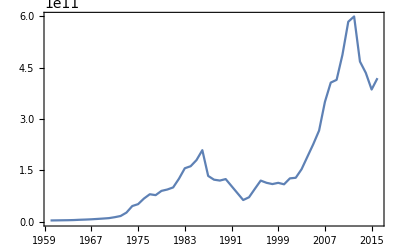

```mathematica
DateListPlot@
CountryData["Iran",{"GDP",All}]
```

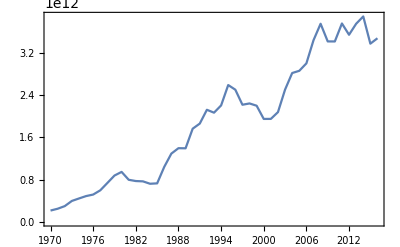

```mathematica
DateListPlot@
CountryData["Germany",{"GDP",All}]
```

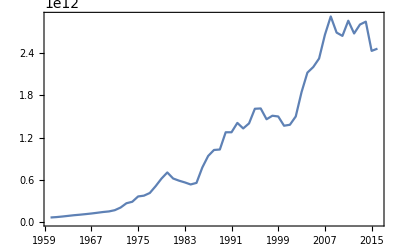

```mathematica
DateListPlot@
CountryData["France",{"GDP",All}]
```

```mathematica
stats={Mean,Variance,Median,Quartiles,Skewness,Kurtosis,Composition[N,Entropy]}
```

{Mean,Variance,Median,Quartiles,Skewness,Kurtosis,N@*Entropy}

```mathematica
Grid@
Table[
{f,f[data]},
{f,stats}]
```

Mean | 0.393152
Variance | 0.118489
Median | 0.445191
Quartiles | {0.168998,0.445191,0.664902}
Skewness | -0.615168
Kurtosis | 2.79853
N@*Entropy | 9.0497

```mathematica
stats={Mean,Variance,Quartiles,Skewness,Kurtosis,Composition[N,Entropy]}
```

{Mean,Variance,Quartiles,Skewness,Kurtosis,N@*Entropy}

```mathematica
Grid@
Table[
{f,f[data]},
{f,stats}]
```

Mean | 0.393152
Variance | 0.118489
Quartiles | {0.168998,0.445191,0.664902}
Skewness | -0.615168
Kurtosis | 2.79853
N@*Entropy | 9.0497

```mathematica
{1,1,1,1,1,1}
```

{1,1,1,1,1,1}

```mathematica
Entropy@{1,1,1,1,1,1}
```

0

```mathematica
Entropy@{1,1,1,1,1,2}
```

-(5 Log[5])/6+Log[6]

```mathematica
N[-(5 Log[5])/6+Log[6]]
```

0.450561

```mathematica
Entropy@{3,3,3,3,3,2}
```

-(5 Log[5])/6+Log[6]

```mathematica
N[-(5 Log[5])/6+Log[6]]
```

0.450561

```mathematica
Variance[{a,b,c}]
```

1/6 ((2 a-b-c) Conjugate[a]+(-a+2 b-c) Conjugate[b]+(-a-b+2 c) Conjugate[c])

```mathematica
FullSimplify[Variance[{a,b,c}],{a,b,c}∈Reals]
```

1/3 (a^2+b^2-b c+c^2-a (b+c))

```mathematica
DiscreteWaveletTransform[data]
```

DiscreteWaveletData[<<DWT>>, <13>, {8516}]

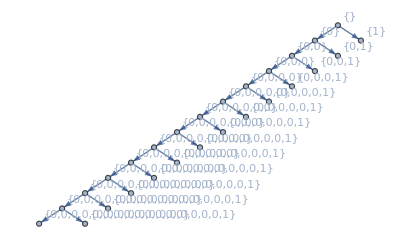

```mathematica
%40["TreeView"]
```

```mathematica
WaveletThreshold[%40]
```

DiscreteWaveletData[<<DWT>>, <13>, {8516}]

```mathematica
WaveletScalogram[%40]
```

-Graphics-

```mathematica
%40["Wavelet"]
```

HaarWavelet[]

```mathematica
Normal[Out[40]]
```

{{0}→{0.277492,0.294683,0.676777,0.654349,-0.0149562,-0.242526,-0.499414,-0.209191,-0.214738,0.49313,0.940661,1.02743,1.16179,1.00288,0.785025,0.744348,0.47319,0.157055,0.471621,0.203993,-0.15948,-0.224748,-0.310257,-0.671526,-0.389885,0.625704,0.601311,0.735066,0.283606,0.27787,-0.488185,-0.710056,-0.752815,-0.485912,0.140875,0.644204,0.64879,0.726592,0.276806,-0.0671783,-0.0936706,-0.0644641,0.128623,0.528704,0.651461,0.384856,0.906799,1.01565,0.758092,0.724153,0.73812,0.716197,0.166493,-0.381869,0.667282,0.740939,0.627072,0.717763,0.928888,0.84033,0.726282,0.868777,0.783216,0.36194,0.451615,0.781356,0.705452,0.469897,0.441684,-0.446889,-0.379008,-0.567044,-0.711544,-0.832937,-0.0478067,0.185683,0.188661,0.673023,0.626909,0.751733,0.723524,0.770435,0.581357,0.572806,0.751097,0.720769,0.720058,0.446943,0.816265,0.586023,0.477172,0.542625,0.417906,0.624201,0.596741,0.473506,0.596723,0.888896,1.08912,1.0201,0.819167,0.286609,0.455456,0.324536,0.603269,0.749656,0.836357,0.827042,1.03856,1.00109,0.938605,1.15016,0.838552,0.967604,0.975117,0.881201,0.655193,0.826723,0.76479,0.730399,0.92617,1.2186,1.06742,0.701552,0.594513,0.407908,0.0912372,-0.569304,-0.594303,-0.317508,-0.00233729,0.00452527,0.526502,0.85909,0.931439,0.716756,0.874737,0.557848,0.533442,0.337185,0.459384,0.196823,0.349984,0.488408,0.6854,0.632946,1.13625,0.921134,0.717666,0.488885,0.508901,0.551154,0.297842,0.054748,0.350607,0.148498,0.114784,0.234657,0.322393,0.28082,0.00854916,0.339288,0.0916525,0.537365,0.599623,0.669981,0.768251,1.06572,0.738155,0.811063,0.606173,0.896112,0.992996,0.909298,0.898238,0.686357,0.680335,0.429526,0.188897,0.0727368,-0.161372,0.170179,0.12533,0.397159,0.51501,0.48462,0.414518,0.544121,1.02625,1.06109,0.980267,0.982457,0.709097,0.879491,0.944798,1.07662,1.14803,1.32462,1.31324,1.31518,1.12749,1.04993,0.98087,0.878438,0.763093,0.909283,1.14015,1.05183,0.914548,1.03276,1.13642,1.11429,0.995469,0.94786,0.930897,0.981462,0.934476,0.987838,0.896104,0.786141,0.738031,0.968652,1.01132,1.04407,1.11293,1.2049,1.25273,1.22314,1.19883,1.27708,1.34272,1.35751,1.31225,1.26148,1.18142,0.948364,0.685562,0.770427,0.753755,0.430953,-0.0139481,-0.241529,0.109575,0.318634,0.536493,0.679895,0.546609,0.660873,0.670164,0.924219,0.549751,0.618378,0.724271,0.69529,0.601938,1.20808,1.29504,1.26425,1.045,1.02049,0.983431,0.801769,0.827509,1.04152,0.481917,0.710197,0.9405,0.899883,1.06221,1.19886,1.24262,1.17269,1.13507,1.21674,1.09193,1.19272,1.19291,1.17523,1.10783,1.09988,1.10162,1.08362,1.02342,0.894151,1.01091,1.06491,1.04472,1.08472,1.10276,1.00843,0.874938,0.914035,0.783301,1.07389,0.844204,0.756699,0.887319,0.804411,0.697988,0.923963,1.0313,0.828348,1.08444,1.19568,1.1926,1.21106,1.24301,1.1882,1.21936,1.15109,1.0858,1.06079,0.968222,0.79323,0.736841,0.624073,0.708331,0.610652,0.741161,1.01632,0.705744,0.771721,0.857063,0.900183,0.875214,0.616578,0.661293,0.825857,0.86518,0.760263,0.286028,0.468309,0.912455,1.02951,0.94012,0.927998,0.830931,0.752314,0.683502,0.854574,0.979719,0.890467,0.870861,1.09561,1.1257,1.03497,1.10099,1.07101,1.11906,1.19404,1.0933,0.589084,0.423828,0.318189,0.487123,0.997933,1.0042,0.951601,0.96898,0.34862,-0.175085,-0.337337,-0.186117,-0.0889015,0.508826,0.993627,1.16287,0.787191,0.926789,0.945367,0.584408,0.170808,-0.216094,-0.295197,-0.432503,-0.223781,0.0980693,0.431925,0.60728,0.611141,0.546133,0.400061,0.85182,0.478076,0.08543,-0.196516,-0.180218,-0.214828,0.0260461,0.613437,0.99125,0.498402,-0.487923,-0.817647,-0.67241,-0.375887,-0.617707,-0.827762,-0.961155,0.110005,0.168402,0.282569,0.381023,0.57753,0.535599,0.491004,0.258528,0.40622,0.283114,0.0538371,0.213055,0.527114,0.736383,0.79566,0.0833333,-0.0470724,-0.173647,-0.624969,-0.421416,0.153399,0.351789,0.362963,0.48331,0.589002,0.716036,0.845287,1.08489,1.16492,1.25548,1.25898,1.0549,1.05584,1.04772,0.96411,0.845252,0.762085,0.575282,0.785624,-0.504268,-0.651466,-0.0432338,0.292925,0.35985,0.880038,1.12122,1.02051,0.707342,0.47778,0.519369,0.910677,1.00439,1.12232,1.14129,1.0668,0.822444,0.787217,0.935585,1.02274,1.13998,1.01412,0.945228,0.443915,0.374748,0.154904,0.243363,-0.0613955,0.602406,0.801649,0.908828,0.877179,0.559141,0.639714,0.774512,0.854576,0.863553,1.15256,0.881355,0.734484,0.662546,0.968096,0.991132,1.01953,0.237851,0.190987,-0.0185127,-0.0494285,-0.244777,0.296753,-0.132539,0.394715,0.192284,0.298771,0.339584,-0.00345609,-0.449426,-0.2182,-0.0765534,-0.201204,-0.0591141,0.360708,0.13882,-0.0236594,0.551148,0.785118,0.767362,0.758274,0.951632,0.640518,0.739037,1.00009,0.991602,0.930823,0.814212,0.592484,0.635684,0.787975,0.458564,0.430358,0.534145,0.523328,0.41963,0.141156,0.287741,0.379458,-0.525469,-0.328581,0.0636999,0.241807,0.201812,0.728415,0.870782,0.652887,0.553472,0.631758,0.542107,0.176161,0.28465,0.179944,0.257145,0.417505,0.602752,0.744942,0.531297,0.398322,0.55298,0.305618,-0.0552966,-0.164372,-0.125187,-0.136826,0.55795,0.851181,0.894833,0.856743,0.92075,1.0128,0.313579,0.0281284,0.841689,1.02164,1.03412,1.31991,1.32995,1.08671,0.766589,0.752174,0.610579,0.806891,1.16507,1.15876,1.2392,1.16636,0.786733,0.764477,0.796858,0.517436,0.697056,1.06163,0.927426,0.850333,0.970366,0.769681,0.388726,0.674873,0.933087,0.691409,0.573752,0.682927,0.790326,0.913746,1.09607,1.20446,1.15898,1.03983,0.562292,0.747976,0.785866,0.618345,0.707172,0.896895,0.891741,0.871065,1.18132,0.671823,0.0230003,0.550243,0.88289,1.01314,1.08575,0.851474,0.952879,0.60272,0.455636,0.28726,0.579127,0.119075,0.113306,0.0948966,0.58379,0.396054,0.86926,0.799926,0.735772,0.418318,0.926787,0.200477,0.465964,0.773943,0.832844,0.599186,1.14269,1.16072,1.12506,1.21167,1.20046,1.13486,1.0878,1.06977,-0.310303,-0.484029,-0.594933,-0.689434,-1.12218,-0.520396,-0.808501,-0.547426,-0.415183,-0.371409,-0.429907,0.489466,0.280727,0.528852,0.544052,0.752889,0.468004,0.380291,0.422493,1.07647,0.91894,0.754709,-0.231905,-0.331319,-0.303051,0.0652319,0.279613,0.688115,0.0294687,0.0502715,-0.0213556,-0.1168,-0.114162,0.0820174,-0.047211,0.113071,0.0471561,-0.161996,-0.131804,-0.0248863,-0.168289,0.13881,-0.0818811,0.557585,0.676828,0.916958,0.904425,0.996792,0.950828,0.790723,-0.182183,0.327665,0.449296,0.618433,0.710864,0.679088,0.837383,0.849366,0.709064,0.601138,0.599158,0.412284,0.415672,0.438844,0.00860448,0.28086,0.26153,0.460352,0.439939,0.365136,-0.425177,-0.374418,-0.584999,-0.516338,-0.294725,0.278109,0.73527,0.944549,1.1085,1.10575,0.935042,0.524141,0.323302,0.0301166,0.14212,-0.240407,-0.52229,-0.0396135,0.78357,0.65039,0.545046,0.719727,0.290477,0.26627,0.47815,0.406002,0.281698,0.633624,0.772839,0.757276,0.660928,0.501482,0.386899,-0.260629,-0.123488,0.300308,0.876863,0.842746,1.02238,1.09009,0.777775,0.562616,0.528344,0.468362,0.563143,-0.0604044,0.167072,0.0256483,-0.465457,-0.443127,-0.581212,0.364629,0.542216,0.610014,0.941439,1.0458,1.12167,0.984433,0.993225,0.974383,1.02881,0.973661,1.00141,0.637276,0.382209,0.27377,0.0121379,-0.393736,0.283602,0.0723682,0.164888,0.185243,-0.103109,-0.554302,-0.340641,-0.4875,-0.432521,-0.412962,0.159607,0.35441,0.379836,0.368371,0.253754,0.494481,0.519778,0.716774,0.802235,0.81362,1.01858,1.29,1.17803,1.17231,1.21178,1.20079,1.14664,0.937254,0.754472,0.556684,0.0777893,0.105628,0.444795,0.159015,0.110147,0.728007,0.768789,0.724542,0.527638,0.329329,0.132743,0.712862,1.03301,1.06816,0.934338,0.854115,0.594735,0.468166,0.705029,0.648906,0.714534,0.65576,0.416612,0.134596,0.195329,-0.170491,-0.0450024,0.167043,0.317795,0.519535,1.0277,1.15303,1.29458,1.27231,1.2564,1.23409,0.941075,0.816068,0.814382,0.85327,0.846923,0.965127,0.983042,0.735194,0.33608,0.638967,0.502565,0.348493,0.386139,0.480972,0.0177989,0.81401,1.0374,0.828572,0.879977,0.96156,0.826662,0.785904,0.750121,0.249346,0.25736,0.176741,-0.416205,-0.434815,-0.433038,-0.653198,-0.174739,0.211049,0.0346432,0.107162,0.0261331,-0.0789462,0.0698939,0.700363,0.0620272,-0.0770545,0.392862,0.374864,0.742361,0.934345,1.03476,1.00521,1.07341,0.858239,0.932465,0.985494,1.00159,1.05437,0.817551,0.98906,0.971228,0.978108,1.18043,1.22529,1.0323,0.938887,0.763854,0.539601,0.669063,0.809545,0.9777,1.18539,1.17214,0.951832,0.794975,0.54989,0.682726,0.52428,0.242103,0.0377451,-0.104635,-0.265116,-0.149542,0.0268387,0.570475,0.632606,0.583174,0.696148,0.827689,0.902502,0.918454,0.810118,0.710256,0.366594,0.0607556,-0.0360555,-0.110502,-0.324803,-0.0063019,0.185342,0.496948,0.488652,1.00182,1.05226,1.00002,0.576654,0.0838795,-0.0418175,0.298686,0.291132,0.404163,0.726726,0.565054,0.0750516,0.600883,0.64931,0.728419,0.661994,0.450834,-0.0930557,-0.344042,-0.286392,-0.366332,-0.308629,-0.169673,-0.20443,0.174358,0.150076,0.209724,0.225862,0.336998,0.508966,0.876141,0.960708,0.771368,0.613349,0.503916,-0.181505,0.259841,0.310072,0.214981,0.178875,0.0228823,-0.472511,-0.438597,-0.16957,-0.139539,0.463051,0.196416,0.316029,0.302369,0.375413,0.300832,0.510718,0.138799,0.20708,0.122193,0.0509693,-0.0953471,0.0777089,0.179731,0.306941,0.316293,0.128754,-0.185976,-0.333889,-0.06857,-0.0703101,-0.0665139,0.236134,0.174616,0.398922,0.381944,0.800354,0.887459,0.874292,0.0029344,0.142167,0.229079,0.290859,0.244749,0.631191,0.50147,0.172468,-0.0349518,0.379079,0.290733,0.448149,0.742407,1.11433,0.98213,0.859828,0.766744,0.781742,0.910301,0.645499,0.687542,0.615764,0.660703,0.75987,0.722883,0.571411,0.682709,0.774048,0.847167,0.951132,0.891376,0.82009,0.702634,0.677538,0.648413,0.622364,0.528658,0.739222,0.584952,0.669407,0.951265,1.05573,1.04186,1.0181,1.01618,0.846618,0.729224,0.370228,0.407222,0.291924,0.252961,0.169505,0.625939,0.724095,1.02215,1.20455,1.22008,1.17271,1.01624,0.616262,0.389208,0.197116,0.064353,0.0254965,-0.147888,-0.262861,0.490965,0.610153,0.817962,0.545521,0.632456,0.456906,0.216177,0.291193,0.469094,-0.0298297,0.0905826,0.73967,0.910178,0.904401,0.964053,1.13405,1.09124,0.925893,1.04396,1.00254,1.04723,1.05207,1.06243,1.0882,1.07893,0.913632,0.266353,0.223334,0.189533,0.0985905,0.224408,0.713121,1.08718,1.1356,0.95002,0.522847,0.402714,0.597028,0.596466,0.799067,0.835384,0.823843,0.269327,0.375117,-0.321427,-0.318368,0.0467511,0.923717,0.484968,0.491747,0.745608,0.827603,0.549475,0.728085,0.534108,-0.321659,-0.367366,-0.367755,-0.917566,-0.818694,-0.226661,-0.22767,-0.21039,-0.185241,-0.35443,0.0838667,-0.157864,-0.0707331,-0.139516,-0.224286,-0.274894,-0.160225,-0.330544,-0.27751,-0.0173952,0.044839,-0.309823,-0.677021,-0.404764,-0.210072,-0.0604594,0.845094,0.717017,0.680363,0.473144,0.446254,0.0861846,0.0760787,-0.0286658,0.194514,0.0201318,0.480814,0.640183,0.653915,0.832844,1.17672,1.04926,0.865918,0.85813,1.08825,1.05548,1.06702,1.06278,1.17595,1.13141,0.661061,0.6044,0.649572,0.480146,0.440818,0.702867,0.866405,0.638486,0.922156,0.925954,0.936542,0.893004,0.951361,0.601391,0.600448,0.572938,0.504019,0.266134,0.192329,0.457318,0.490024,0.763613,0.905459,1.00756,0.85342,0.961547,0.734159,0.250783,0.169529,0.304746,0.21575,-0.439719,-0.499407,-0.957499,-0.909014,-0.889618,-0.587917,-0.221769,0.32558,0.494918,0.676204,0.795683,0.986187,0.484328,0.533209,0.486571,0.26809,0.33088,0.446454,0.427621,0.305006,0.426202,0.419918,-0.134539,0.6101,0.664158,0.620373,0.511951,0.284069,-0.344238,-0.393862,-0.370783,-0.288086,0.218786,0.48906,0.139858,-0.221338,-0.204049,-0.108924,0.0856973,0.243947,0.416932,0.462417,0.597831,0.665723,0.259134,0.369268,0.272712,0.277748,0.323433,0.492437,0.411347,0.327573,0.189096,0.108078,-0.298287,-0.763048,-0.82998,-0.628155,-0.766841,-0.214553,0.497027,0.322662,0.202356,0.857048,0.739872,0.668558,0.626922,0.468293,0.138031,0.157494,-0.0437132,-0.246372,0.0144067,0.346905,0.562859,0.980064,1.04289,0.999283,1.05073,0.958377,0.704262,0.750513,0.716254,0.739127,0.791309,0.493157,0.349561,0.443621,0.264665,0.371989,0.569013,0.447011,0.291065,0.259387,0.0162356,-0.200949,-0.0943644,-0.218676,-0.0986388,0.427075,0.325548,-0.151826,-0.153315,-0.159378,-0.099632,0.295397,0.559971,0.568321,0.380547,0.029824,0.156612,0.0375976,0.0591059,0.0610802,0.479043,0.396618,-0.114374,0.0452304,0.0473364,-0.0460883,-0.192908,-0.187693,-0.333368,-0.160358,-0.14878,-0.00987051,0.492172,0.604021,0.7164,0.592309,0.558119,0.460245,0.766597,0.536504,0.684578,0.48488,0.310015,0.154132,0.203522,-0.0519874,-0.0864621,-0.0502134,0.3507,0.516808,0.0433991,0.0634589,0.0767299,0.0116055,0.15402,0.4116,0.303448,0.396609,0.387319,0.26007,0.607728,0.609727,0.624532,0.546001,0.623287,0.0196223,-0.159989,-0.096986,-0.140834,-0.19941,-0.0387589,0.102031,0.0368674,0.0815349,0.0874884,0.234174,0.239171,0.370591,0.567505,0.893607,0.533768,0.314617,0.337484,0.274674,0.148911,0.253411,0.0111849,-0.0865347,0.352893,0.739352,0.0952819,-0.192925,-0.178293,-0.375922,-0.428531,-0.0563732,-0.0979249,0.129457,0.128034,0.603914,0.998929,0.926836,0.608302,0.826557,1.10332,0.932136,0.740473,0.887174,0.613228,0.528317,0.491648,0.657222,0.763591,0.708246,0.679752,0.872272,0.54432,0.58109,0.62467,0.473553,0.256476,0.000687966,0.345864,0.460941,0.699895,0.836133,0.804477,0.473544,0.200441,-0.0496791,0.512048,0.676295,0.61665,0.630034,0.766147,0.646161,0.868151,1.21629,1.10318,0.942797,0.308025,-0.333104,-0.0187242,-0.0297538,-0.117254,-0.104408,0.127808,-0.21332,-0.414524,-0.0909558,0.359582,-0.169373,-0.876416,-0.526883,0.119683,0.317997,0.447242,0.31233,0.57175,0.656632,0.655221,0.673875,0.80372,0.571502,0.457378,0.556859,1.14803,1.13463,0.798587,0.740776,0.733114,0.589136,0.547801,0.467559,0.594982,0.83577,0.773462,0.729816,0.580373,0.402855,0.325455,0.286374,0.202091,0.422478,0.922226,0.399135,0.52541,0.296171,-0.105041,0.315146,-0.155364,-0.375575,-0.376874,-0.373014,-0.679584,0.0961167,0.0741444,0.635943,0.828129,0.857791,0.699084,0.602644,0.814641,0.625883,0.567475,0.734408,0.852832,0.227876,0.108213,0.0988186,-0.136312,-0.213694,0.292093,0.880054,0.666768,0.665066,0.750096,0.0592526,-0.292335,-0.143648,-0.306571,-0.611056,-0.464542,0.0247092,-0.318642,-0.542438,-0.252987,0.233221,0.252152,0.738838,0.768693,0.871562,1.00105,1.10151,1.07968,1.23319,0.976018,0.725644,0.502429,0.826798,0.450403,0.298806,0.177931,0.287728,0.334448,0.630006,0.96647,0.583636,0.657397,0.431298,0.251407,0.120662,0.361945,0.456646,0.703871,0.842782,0.869495,0.777186,0.483423,0.436356,0.0548049,0.201886,0.706669,1.0071,1.05153,1.17808,1.24142,1.1232,0.719212,0.812577,0.667507,0.675705,0.892492,0.933619,1.12352,1.0251,0.840897,1.25585,1.07339,0.696193,0.606686,0.507531,0.0663313,0.394016,0.623692,0.642348,0.664081,0.199567,-0.509183,-0.282001,-0.221951,-0.38269,-0.189045,-0.0794529,0.0767957,0.753106,0.798586,0.798962,0.793278,0.844507,0.77952,0.877086,0.71337,0.595141,0.370722,0.351527,0.380559,0.192522,0.0428521,0.00740942,0.184195,0.0197157,0.208104,0.51725,0.840227,0.892942,1.12517,1.13435,1.08577,1.07121,1.10654,1.10205,1.19333,0.981665,0.941459,0.685672,0.415696,0.3813,0.473424,0.1314,0.350897,0.833365,0.964826,1.06908,0.973388,1.07206,0.874922,0.848636,0.595408,0.764447,0.464485,0.310879,0.53763,0.717668,0.859698,0.284806,0.343709,-0.0748828,-0.00570507,-0.260528,0.297784,0.457344,0.930994,0.785381,0.669416,0.822815,0.91995,0.697821,0.71859,0.704697,0.506462,0.636645,0.979378,0.880673,0.747259,0.778626,0.771303,0.588982,0.61178,0.641148,0.23028,0.0201297,0.168466,0.0404562,0.324601,0.53082,0.718165,0.759759,1.12803,0.942603,0.766651,0.320682,0.555902,0.476478,0.436195,0.530403,0.398839,0.548876,0.024736,0.0148839,-0.175378,0.0551961,0.348311,0.624598,0.858366,0.822589,1.15471,1.22002,1.10828,1.01212,1.00993,0.814014,0.0929804,0.132083,-0.07842,-0.795295,-0.0934672,0.450556,0.492544,0.47065,0.978717,0.680421,0.273805,-0.114035,-0.00812875,-0.048696,0.0592851,0.0900583,0.122719,0.255439,0.161878,0.242051,0.127897,1.00279,0.721883,0.263586,0.336932,0.588401,0.73463,0.596853,0.68987,0.807315,0.668996,0.832992,0.986129,1.09451,1.12582,0.971735,0.655147,0.673566,0.698798,0.344531,-0.00226589,0.465553,0.325656,0.320376,0.536018,0.885542,0.741582,0.776305,0.781698,0.727133,0.639785,0.534503,0.347513,0.173222,0.31188,0.569562,0.593738,0.839937,0.514725,0.27079,0.219123,0.43196,0.311205,0.496373,0.670579,0.799947,0.861737,0.980132,0.793543,0.71321,0.639781,0.571752,0.450008,0.761919,1.10502,1.04537,0.904335,0.943907,0.910113,0.895537,0.40895,0.648847,0.863563,0.885509,0.822622,1.08788,0.90615,0.552405,0.519702,0.938254,0.971482,1.0889,1.20115,1.18905,0.944432,0.419512,0.393042,0.116025,0.0194245,0.227239,0.417317,0.339949,0.3364,0.565022,0.430888,0.0976812,-0.0469707,-0.194187,-0.430941,-0.27178,0.202229,0.589412,0.601293,0.588881,0.501368,0.451786,0.944384,1.03406,0.948421,0.564572,0.14064,-0.13549,-0.261103,-0.0965135,0.252031,0.193523,0.19396,0.285271,0.187915,-0.0741906,-0.319389,-0.440813,-0.472951,-0.402167,-0.340954,-0.589438,0.0436439,0.125638,0.255205,0.692067,0.699921,0.865122,0.898246,0.968312,0.818275,0.881493,0.968331,0.951824,0.764628,0.795967,0.782199,0.679708,0.593337,0.498173,0.539395,0.558188,0.603457,0.848595,1.04557,0.921653,1.0429,1.00677,0.903902,0.823075,0.867033,0.494973,0.440538,0.180737,0.0969644,0.229707,0.439455,0.602413,0.791172,0.99324,1.2124,1.16162,0.924599,0.665989,0.59232,0.806361,1.05544,1.08331,1.07384,1.01043,0.978362,0.910205,1.00101,1.01437,1.24455,1.23995,1.12598,1.12249,1.1397,1.19414,1.20095,1.24598,1.06491,1.05719,0.252843,-0.137481,-0.161815,0.521977,-0.0758448,0.315581,0.720627,0.284967,0.26243,0.604728,0.656832,0.711841,0.994695,1.16833,0.921487,0.748598,0.896616,1.02119,0.872307,0.445921,0.264922,0.0825392,0.286558,0.568924,1.05366,1.10277,0.982071,0.990698,0.922198,0.482876,0.395398,0.233738,0.244891,0.388386,0.947098,1.1783,1.23044,1.337,1.30856,1.31125,1.33937,1.15992,0.957929,0.952116,0.808375,0.698444,0.850756,1.0253,0.995168,0.967267,1.07243,0.617127,0.291241,0.0411563,0.0648199,0.101025,0.849337,0.852259,0.846092,0.891866,1.07319,1.05695,1.15118,1.29896,1.1975,1.11209,0.786661,0.619499,0.524652,0.623334,0.744019,0.531303,0.450723,0.521872,0.567966,0.45724,0.678502,0.692059,0.361555,0.668435,0.77387,0.915401,1.12712,0.868263,0.653993,0.669419,0.701071,1.0489,0.860818,0.820128,0.951095,0.984709,0.895236,0.336491,0.510899,0.391365,0.391043,0.264254,1.02586,1.0539,1.08988,0.989342,1.14609,1.11267,0.988715,1.02216,1.18843,0.89457,0.930474,0.254216,0.254404,0.308116,0.224293,0.387814,0.721613,0.7109,0.729563,0.73498,0.681222,0.680122,0.663285,0.891486,0.929993,0.957532,1.08688,1.10945,1.18796,1.21881,1.20909,1.20589,1.1663,1.17142,1.13463,1.14405,1.21601,0.971306,0.783158,0.685029,0.607948,0.480902,0.794804,0.68512,0.708935,0.750668,0.672852,0.851517,0.970602,1.07274,1.18349,0.880202,0.290027,-0.112636,0.382497,0.51728,0.834459,1.15116,1.197,1.09197,1.18821,1.28201,1.19504,1.12462,1.08602,1.04639,0.924134,0.873288,0.929534,0.972343,1.02079,1.00404,1.02608,0.7644,0.406065,0.39946,0.413266,0.4627,0.462517,0.37448,0.465368,0.555699,0.946048,1.12348,1.17885,1.03725,0.986162,0.87274,0.706994,0.851345,0.937477,0.929855,0.923742,0.980872,1.0646,1.19304,1.18742,1.14635,1.20386,1.17271,1.06028,0.982656,0.955554,0.907845,0.928396,0.897141,0.846788,0.983999,0.931549,0.716531,0.892846,0.718883,0.763635,0.752172,0.939792,0.876797,1.12566,1.16967,0.987031,1.07811,1.06152,1.05395,0.931401,1.09531,1.08082,1.10517,1.18465,1.21068,1.22152,1.18235,1.16813,0.994966,0.859217,0.659742,1.14391,1.25369,1.25739,1.30597,1.331,1.20454,1.15194,1.23998,1.1322,1.05257,0.955978,0.859686,0.646556,0.707556,0.802504,0.851741,0.638704,0.926495,0.128492,0.295571,0.0275668,0.144825,0.267791,0.884116,0.634282,0.705124,0.822255,0.704127,0.447267,0.611638,0.631643,0.582534,0.786654,0.802161,0.762607,0.783409,0.669888,0.394605,0.340096,0.612727,0.741834,1.03087,1.09535,0.779388,0.179536,-0.05371,0.120881,0.430904,0.769727,1.17004,1.2029,1.14091,1.07817,0.839815,0.787324,-0.0144065,-0.290041,-0.301461,-0.297684,-0.43747,-0.280982,-0.0175584,0.366309,0.700714,0.762205,0.915108,0.933004,1.056,1.10294,1.17754,1.12627,1.1244,0.947741,0.907481,0.628346,0.579518,0.0829518,0.267007,0.304459,0.390642,0.603155,0.802441,0.815801,0.829342,0.810436,0.87005,0.70471,0.597883,0.539475,0.915237,0.937872,0.972709,1.01714,1.03268,0.604009,0.311409,0.306089,0.278909,0.121817,-0.0150675,0.0791226,0.307865,0.632964,0.886985,0.778113,0.80307,0.66891,0.389801,0.23349,0.521313,0.659573,0.85823,1.0528,1.05741,0.920351,1.07655,1.20081,0.93679,0.96256,0.933573,0.687966,0.463077,0.469859,0.0857786,0.752691,0.800391,0.689822,0.546627,0.580987,0.511567,1.03616,1.14095,1.27747,1.19107,1.08306,0.99187,0.893538,0.412932,-0.236124,-0.468041,-0.3551,-0.259508,0.0567515,0.515957,0.502051,0.632748,0.657695,0.412355,0.143074,0.29314,0.354626,0.887096,1.14153,1.05922,0.665278,0.804476,0.839324,0.683213,0.447426,-0.0254822,-0.173996,-0.294569,-0.24894,-0.133382,0.068211,0.111218,0.0764629,-0.149789,0.155535,-0.0783812,-0.178632,-0.180424,0.0269879,0.205393,0.354702,0.510001,0.615042,0.690665,0.992463,0.945561,1.02371,1.13679,1.06503,0.739405,0.609404,0.626989,0.0905083,0.331895,0.122955,0.345368,0.365516,0.475935,0.324119,0.711818,0.718352,0.722481,0.367435,0.119163,0.631162,0.606241,0.367536,0.661418,0.618131,0.317166,0.424344,0.590619,0.744448,0.78411,0.302929,0.0146731,-0.287216,-0.259689,0.125723,0.346177,0.150373,0.255378,0.238816,-0.0462668,-0.105434,0.697038,0.587728,0.470091,0.344539,0.61822,0.259939,0.51249,0.899575,0.788785,0.626493,0.591354,-0.176674,-0.102451,-0.683652,-0.528461,-0.370049,-0.320633,-0.356813,0.922368,0.716367,0.893234,1.01115,1.14698,0.908545,0.760869,0.687176,0.897388,0.608364,0.513869,0.428861,0.376172,0.401387,0.33722,0.16336,-0.0539762,-0.257002,-0.110932,-0.391489,0.18131,0.333403,0.876615,1.10482,1.03259,1.03973,1.08863,1.03328,0.974222,1.03154,0.96349,0.921667,0.906036,0.658636,0.412812,0.460574,0.111051,0.257323,0.7415,0.728654,0.602833,0.790838,0.905314,1.01334,0.917672,0.724178,0.553198,0.454035,-0.13675,-0.356267,-0.217958,0.0408916,0.0603687,0.22512,0.758504,0.849973,0.680325,0.727583,0.737558,0.757404,0.469835,0.492977,0.441083,0.429024,0.0667814,0.572774,0.839064,0.800109,0.172482,0.523791,0.708046,0.627599,0.498957,1.18105,0.955545,0.8831,0.295753,0.124672,0.213744,0.503332,0.348801,-0.149877,0.0559473,0.0334421,-0.565655,-0.455852,-0.145454,-0.196542,-0.185339,0.580608,0.850345,1.00146,0.886994,0.856856,0.892626,0.43631,0.314185,0.298857,0.130103,-0.0675091,0.177716,0.000991532,-0.0266375,0.268829,-0.302592,-0.232871,-0.0648986,0.292639,0.371486,0.594767,0.608078,0.190474,-0.460318,-0.287668,-0.413987,-0.543507,-0.358841,0.81864,0.802754,0.791059,0.829309,0.801356,0.709869,0.754732,0.663535,0.230743,0.36234,0.398323,0.432349,0.459327,0.87568,1.191,1.21792,1.19861,1.26225,1.15345,0.762125,0.570284,0.619759,0.592032,0.565087,0.223546,0.403302,0.284911,0.23195,0.35358,0.180578,-0.0772373,-0.092765,-0.0583997,-0.0951434,0.108007,0.24394,0.466265,0.385302,0.702602,0.679338,-0.122432,-0.185252,-0.217428,-0.149764,-0.300993,0.453468,0.774366,0.350451,-0.0386579,0.087315,0.163661,0.466521,0.746282,0.943065,1.10805,1.01827,0.551095,0.420052,0.361151,0.16336,-0.0813033,0.213966,0.498796,0.598916,0.825963,0.729342,0.719508,0.677438,0.357137,-0.119629,-0.299532,-0.542704,-0.574115,-0.230499,0.470021,0.235777,-0.100322,0.110079,-0.0678724,0.064369,-0.23237,-0.301724,-0.223892,-0.247122,-0.697909,-0.785195,-0.854439,-0.874309,-0.912978,-0.663555,-0.1077,0.697947,0.729155,0.845393,0.881002,0.867692,0.6312,0.440722,0.990209,1.08949,0.532037,0.0970401,0.0652386,-0.633166,-0.57439,-0.161346,0.326323,0.674222,0.746109,0.798403,1.26154,1.15859,0.747555,0.660404,0.58639,0.388714,0.337968,0.291803,0.555525,0.71964,0.606813,0.799707,0.789255,0.546645,0.486634,0.0677543,-0.213639,-0.0466455,-0.4963,-0.664076,-0.415149,-0.232003,-0.154628,0.188209,0.301506,0.57924,0.635206,0.532362,0.367757,0.511978,0.557286,0.496965,0.833984,0.907374,1.25223,1.20317,1.25159,1.20498,1.21157,0.984763,1.12148,1.21679,1.27104,1.28037,1.12678,0.998946,0.87459,0.323641,0.177738,0.179746,0.0910525,0.17206,0.186803,-0.110296,-0.161196,0.0467011,-0.0977798,-0.182776,0.0329309,0.070033,0.0670812,0.36735,0.429961,0.314458,0.34246,0.663702,0.779368,0.684808,0.701287,0.537674,0.213924,-0.33876,-0.316921,-0.176874,0.111093,0.149958,0.679992,0.520546,0.550199,0.384931,0.170976,0.0604454,-0.0587181,-0.168361,-0.470014,0.342107,-0.146526,0.0300702,0.219051,0.419474,0.390146,1.16398,1.19361,1.18733,1.17047,1.04419,0.928872,1.01817,1.11015,1.02243,1.13348,1.06702,0.812033,0.462831,0.453351,0.350135,0.439071,1.22454,1.31305,1.27052,1.11031,0.6999,0.0594583,0.49622,0.553659,0.577236,0.942382,0.936753,0.38778,0.261363,0.279505,0.137103,0.338218,0.800532,0.994593,1.20473,1.21634,1.28399,1.11709,0.976393,0.740965,0.872108,0.948851,0.969524,1.06725,1.09728,1.13932,1.06655,1.20402,1.09348,1.15405,1.14145,1.19368,1.14401,1.21225,1.25234,1.25841,1.22414,0.656124,0.415299,0.160272,0.0742892,-0.0163527,0.324543,0.764405,0.590669,0.675256,0.790029,0.701465,0.69688,0.38852,0.303283,0.415094,0.474382,0.607881,1.05047,1.132,1.21407,1.17622,1.09869,0.937963,0.871091,0.750161,0.641709,0.857147,0.989783,1.10901,1.1893,1.28991,1.1519,0.832558,0.543085,0.532434,0.451505,0.629596,0.563018,0.949405,0.766021,0.917058,0.74064,0.624877,0.518522,0.589303,0.530373,0.649301,0.940183,0.942683,0.168345,0.00521159,-0.0449845,-0.0155333,-0.0710164,0.922614,0.84475,0.738246,0.713959,0.764312,0.633261,0.319591,0.408873,0.699044,0.802565,0.956501,1.18976,1.1593,1.25537,1.27249,1.1503,1.03063,0.969618,0.85332,0.790725,0.630776,0.624278,0.742241,0.818172,0.895525,0.368719,0.608086,0.668321,0.748225,0.966981,0.787837,0.826373,0.927196,1.20054,1.25018,1.10419,1.06102,0.912929,0.968808,1.07442,1.10456,0.893369,0.857693,0.78231,0.589159,0.517627,1.09676,1.04594,0.856585,1.29605,1.29125,1.22871,1.08823,1.05525,1.00768,1.0066,0.982068,1.26808,1.27893,1.23901,1.07189,0.932389,0.503368,0.507486,0.479908,0.565868,0.814948,0.896873,0.955715,0.957448,0.819464,1.08936,-0.0759321,-0.0832555,0.0174964,0.140582,-0.32037,1.12591,1.02961,0.970441,0.933915,1.0723,0.995626,0.977986,1.10131,1.02298,1.14435,0.818619,1.17462,1.08807,1.09332,1.07923,1.2075,1.20478,1.34165,1.31521,1.24994,0.924632,0.717641,0.557481,0.403903,0.497281,0.896869,1.05885,0.209602,0.171575,-0.0770926,-0.409318,-0.306508,0.656965,-0.278393,-0.0206073,0.295414,0.248424,0.398503,1.01277,0.939587,0.949713,0.904447,0.677066,0.402446,-0.209091,-0.54581,-0.393862,0.29217,0.469015,0.54375,0.512579,0.630543,0.701888,0.67001,1.17817,1.30081,1.06186,0.605417,0.215986,0.0487902,-0.374994,-0.311191,-0.245264,0.0972577,0.694737,1.1128,1.11528,1.1899,1.17319,1.0926,1.10772,1.03294,1.10654,1.18043,1.2199,1.23428,1.27222,0.546874,0.495032,0.0364535,-0.0467554,0.23661,0.781107,0.889581,1.05945,0.898437,0.796142,0.268189,0.129377,-0.276879,-0.206307,-0.319814,0.0940626,0.318857,0.550655,0.810972,1.21248,1.15303,0.86202,0.604976,0.929181,0.821259,0.918647,0.783566,0.594458,0.414321,0.0934095,0.0781724,0.29689,0.612388,0.813067,0.996733,0.903853,0.660236,0.532936,0.363148,0.439724,0.514894,0.834045,0.735901,0.750539,1.06516,1.09951,1.1929,1.32773,1.35882,1.34301,1.32282,1.32584,1.21692,0.909031,0.808271,0.883241,0.96164,0.93798,0.958164,0.661643,0.40905,0.254453,-0.327331,0.185873,0.573067,0.136091,-0.561791,-0.269547,-0.0450658,-0.165801,-0.314129,0.325024,0.17877,0.239143,-0.163796,-0.336551,-0.20008,-0.0595198,0.321794,0.871725,1.15355,1.34502,1.33601,1.33362,1.32676,1.27218,0.908733,0.739877,1.01596,0.966939,0.953101,1.09986,1.08218,1.1147,0.929675,0.759851,0.701952,0.815882,1.03484,1.18154,0.952181,1.12314,1.04294,0.756106,0.374336,0.261032,-0.129011,0.136413,0.380146,0.380795,0.737879,0.728877,0.586895,0.661282,0.529502,0.153218,0.547667,0.544463,0.586638,0.941902,0.7616,0.996495,1.14979,1.20728,0.959837,0.733259,0.65145,0.551067,0.471269,0.519806,0.498109,0.235029,0.378168,1.10319,1.08094,1.06143,0.95855,0.819955,0.962171,0.98613,0.72756,0.713073,0.373842,-0.27832,-0.241208,-0.120831,0.48969,0.792919,1.08184,1.15065,1.26082,1.27375,1.07514,0.813642,0.799097,0.735005,0.800214,0.494735,0.0221528,0.327461,-0.1357,-0.435053,0.185364,0.217458,0.236832,-0.153343,-0.438662,-0.378994,-0.528399,-0.434912,0.0190219,0.562696,0.651661,0.917582,1.12432,1.22382,1.25176,1.21306,1.10479,0.83962,0.496914,0.580192,0.526336,0.643267,0.83414,0.860156,0.721609,1.08361,1.15401,1.20573,1.26757,1.22593,1.0549,0.732731,0.523107,-0.231324,-0.43694,-0.00950457,-0.393912,-0.0598833,-0.149201,0.35085,0.0454088,-0.220041,-0.438157,-0.343082,-0.447055,-0.399791,-0.100291,1.11444,1.1387,1.20126,1.13161,0.964011,0.626202,0.626619,0.549727,0.346843,0.457717,0.487428,0.67879,0.547533,0.677188,0.529186,0.669421,0.571257,0.58214,0.558122,0.752524,0.72892,0.82534,0.582117,0.0668723,-0.0519635,0.0504098,0.373622,0.579776,1.18436,1.25165,1.31534,1.31193,1.33101,1.31782,1.29901,1.27885,1.35716,1.32312,1.19542,1.06015,0.865494,0.862091,0.691187,0.967842,0.661053,0.935651,0.982073,0.735172,0.641775,0.653736,0.989072,1.02122,0.846608,0.655058,0.557959,0.938804,0.822471,0.71706,0.556048,0.52365,0.799423,0.964284,1.12184,0.967053,0.896061,0.757657,0.75413,0.427639,0.786208,1.09448,1.01597,0.908889,1.0219,0.873102,0.446615,0.76093,0.55645,0.742435,0.757211,0.932546,0.981483,0.969733,1.05696,1.16178,1.03395,0.556277,-0.181396,-0.730445,-0.246337,-0.210381,-0.191742,0.190013,0.48219,0.303815,0.25722,0.349424,0.31271,0.360977,0.38593,0.427637,0.426113,0.697354,0.782029,0.722778,0.792999,0.838925,0.65916,0.380027,0.342808,0.239545,-0.0535147,0.0290615,0.175388,0.42452,0.4325,0.203225,0.113808,0.342135,-0.0342622,0.0429183,0.0785468,0.0728237,-0.033473,0.818064,0.610517,0.407401,0.744204,0.763048,0.553143,0.678449,0.547584,0.59396,0.642651,0.578806,0.863065,1.20369,1.26614,1.28149,0.82881,0.721626,0.837864,0.825145,0.900406,1.14017,1.15635,1.09067,1.15173,0.978312,0.734534,0.799486,0.890908,0.672665,0.659265,0.534142,0.529642,0.598949,0.108345,-0.063547,0.465357,0.319455,-0.197164,-0.139482,-0.0486424,-0.0241176,0.132776,0.00406725,0.342081,0.370985,0.335851,0.268147,0.493574,0.440896,0.70387,0.836076,0.771464,0.830388,1.00819,0.837579,0.494419,0.438349,0.287386,0.481991,0.0756033,0.0500003,-0.0731124,-0.204008,-0.280156,0.190871,0.889341,0.754104,0.438383,0.433166,0.690196,0.542439,0.452979,0.359305,0.315603,-0.0581948,-0.470616,-0.28515,-0.07898,0.337338,0.861365,1.04819,0.972152,0.944017,0.892076,0.937075,1.0927,0.987289,0.772534,0.141012,-0.620102,-0.731159,-0.0712327,-0.12457,0.0210999,0.143382,0.139475,0.46431,0.576484,0.475663,0.497338,0.619162,0.927753,0.64814,0.472689,0.270913,0.293791,-0.0500509,-0.157645,0.0169629,0.340974,-0.270302,-0.055713,-0.109903,-0.446819,-0.334127,-0.382594,-0.370682,0.312838,0.38865,0.447589,0.421994,0.555068,0.487326,0.397917,0.33368,0.141458,0.317941,1.08478,1.08364,0.160011,-0.114299,-0.178248,-0.185752,-0.361545,-0.259027,-0.102337,-0.0186698,0.0408982,0.356477,0.366121,0.367055,0.499553,0.700355,0.135632,0.19884,0.0140375,-0.325622,-1.10839,-1.13267,-0.422102,-0.314092,0.413182,0.988071,0.779341,0.5887,0.645767,0.63161,0.513837,0.431715,-0.409891,-0.378686,-0.583221,-0.50806,-0.587272,-0.516681,-0.231338,0.112331,0.166199,-0.0472992,0.103391,-0.303207,-0.550334,-0.517727,-0.0599449,-0.025586,0.23031,0.447551,0.36817,0.284381,0.0775359,0.243717,0.363431,0.432682,0.391886,0.368276,0.0984065,-0.357604,-0.63058,-0.451161,-0.426141,-0.473997,0.0129474,0.165352,0.122679,0.141512,0.390823,0.396858,0.204278,0.491515,0.079753,-0.430783,-0.333713,-0.0155213,-0.0125967,0.0990591,0.271018,0.777723,0.243194,0.0939059,0.050932,0.133635,-0.227983,-0.286512,-0.154379,0.433972,0.509774,0.605613,0.294185,0.0168306,-0.347913,-0.39043,-0.409455,-0.220902,-0.00629899,0.246162,0.178627,0.35412,0.0664683,-0.0120682,0.0472268,0.218886,0.38688,0.533247,0.501136,0.822619,0.934571,0.612976,0.461942,0.518782,0.302994,0.0501844,0.650152,0.785794,0.954299,1.10936,0.92208,0.588966,0.537162,0.218736,0.346159,0.676748,0.814274,0.784358,0.900157,0.178391,0.285733,0.624012,0.589666,0.721087,0.613464,0.384633,0.0200822,-0.109684,-0.267651,-0.290174,-0.213842,-0.174361,-0.102377,-0.0873747,0.288317,0.0743356,-0.0566207,-0.067068,0.306486,0.374134,0.240509,-0.0852389,-0.339734,-0.400562,-0.514979,-0.530325,-0.418816,0.451353,0.185732,-0.0737341,0.0206303,0.358338,0.116542,0.344461,0.272773,0.438853,0.631277,0.417041,0.0736909,0.139585,0.214134,0.133693,0.125779,-0.0772113,-0.425945,-0.473544,-0.435933,0.385579,0.509965,0.62737,0.866987,1.00941,0.776824,0.706127,0.820095,0.958488,0.918502,1.00571,0.988902,0.865753,0.816794,0.751747,0.73715,0.410831,0.105705,-0.195069,0.257855,0.556938,0.472301,-0.151491,-0.539948,-0.704589,-0.312368,-0.0999789,0.19177,0.701061,1.12908,1.12816,1.06464,1.04225,1.00665,0.457957,0.785971,1.07955,1.10906,1.03908,0.934541,0.873707,0.89636,0.526615,0.744316,0.729252,0.614322,0.247202,0.805426,-0.0935813,-0.0389809,0.0789382,0.243708,0.586192,0.75694,0.658265,0.185141,0.368496,-0.27702,-0.0776433,0.237223,0.118385,0.0286877,0.809999,0.733846,0.588455,0.90748,0.741515,0.607017,0.826895,1.01745,1.29583,1.29808,0.500902,0.309856,0.32378,0.198848,0.290471,0.464794,0.788964,1.0589,1.09495,1.11155,0.788678,0.905453,0.75039,0.839001,0.900679,1.27433,1.35587,1.308,1.28802,1.28468,1.21656,0.874882,0.931623,0.959305,1.06454,0.765359,0.36925,0.587215,0.63193,0.576762,0.744924,1.14499,1.1854,1.04135,1.06825,0.305491,-0.29769,0.241634,0.572191,0.632331,1.13775,1.28569,1.24827,1.3193,1.32494,1.34133,1.29601,1.3161,1.30544,1.24397,0.993674,0.959889,0.682504,0.574638,0.748498,0.708703,0.840274,0.768213,0.592672,-0.0545168,-0.0541646,-0.345995,-0.331667,0.646108,0.616588,0.394639,0.457681,0.48246,0.166707,0.662096,0.898826,1.10688,0.995809,1.08032,1.09922,1.08202,0.842351,0.52286,1.02452,1.09974,1.18677,1.12684,1.19613,1.16836,1.17966,1.11244,1.18818,1.1887,0.760616,1.02435,1.0275,1.0965,1.13599,1.29648,1.29655,1.24212,1.15286,1.17364,1.03026,0.925973,0.966071,0.815366,0.726755,0.9001,0.8328,1.04916,1.03321,1.19536,1.17694,1.05929,0.778374,0.790218,0.341708,0.512826,0.399109,0.687376,0.779925,0.84673,0.893888,1.10415,1.17469,1.1751,1.20409,0.687666,0.275305,-0.165575,-0.15798,-0.227517,-0.0967651,-0.0639483,0.161393,0.410654,-0.00744173,-0.227265,0.386824,0.476535,0.45687,0.766746,0.72268,0.491253,0.457307,0.535508,-0.0722952,0.591489,0.876324,0.715682,0.837077,1.14293,1.23359,1.26627,1.33511,1.31373,1.26956,0.92059,0.453617,0.38226,0.0107482,-0.00834147,-0.146274,-0.368106,-0.4069,-0.901765,-0.819554,-0.300213,0.444203,0.786769,0.75084,0.391128,0.221245,0.151848,0.354501,0.178067,0.335497,0.459542,1.0474,0.712027,0.774887,0.781094,0.64011,0.362112,0.589278,0.673692,0.618714,0.703524,0.642127,0.780932,0.460428,0.351781,0.419657,-0.123309,0.171722,0.481056,0.520273,0.51188,0.911419,0.981288,1.13183,1.20021,1.21898,1.1927,1.20931,1.07852,0.828276,1.02293,0.557813,0.615775,0.646633,0.674285,0.300872,0.673815,0.802972,0.738864,0.556816,0.870187,0.839482,1.0348,1.03592,1.04436,0.713413,0.689632,0.406724,0.263426,-0.16908,-0.263314,-0.684502,-0.661072,-0.651514,-0.734889,-0.380019,-0.0780221,0.0341576,0.0336414,-0.252679,1.00688,1.05627,0.965421,0.968266,1.01673,0.591419,0.176501,0.871065,1.07034,0.984913,0.851545,0.909671,0.634782,0.478958,0.504705,0.276447,0.754709,0.851097,0.804881,0.923516,0.954104,0.899446,0.848133,0.758802,0.528762,0.512646,-0.00825549,0.802544,0.856392,0.916505,1.0973,1.19227,0.932339,1.08045,0.863146,1.15314,1.18319,1.13889,1.21194,1.22554,1.04223,1.05768,1.16808,1.26115,1.24719,1.28663,1.14253,0.987099,0.889818,0.479321,0.165534,0.600327,0.788522,0.454626,0.247953,0.227853,0.388918,0.527341,0.691611,0.993658,1.11132,1.13505,1.01537,1.11786,0.77129,0.647057,0.372928,0.667072,0.67758,0.804671,0.936976,1.19729,0.813481,0.917342,0.872847,0.709668,0.680914,0.627901,0.639038,0.333214,0.341509,-0.202806,-0.174893,-0.0400835,0.968727,0.825653,0.901216,0.846244,0.849979,0.204199,0.576952,0.803253,0.893037,0.804018,0.596321,0.84483,0.790945,0.623771,0.67869,0.753218,0.568639,0.430063,0.450322,0.611623,0.405171,0.470669,0.628795,0.799378,0.942212,0.881911,0.942829,1.28948,1.02552,0.741788,0.664779,0.660014,0.470612,0.938487,1.13011,1.16001,1.11994,1.17375,1.15447,1.03195,0.811726,1.17948,1.16524,1.17495,1.08842,1.05525,1.04268,1.0155,1.0909,1.10004,1.17455,1.34757,1.32852,1.31332,1.34827,1.29558,1.21832,1.2764,1.28863,1.11674,1.02645,0.866128,0.541885,0.141718,-0.0516549,-0.269594,-0.546584,-0.199064,0.392111,0.95944,0.996638,0.99993,0.988121,0.950859,1.20942,1.16819,0.957719,0.830753,0.936602,0.695656,0.428617,0.744561,1.01523,0.924516,0.970006,1.19105,1.22276,1.09261,1.27381,1.21211,1.01801,0.658472,0.556893,0.649995,0.823221,0.36274,0.545722,0.555547,0.486962,0.210746,0.178344,0.00116757,0.360035,0.22314,0.31216,0.574506,0.813239,0.844967,0.611571,0.602825,0.537579,0.663254,0.817399,0.83224,0.69055,0.611342,0.308647,0.468048,1.02367,1.16895,1.30967,1.34047,1.36905,1.36056,1.28384,1.21677,1.2051,1.19735,0.694027,0.70179,0.621891,0.799391,0.814179,1.24545,1.34302,1.30428,1.32147,1.31214,1.23465,1.18938,1.21873,1.17394,1.1437,1.11308,1.08061,1.16755,1.28144,1.2886,1.23727,1.24805,1.25457,1.24249,1.24401,1.19913,1.23097,1.19107,1.11408,1.18883,1.18704,1.20898,1.18965,1.12133,1.0292,1.03197,0.357918,0.0893048,-0.271434,-0.207004,-0.0843509,0.59244,1.22394,1.23888,1.23423,1.18238,1.24723,1.11474,1.00616,0.993909,0.991593,0.29942,0.119063,0.448513,0.345046,0.558824,0.526508,0.914435,-0.151205,-0.157792,-0.773209,-0.516577,-0.203245,-0.18701,0.386172,1.15863,1.09387,1.03929,1.06282,0.757445,0.767802,0.847682,1.16822,1.29431,1.27638,1.22247,1.16469,1.1179,0.896038,1.0617,1.01669,1.01988,1.0206,0.879189,0.896992,0.835056,0.533133,0.409898,0.788173,0.727852,0.748627,0.282153,-0.343305,0.48347,0.639436,0.708625,1.00021,1.31711,1.30837,1.31102,1.34315,1.32265,1.30685,1.31051,1.33296,1.03334,0.78638,0.563402,0.289423,-0.195756,0.0471111,0.532043,0.685037,0.730927,1.14606,1.16953,1.14242,1.09025,0.911573,0.709571,0.599805,0.458367,0.421275,0.637892,0.300428,0.20356,0.2388,0.201697,-0.573727,0.0505022,0.241388,0.679246,0.937426,0.961384,0.997378,0.920073,0.892012,0.902642,0.970588,0.943426,0.853478,0.690477,0.0688153,0.325162,0.167961,0.672427,1.01882},{1}→{0.126501,-0.0689911,-0.396123,0.115878,0.136123,-0.018215,-0.480248,0.194626,-0.158408,-0.365708,0.00301296,-0.00248234,-0.107389,0.0133423,0.161433,-0.118709,0.154572,0.0385133,0.004661,0.0808928,0.279202,-0.0150376,-0.0136486,0.0711839,-0.143742,-0.0259179,-0.00692975,-0.0156836,-0.0142115,-0.0999527,0.00816575,0.119443,-0.0945892,-0.0118805,-0.273575,0.0812387,-0.131441,0.0589409,0.0629582,0.119445,-0.0780613,0.111537,-0.0830622,-0.0468321,-0.0347341,0.0122898,0.114896,0.0369248,0.0529615,-0.0306248,0.11541,0.0295982,0.0937943,-0.0272633,-0.199606,0.0328768,-0.0471548,-0.0311718,-0.0325094,0.0915916,-0.00442794,0.0761942,0.00147964,0.100382,-0.0188492,-0.0479129,0.0392154,0.0326933,-0.0184063,-0.0696447,0.0186933,0.119869,-0.0394273,0.0663884,0.0602726,-0.0522656,-0.0154063,-0.101807,-0.012693,-0.0819738,-0.0311829,0.0497061,0.217462,-0.0306091,0.0867014,0.00989423,0.00375613,-0.0700219,-0.0147307,0.0872013,-0.188207,0.00963401,-0.0270213,0.0251499,-0.00387401,0.173389,0.0391254,-0.207486,-0.00752384,0.00996882,-0.0217308,-0.00459228,0.0497572,0.0959757,-0.094093,0.00589101,-0.0102554,-0.0169736,-0.147617,0.0500111,0.0637359,-0.000153116,0.0499586,-0.0319003,0.0396503,0.0550205,0.00720997,-0.0131442,0.0381869,-0.0196738,-0.226537,-0.0426405,-0.0256991,0.0194281,0.0551794,0.00202706,0.303056,0.137345,-0.288227,-0.0156602,-0.0204156,-0.0458224,0.000344544,0.0621531,-0.0208569,0.011694,-0.0164583,0.00902463,-0.0174628,0.0324702,-0.0472958,-0.175465,-0.055441,-0.0426181,-0.0266288,0.00374361,0.00784876,0.188522,0.00217493,0.11076,-0.0610863,-0.031153,0.256672,0.0721626,0.233732,0.0445757,-0.00927032,-0.10342,0.0198946,-0.262138,0.0192491,0.309635,-0.0542245,-0.139914,-0.0114825,-0.0395395,-0.208788,-0.0115169,0.275356,0.174321,0.0343655,-0.0107563,0.0287506,0.0409928,0.0489556,0.101164,0.0152262,-0.0749505,-0.0884064,-0.0243836,0.150866,-0.0280712,-0.027767,-0.0521754,-0.0120042,-0.110142,-0.0151809,-0.0856331,-0.0382847,0.0019314,0.0203994,-0.00851531,0.175815,0.0159539,-0.0123967,0.00248555,-0.0160427,-0.0836666,-0.0169703,0.0109473,0.0763996,-0.0332164,0.1021,0.0889153,0.0109124,-0.141141,0.0801823,0.0188033,-0.0358101,-0.122211,0.0087612,0.025384,0.0180822,-0.00634541,-0.0101721,0.0167079,0.0145512,-0.00973932,0.1294,0.00251672,-0.0180253,-0.104634,-0.00706724,-0.0476137,-0.00889719,-0.0667258,0.0165967,0.00740298,0.00183278,-0.0672847,0.0192012,-0.00562434,0.0159464,0.00719012,0.0335979,0.0892914,-0.0194299,0.0718743,-0.00340432,0.323266,0.223215,-0.0192278,-0.0453053,-0.0263506,-0.123132,0.0515119,-0.0111464,0.0203427,-0.0986543,-0.00818328,0.0366596,-0.0078942,-0.00455568,0.00226749,-0.0731957,-0.0301432,0.00111093,0.0241877,0.061679,0.0168707,0.00736548,0.000419013,0.000748022,-0.0762681,-0.224338,-0.133137,0.00121575,-0.11841,-0.128558,-0.0230404,0.00852451,0.0403609,-0.0146715,0.0192883,0.0530233,-0.0233477,-0.0279914,0.0369224,0.0548981,-0.0397425,0.0177369,0.0453276,-0.00881535,-0.0378263,-0.036708,0.00624989,-0.0172624,-0.0152445,0.0136495,0.00722829,-0.00234551,0.0159026,-0.00963294,0.0523542,0.0962784,0.00510032,0.0484446,0.0256878,-0.224567,-0.069266,-0.0935369,-0.0576956,-0.0187464,-0.0740475,0.0260547,-0.00534178,0.00629546,-0.0139832,-0.00153325,-0.0357698,-0.0276382,0.00371171,0.0400609,-0.00388195,0.00273904,0.135289,0.00132496,0.0461379,-0.0345509,0.014712,-0.0188498,-0.14367,-0.0788838,0.0133225,-0.0233207,-0.050766,0.0447064,-0.0111973,-0.0747467,0.0381308,0.103923,-0.4181,0.0390498,-0.0141628,0.0457065,-0.0312807,0.11075,-0.0480178,0.0206739,-0.046476,-0.0021857,-0.0320932,0.0376847,-0.00206061,0.146906,-0.04382,-0.00970036,0.00334644,0.0188177,-0.0438129,0.135868,0.102686,-0.0616371,-0.0465833,-0.0179065,0.0627735,-0.0347394,0.0237147,-0.00303417,-0.00190865,0.0976443,-0.0132893,-0.0658552,0.00831193,-0.133993,-0.277796,0.0673176,0.00431585,-0.0408884,0.00321211,0.370405,-0.0359735,0.0249721,0.0501143,-0.0208638,-0.137428,0.0741389,0.0282536,-0.0252647,0.00636549,0.0413298,-0.0224625,0.0520951,0.133603,0.20427,0.00897308,0.0127881,0.0564965,0.00186418,-0.489896,0.0397511,0.328085,0.139685,-0.0138184,0.00830113,-0.204059,0.127143,0.000991026,0.0188228,-0.0479647,0.00812184,-0.0783756,-0.0574838,0.0602643,0.00793214,0.0572913,-0.0355984,0.0202505,-0.0677927,-0.0816736,-0.0188304,0.0789309,-0.340515,0.0672992,0.040979,-0.0512011,0.0878692,0.10551,-0.140483,-0.000601573,0.0260235,-0.0879855,-0.00411676,0.0181258,-0.150372,0.119072,0.00726158,-0.0191175,-0.0249871,0.018498,0.0175102,0.00650811,-0.00705923,0.0911624,0.0513804,0.0268072,-0.0505237,-0.0128594,0.0669787,0.00573918,-0.313192,0.00433969,0.00805428,-0.0816501,-0.0628744,0.17071,0.236132,-0.0036372,-0.0160955,-0.0129799,-0.105218,-0.0910561,0.0990678,-0.0240445,0.0144895,0.0303155,0.0376386,-0.169072,0.0500875,0.0604173,0.0187471,-0.0646709,0.0726651,0.00104026,-0.046179,-0.257389,-0.107268,-0.0624332,-0.0138031,0.114032,0.0446903,-0.0100649,-0.0513754,-0.00916037,-0.0815954,0.0213479,-0.00304206,0.102173,-0.0289731,-0.0535806,0.0143351,0.00867715,0.0802541,0.0232811,0.0747869,-0.0017088,0.0884588,-0.147313,-0.123955,0.0158542,0.0157526,-0.0298684,0.0125938,0.224117,-0.0279508,-0.066611,-0.0124748,-0.0484871,-0.107807,-0.0120166,0.110645,0.0463084,-0.0270372,-0.00136301,0.0494385,0.00776588,-0.125323,0.184449,0.0216982,-0.252574,0.0288898,0.0489782,0.0697371,-0.123417,-0.00367452,-0.025367,0.080463,-0.00548836,0.0313123,-0.125232,0.00352223,0.00235129,-0.0372127,-0.00491445,0.250318,-0.137906,-0.221662,0.00275042,0.0152708,-0.106582,0.0294134,0.0401025,0.026026,-0.0648964,0.179733,0.245378,-0.00326551,-0.14359,0.0365871,-0.0260484,-0.111185,0.0245397,0.0694476,-0.0357647,0.00972582,0.00889542,0.0949545,0.0561535,-0.0437969,-0.0327713,-0.0565683,-0.068848,0.100516,-0.0671057,0.00626228,0.0463911,0.00691224,-0.0284804,-0.155643,-0.0111526,-0.0263224,-0.00449664,0.0152443,0.217695,0.0162236,0.0522027,0.0766376,-0.0734904,-0.0717162,0.0246092,-0.0229973,0.105017,0.00108902,-0.0435928,0.0895713,0.135496,-0.213721,0.0165375,0.0240229,-0.095885,0.00946546,0.0227715,-0.0754547,0.0240229,0.0480007,0.179895,0.00200097,0.0525164,-0.0643639,-0.086582,-0.0993905,0.00680964,-0.0398852,0.148715,0.103672,-0.141154,-0.0258014,0.0779063,0.025401,-0.0664437,0.0905989,0.00311341,0.0431558,0.0369353,0.163973,-0.282379,-0.0515275,-0.0888101,0.0656267,0.0163499,0.0458398,0.0903611,0.142138,-0.0213247,-0.0351829,0.0530879,0.0395145,0.123877,-0.00318348,0.0500941,-0.0532767,0.00955689,-0.0177444,0.00412977,0.106602,-0.0467395,-0.0239611,-0.0134951,-0.00397722,0.0292669,-0.00944091,-0.0618314,-0.00389914,-0.0144059,0.0262922,0.0111388,0.0821841,0.080242,0.212264,-0.00884513,0.0756261,0.0212964,-0.0238555,0.179329,-0.0631065,-0.169596,0.00145413,0.0224983,-0.0089874,0.079553,0.0871955,-0.0863385,-0.0880869,-0.0426536,-0.0299691,0.0848757,-0.0014514,0.00806389,0.0576273,0.150581,0.153068,0.0391074,0.0164962,-0.204231,-0.104271,-0.018811,0.174955,0.0614017,0.0303729,0.0655903,0.0328076,-0.176769,-0.0257467,-0.0257455,-0.0400413,0.0323569,0.0150355,0.048417,0.0274291,-0.0253771,0.0295124,-0.0363505,0.0339252,-0.0727656,0.00110529,-0.0120637,0.0110662,-0.015506,-0.0239502,0.0062199,-0.0112373,0.00873867,0.0195572,0.00873112,-0.00913382,-0.034709,0.00022484,-0.110883,-0.0198849,0.0977551,-0.0615126,-0.1656,0.202713,-0.0455913,-0.00776519,-0.00146023,0.0829392,0.401956,0.0790694,0.0350657,0.0347827,-0.0205038,-0.152752,-0.338641,-0.100582,-0.0395666,-0.00691992,-0.0047294,0.18693,0.0511838,0.185719,-0.00191828,-0.019955,0.339658,-0.157887,-0.292773,0.063117,0.0707,0.00288896,-0.0495779,0.0309826,-0.0176984,-0.0147431,0.0964529,0.148542,-0.0675444,0.036035,-0.0189919,0.102979,0.00965063,0.115666,-0.108185,-0.0219593,-0.38285,-0.0840047,-0.00100161,-0.0131237,-0.0238945,0.165864,-0.00251605,0.0247586,0.0091711,-0.0780441,-0.150099,-0.129078,0.18189,-0.105621,0.111935,-0.20078,-0.00328605,-0.0992663,0.000387761,-0.129246,-0.0614274,-0.0423163,0.0540776,-0.03248,0.0245641,0.00610174,-0.0132127,0.0623969,0.118658,0.0284453,0.059383,0.272423,-0.264846,0.121854,-0.135754,-0.0345258,0.0682201,0.160011,-0.0954201,0.112876,-0.0722049,0.0194671,-0.208177,-0.198142,0.0747957,-0.0330202,0.0337129,0.207386,0.182099,-0.109762,-0.0199984,-0.0197544,-0.00205955,-0.210984,-0.000398823,0.0729683,-0.00240799,-0.0153632,0.0159548,-0.00274264,0.0301604,0.000584967,-0.0447563,0.060954,-0.00358229,-0.0247755,-0.00512203,-0.133679,0.025888,-0.00729639,0.0307325,0.0682308,0.217397,-0.0455653,-0.101972,-0.0526656,0.0828869,-0.00125386,0.0803307,0.205861,-0.0056199,-0.0802081,0.0462693,-0.0637149,0.0270148,0.0541491,0.0495597,-0.00386563,-0.0741272,-0.0727153,-0.00504281,-0.0743239,-0.0238751,-0.075712,-0.0666085,-0.00197347,0.0182628,-0.0390636,0.0664366,0.101099,0.0142514,-0.0149522,0.0179067,0.0347472,-0.0100365,0.00544925,0.112065,0.235152,0.0072673,0.0947134,0.0513376,-0.0201741,-0.086137,-0.082565,-0.231384,-0.0503485,-0.0402014,-0.112795,0.0259786,-0.00701057,0.114866,0.118499,0.274494,0.199893,-0.0848706,-0.100273,0.0447573,-0.0533896,-0.157561,0.0233204,0.187891,-0.0733755,0.0646412,-0.00647318,0.00132243,-0.102905,0.0243441,0.0819517,-0.333619,-0.0535007,0.0246617,0.000797132,0.0198365,0.0326775,-0.0332093,-0.0158875,0.00399868,-0.0872561,-0.0948841,0.0321133,0.0492523,-0.0134984,-0.044505,0.0223481,-0.00313031,0.0119242,0.0574864,-0.0130047,0.156927,0.0218581,-0.111927,-0.095721,-0.00395099,-0.205516,0.0279519,0.031204,0.176194,0.0328458,0.00186805,0.0791582,-0.0265985,0.0243272,0.115678,0.0310178,-0.0876052,-0.0350424,-0.143763,-0.0508262,0.0409709,0.039047,-0.0816004,-0.0583055,0.0248617,-0.0443592,0.0103445,0.109901,0.109006,0.178058,0.0225839,0.154098,-0.155816,0.0470795,-0.183744,-0.0322589,-0.150115,0.0273258,-0.151008,0.0593928,0.166756,0.235939,-0.197347,0.082298,0.00472082,-0.0815635,-0.0244208,0.192632,-0.182466,-0.122538,0.0665545,-0.143278,0.172687,0.11015,0.433207,-0.133212,0.0695457,0.0096145,-0.0157024,-0.122125,0.234863,-0.181486,-0.00700785,-0.0754227,-0.0196269,-0.169937,-0.0967001,-0.0447432,0.0192568,0.0887905,0.114484,0.032062,0.266182,-0.333864,0.0903959,0.0205906,-0.0533056,0.0552122,0.317132,-0.230069,0.0132977,0.0252057,-0.241529,0.0421661,-0.0638052,-0.0585014,-0.0920396,0.288051,0.188205,0.027444,-0.000985161,0.0517151,0.000281704,0.0473054,-0.104944,0.00851498,-0.0766556,0.000285686,0.171036,0.336799,0.0642682,0.00821495,0.0942705,-0.104663,-0.000223854,-0.0977385,0.0406122,-0.077134,-0.165119,-0.128233,0.0797192,-0.0170555,-0.0836709,-0.0207414,0.0183965,-0.0980436,0.027216,0.151733,0.25608,-0.175904,-0.0556681,-0.0935112,-0.0627946,-0.215654,0.00510633,0.0691181,0.0539894,0.040641,-0.0976235,-0.0389584,-0.0207047,-0.0598158,0.111026,0.0133867,0.0395494,-0.117893,0.0156091,-0.110804,-0.00219202,-0.141301,0.176584,0.00961826,0.0261946,-0.0147464,0.120621,-0.0856975,-0.0408332,-0.123625,0.019069,-0.0879681,0.119109,0.00117437,0.0127857,-0.0247384,-0.00467397,-0.0952191,0.00425678,0.0391344,0.304763,0.134192,-0.0866384,0.011782,0.111841,-0.107334,-0.128127,-0.134423,0.00184307,0.0404084,0.0186845,0.0874888,0.310407,-0.0858375,0.0231199,-0.00683758,-0.0267952,-0.164446,0.341091,-0.0768532,-0.0244222,-0.0719997,0.00657252,-0.0117229,0.215335,-0.0545996,-0.0500766,-0.0179575,0.111681,-0.0614622,-0.00377674,0.0153691,0.0392534,0.0125096,-0.0176664,0.00528303,-0.00523673,-0.0659587,-0.0454385,-0.0187041,-0.0207927,-0.00762571,-0.0360631,0.00388685,-0.012278,-0.11726,0.0201912,-0.000212074,0.0580993,-0.040644,0.062593,-0.0313656,0.0277575,0.144347,0.0518297,0.0693591,0.0471302,-0.0659796,-0.0292918,0.00880958,-0.0583369,-0.050665,-0.0877762,-0.00421713,-0.097177,-0.0586626,-0.110555,0.112975,0.0362323,0.0141331,0.0000228033,0.231726,0.0700441,0.000218518,0.00472747,-0.0106479,0.0436971,0.0105863,-0.0351198,-0.0013846,-0.0145749,-0.0445532,-0.0137312,-0.00924114,0.0659193,0.03496,-0.00555542,-0.0466561,0.0507724,-0.0784885,0.0480103,0.0931211,-0.00535525,-0.232561,0.196812,0.00619799,-0.00845615,0.0261059,-0.00878597,-0.0313477,-0.0156048,0.0732514,-0.0886079,0.0551426,-0.0522101,0.264159,-0.00716187,0.0770137,0.130134,-0.0696964,-0.160979,-0.0134894,-0.031327,-0.302428,0.0609231,0.129331,-0.0377831,-0.0529952,0.0261022,-0.000394101,-0.0202137,0.00262795,-0.0229394,0.0200543,0.0342866,-0.0559867,0.0450741,0.163398,0.0473567,-0.105408,0.129759,-0.0361565,-0.00174645,0.00404195,-0.00170553,-0.0637956,0.0649684,-0.000662094,-0.00471522,0.00732398,0.195446,-0.0558548,0.0373157,0.0101521,-0.00538348,-0.0635086,-0.0137413,-0.0504335,0.116594,-0.018375,0.217009,0.0995845,-0.0263272,-0.0991686,0.24962,0.0477248,0.129127,0.127403,-0.0422614,-0.0285198,-0.26396,-0.0630784,-0.102764,-0.00239922,-0.0643928,0.0300056,0.0655429,-0.00356909,0.00270229,0.00467116,0.0200266,-0.148644,-0.0141959,0.0412633,0.019095,-0.0784802,0.259777,-0.0333369,-0.0713313,0.0101377,-0.0089361,0.13684,0.00251404,0.0521543,0.00796034,0.103662,-0.114375,0.00939754,0.0278998,0.00454689,0.09128,0.0842057,0.0921041,-0.00923418,-0.115573,0.00220205,-0.0660898,-0.153724,-0.0239946,-0.0601812,-0.0637245,0.0911068,0.0768407,-0.00375409,-0.00546968,0.111842,0.00533496,0.0201041,-0.0148212,0.368463,0.0157975,-0.0920446,-0.0338232,0.0333214,-0.516724,0.0535814,0.0905173,-0.01096,0.0382193,-0.048173,-0.00520692,0.146599,0.0273557,-0.0212405,-0.0409321,0.0288898,-0.0402055,-0.252414,-0.0223682,-0.119547,-0.000635877,-0.0178649,0.056749,-0.00244653,0.156221,0.0388449,-0.0908675,0.0674087,-0.0967426,-0.0130465,0.0371973,0.111713,0.0295768,0.145146,-0.156751,-0.0335815,0.00493366,0.0035396,-0.0443839,0.317666,-0.0178113,0.034476,0.0718548,-0.181202,-0.209158,0.230927,0.114749,0.0283091,0.0167578,-0.13828,-0.0993087,-0.167985,0.136081,0.146189,-0.181906,-0.0529087,0.255561,-0.155332,-0.0259088,0.0970663,0.19006,-0.0329092,-0.00574441,-0.000513589,-0.00644584,0.0087199,0.197951,-0.0853745,0.0579009,0.0101219,-0.0879503,-0.359043,0.0366891,0.0191805,0.0294162,0.0167028,0.0876362,0.0050557,0.0802429,0.0695502,0.0663984,0.0368086,-0.0102202,-0.0278204,0.0438485,0.0681247,-0.0711089,-0.0845339,0.0864595,0.00178644,-0.0249951,-0.0324201,0.0311893,-0.0868834,0.0753239,-0.0612701,0.0236568,-0.0246972,-0.0473569,-0.0891935,0.00846981,0.0313737,-0.106139,0.0444251,0.0694273,-0.00412834,-0.0107384,0.0609984,-0.0466748,-0.00191928,-0.0421444,-0.00612243,0.0765283,-0.0725416,0.021056,-0.0267462,0.019017,-0.157746,-0.0866318,0.402319,-0.00791903,-0.0505663,-0.0296466,0.00981116,-0.0284436,0.138371,-0.0336658,-0.00561101,-0.11307,0.387712,-0.0827739,-0.0145459,0.0552643,-0.0374386,-0.256075,0.173663,-0.0386676,-0.021224,-0.484741,-0.0112573,0.0264083,-0.00336772,-0.0719304,-0.145845,0.130051,0.0693941,0.000428846,0.167338,-0.0270068,-0.044255,-0.0924986,0.00388566,0.0418351,-0.0334445,-0.0616096,-0.0286132,0.0101276,-0.0279103,0.226236,0.0340935,-0.00248815,-0.101079,-0.0208253,-0.190939,0.0122022,-0.0178766,0.14154,0.182357,-0.296701,-0.153192,0.0111739,0.00963524,-0.129298,0.0567009,0.0264168,-0.0654396,-0.0244225,0.0107363,0.124669,0.441062,0.139583,0.0222827,0.0128946,-0.0170127,-0.157979,-0.022833,0.113429,-0.00930549,-0.132135,0.184204,0.261303,0.244548,-0.539357,0.0406925,-0.0234381,-0.123034,-0.163874,-0.00682163,-0.0612202,0.0263007,-0.0595988,0.1357,0.0930409,0.0146685,-0.0498241,-0.172908,0.127891,0.0978267,-0.0560703,0.059335,0.0180952,-0.0715143,-0.0129555,-0.209585,0.0645309,-0.0824478,0.157925,0.156442,0.0891175,0.0136569,-0.0150069,-0.00633073,-0.186405,0.0734632,0.0445317,0.139251,0.0733818,0.168591,0.00369642,0.0840785,0.0239424,0.122004,-0.0368017,-0.0113685,0.0409003,0.0339338,-0.0708444,0.0413992,-0.0318465,0.20695,0.0222977,-0.0442924,0.00504489,0.0283914,-0.119893,-0.0417988,0.052843,-0.0227458,-0.0203648,0.0220733,0.0381982,-0.0879292,0.0221323,0.0703187,0.0328934,-0.0669344,0.563027,-0.0113262,-0.0329991,0.0514841,0.259058,-0.361552,0.0075544,0.193527,0.0780291,-0.362953,-0.0517671,0.00710973,-0.0796284,-0.0596512,-0.00929155,-0.0726238,0.0266453,-0.106462,0.0051733,0.0809156,0.0499214,-0.0631123,-0.0380771,0.00365185,0.0538872,-0.113975,-0.00871937,0.0116586,-0.20666,-0.0033115,0.112132,-0.034685,-0.0353054,0.199206,0.0682115,-0.107669,-0.021328,-0.0226938,-0.0686306,-0.0482766,0.0778175,0.268047,0.0787004,-0.117633,0.00453157,-0.13045,-0.0679947,-0.012225,-0.049577,0.00655763,0.0205533,0.116639,0.0248685,0.242183,-0.0239,-0.00636485,-0.0654268,-0.00114762,0.0692605,-0.0547957,-0.0150547,0.122774,-0.00190591,-0.0412517,0.0851502,0.089637,-0.0412815,0.0155322,0.0591994,-0.151488,0.117478,-0.216728,-0.164748,0.0708404,-0.0410575,-0.217911,0.12558,-0.507358,0.133153,0.0472719,-0.00354648,0.0131185,0.0511398,-0.132841,-0.147101,0.273641,-0.0119908,0.186616,-0.066861,-0.0221969,-0.0750618,0.0701724,0.0277648,0.0254884,0.088279,-0.0633961,-0.139628,-0.022674,-0.0371797,-0.00138957,0.0514091,0.0168361,-0.0159168,0.010429,-0.0123389,-0.117009,0.00194233,0.0149955,0.0663378,0.0815963,-0.110962,0.00387998,0.332805,-0.228001,-0.0843953,0.0535796,-0.00836284,-0.068931,0.00139103,0.0425371,0.00696071,0.0239792,-0.00428249,0.239183,-0.0121734,-0.0520702,-0.129559,-0.0232779,-0.0432582,0.0329696,-0.168767,0.029985,0.107588,0.028932,-0.136928,0.0932938,0.027795,-0.0198587,-0.121145,0.0513364,0.00828661,-0.00426706,-0.0277488,0.0553329,0.0015307,-0.143506,-0.0156677,-0.00933195,-0.0756286,0.00305926,0.06087,0.0287254,-0.0318578,0.141603,-0.103358,-0.0833875,0.0157662,0.0537358,0.0146192,-0.0226339,-0.0461389,-0.00552398,0.0938545,-0.0116501,0.200746,0.0570765,0.0483462,-0.0210298,0.00971653,0.179116,-0.111807,-0.102601,0.0423857,-0.0435301,-0.270503,0.0199335,0.0138431,-0.050501,0.0543189,-0.0175925,0.0201182,0.0139297,0.00247288,-0.0217799,0.044946,-0.00048426,-0.026793,0.0215555,0.236972,-0.478843,-0.0277364,-0.0100397,0.00725921,0.00846848,0.223871,0.0424197,-0.14859,0.032021,-0.0847348,-0.0482505,-0.0256862,0.106057,0.0183726,0.0742389,0.0805787,-0.075305,0.0347341,0.0542257,0.069233,-0.0564003,-0.108324,0.0542145,0.00508475,-0.00761017,0.0268592,-0.176032,-0.0758021,-0.0671411,-0.00940135,0.0321886,0.238328,0.0330257,-0.0496028,0.0516412,0.0546557,-0.122293,-0.0506896,0.0197945,-0.00214736,0.0457979,0.04644,-0.00454596,-0.0406442,-0.0539972,-0.00183793,0.206232,0.0286226,0.00215457,0.0885787,-0.110389,-0.0649642,0.0345176,0.0663476,-0.0136224,0.137767,-0.169528,-0.024601,0.0228249,-0.091054,0.00439426,-0.025356,-0.23598,-0.0155867,0.214126,-0.0000554897,0.0237396,-0.0479915,0.0268528,-0.336257,-0.000498707,0.0315076,0.0420214,0.00696765,-0.00331077,0.0190528,0.0734952,-0.0108255,-0.0471617,0.00476625,-0.0263868,-0.0429028,0.250028,0.0284891,-0.0111953,-0.00846704,0.0400546,-0.0959143,0.026369,-0.0111213,0.00772828,0.0476285,-0.0253617,-0.00613273,-0.0467576,0.0183327,0.0423511,-0.11677,-0.0293967,-0.0106902,0.0156476,0.0530843,0.092853,0.00316058,0.0414127,-0.00802848,-0.493879,-0.0315905,0.0257466,-0.108153,0.000188355,-0.128218,-0.0266909,-0.0215694,0.113187,0.284575,0.0129361,-0.0361449,0.0517522,-0.117458,-0.0463103,0.0252032,-0.0224989,-0.0072438,0.112117,-0.031672,-0.0714768,-0.0505463,-0.0423195,-0.0205522,0.0476253,0.0065678,-0.0062056,0.130313,-0.0476221,0.0499559,0.042391,-0.0668174,-0.00938306,-0.0504918,-0.092024,-0.108504,-0.0142322,0.0821396,0.00577848,-0.00109943,0.0127116,0.0139519,0.00254899,-0.109907,0.00785914,-0.0122007,-0.25735,-0.0630312,0.030434,-0.000506565,-0.018366,0.0555912,-0.0223071,0.0183391,0.051327,0.00801293,0.0995251,0.0523012,0.0445637,-0.248327,-0.0109147,-0.0707566,-0.065621,-0.153622,0.0976323,0.043544,0.189508,-0.00373569,0.00658242,-0.122962,-0.0491509,-0.0520136,0.019873,-0.0640496,0.115366,-0.053469,-0.0175859,-0.0151026,0.00735335,-0.0201167,0.0429029,-0.00949375,-0.0280399,0.00332007,-0.0000582263,-0.031415,0.0257461,0.0595587,0.200217,0.0247735,-0.0381694,0.0671251,-0.205073,-0.133199,-0.021722,0.288756,-0.164618,0.077373,-0.0111713,0.00959764,-0.129685,0.0230346,-0.0520184,-0.0227642,-0.150135,-0.011122,0.127126,0.137813,0.150818,0.0721856,0.0163551,-0.180234,-0.00435287,-0.0662046,-0.01211,-0.00280877,0.0451391,0.0622076,0.0736839,-0.0629904,0.0784129,-0.349021,-0.157162,-0.05314,-0.0255681,-0.0175294,0.047147,-0.0378847,0.000125277,0.101966,-0.00189256,-0.018353,0.129737,-0.0602731,-0.118139,-0.0460614,0.00512241,-0.00430677,0.0849145,0.265152,0.115161,0.0495496,-0.0162352,-0.071142,-0.0154198,-0.0212707,0.00373101,-0.0308101,0.00865055,-0.10325,0.00876213,-0.0237128,-0.000965042,-0.0210113,0.157913,0.0643013,0.04096,0.00780256,-0.00610987,0.0389162,-0.0413843,0.0470027,-0.031901,0.0531385,-0.0343752,0.0443766,-0.263659,0.012393,-0.0187171,-0.25511,0.113911,0.15392,-0.0654097,-0.0133617,-0.00923121,-0.09551,-0.0141799,-0.0121036,0.00759399,-0.0153877,0.0984831,0.11138,-0.0249672,-0.0667714,0.0571478,-0.0641019,-0.0307083,0.0826151,0.0050587,-0.0215537,-0.00428276,0.00348199,-0.0702665,0.0130946,-0.00421764,0.0858111,0.0902057,0.0555888,0.021826,-0.0539177,-0.100709,-0.0634786,0.110506,-0.0390944,0.00843139,-0.0144458,-0.0534914,-0.0906928,0.0460278,-0.0681747,0.0518786,-0.0156195,0.0261535,-0.130759,-0.00135508,0.0151808,0.00827834,0.00481013,0.0600107,0.0305838,0.0524635,-0.042322,-0.0115179,0.0828723,-0.110458,0.0694654,0.0753954,-0.00596682,0.0248898,-0.0326802,-0.0525437,0.0548077,0.011123,-0.0977956,0.034344,-0.123766,-0.00312279,0.275648,0.283436,-0.0639029,-0.0047714,-0.0944704,-0.241618,-0.00453567,0.00608214,0.0559874,0.0309811,-0.0162733,0.01961,-0.012893,0.0410196,-0.00177875,0.106262,0.0807764,-0.0739948,-0.0555945,0.00423313,-0.000430797,0.0000758404,0.0355487,0.0506197,0.0239039,0.0543104,-0.0609119,0.00644176,-0.00480088,-0.0183746,-0.250046,0.0391502,-0.0264614,0.00230599,0.019498,0.0177704,0.018472,0.0761881,-0.0430417,0.0127129,0.0388426,-0.0841404,0.0215935,-0.0491699,-0.00242304,-0.0186364,0.0344997,-0.0202546,0.00909424,0.0143346,0.0931465,-0.0261365,0.0398722,0.0365461,-0.00717458,-0.00421871,-0.0310757,0.00663481,0.0999957,0.0284771,0.0595355,-0.00280469,0.0301196,-0.238477,-0.239201,-0.01128,-0.0178903,0.0174269,-0.00210284,0.0318254,-0.00186736,0.0450438,-0.072281,0.0270068,-0.0144797,0.0100794,-0.00238704,-0.0417023,0.000108348,0.0657746,-0.00187402,0.0260713,0.136449,-0.0153795,-0.0043722,-0.00557176,-0.0407278,-0.0224847,0.0470774,-0.00603006,0.00643423,0.0534294,-0.024356,0.120716,-0.00191035,0.0279213,-0.0451691,-0.0524806,-0.000484654,0.0761189,-0.197456,-0.154924,0.0348571,-0.00458036,-0.0412951,-0.0839159,0.185592,-0.0601967,-0.11859,0.0135099,0.0306554,-0.0231528,-0.0475327,-0.0391452,0.0120485,-0.127417,0.0561897,0.0844682,-0.0290023,0.0145083,0.19137,-0.0550671,-0.162699,-0.01996,-0.00352127,-0.0416753,0.407121,0.101879,0.0334405,-0.256054,-0.00197724,-0.341934,-0.0295574,0.0523738,0.0314482,0.0115315,0.0859693,-0.0616203,0.153718,-0.0158053,-0.000750722,0.00715411,-0.00426713,-0.0749597,0.13048,-0.0951326,-0.104706,0.0126827,-0.0925602,-0.0211054,-0.102569,0.032305,-0.000468673,0.0346107,0.013571,0.0759239,-0.00149532,0.200428,0.245493,-0.0430399,-0.0565652,-0.0163782,-0.0422925,-0.211429,0.015603,-0.00571488,-0.0154997,0.0194419,0.114973,0.032524,0.0171824,-0.00829805,-0.00926252,-0.108779,0.00506061,0.0442709,0.000507394,0.0768317,0.00178903,-0.0185742,0.00578561,0.153391,0.0330365,-0.0639594,-0.0945352,-0.309888,0.0374809,-0.166989,0.012504,0.0252527,0.19044,-0.0621052,-0.00965602,-0.112146,-0.0856173,-0.0157664,0.0729155,0.052606,0.0362053,-0.031431,0.0167763,-0.0203617,-0.0101399,0.0662429,0.125105,-0.0140456,-0.0322108,-0.0929575,-0.0216922,-0.0514873,0.0155729,0.0130636,-0.0673996,-0.115041,-0.0334212,0.0203164,0.0280009,0.0180514,0.115086,0.0238227,0.470826,0.203777,0.0123689,-0.0999317,0.0442123,-0.238203,-0.0582588,0.0018007,-0.185759,0.0571628,0.021865,-0.0591007,0.0485956,-0.0334987,-0.249505,-0.00467728,0.030573,-0.000269054,-0.0958754,0.0953665,0.0681777,0.246712,0.244001,0.125328,-0.037703,0.00130834,-0.156954,-0.0159986,-0.0464391,-0.0413383,-0.0645222,0.299772,0.0188872,0.0809403,-0.200155,0.0452342,-0.239199,-0.0288251,-0.130772,0.0764763,-0.258027,0.00233699,-0.044466,-0.0224151,0.0175628,0.0728898,0.242513,-0.0409049,0.0148062,-0.257523,0.0275145,-0.179221,0.0562043,0.00597695,0.122883,-0.0931716,-0.00278073,-0.0789371,0.00757581,-0.0395465,0.291779,-0.0505391,-0.0139889,0.0204885,-0.0792069,0.158763,-0.0533653,0.0255943,-0.152632,0.0250611,-0.105723,0.222465,0.0513083,0.141514,-0.42848,0.0635963,0.0244151,-0.0343335,-0.00585652,0.138017,-0.0997148,0.0245408,0.0106574,0.0421813,0.00669853,0.0569145,0.0906721,0.014341,-0.162254,0.00573227,0.0321655,-0.1664,-0.00891907,0.180136,-0.0271758,-0.00871537,-0.0844877,-0.057907,-0.0959745,0.0147027,0.127185,0.122706,-0.04841,-0.0594402,-0.0139651,0.0316788,0.0380432,-0.105323,-0.0293399,-0.0495912,0.190987,-0.0393418,0.0713221,-0.100692,0.156722,0.0852185,0.0382799,0.0181789,0.0980842,-0.0155149,-0.208536,-0.0430894,-0.169415,-0.0827514,0.068639,-0.0464048,-0.0181714,0.0818533,-0.0149032,0.0303338,0.0116077,0.0523015,-0.054995,0.150238,-0.072467,-0.00011581,0.11945,-0.0162536,-0.0465595,0.0476012,0.0109055,0.0325703,0.0049609,-0.0391644,0.159014,-0.0369187,0.0279171,0.09189,0.291596,-0.154107,0.00354547,0.0319559,-0.0425531,-0.00460782,-0.0231481,-0.00974371,0.00839593,-0.050492,0.00983372,0.0693524,0.106109,-0.0591435,0.100762,0.0178495,-0.0153789,-0.451489,0.0954925,-0.003252,0.00751609,-0.0692544,-0.0461356,0.0389455,0.0245027,-0.0916543,0.0323989,0.0618042,-0.018344,-0.0274151,-0.11248,-0.0921943,0.00880786,0.20467,0.0323571,0.0591778,-0.13063,0.0227957,-0.0881184,-0.00166701,-0.0253836,-0.21419,-0.0319829,-0.042335,0.00815786,-0.0287565,-0.0474617,0.0366743,0.0364491,0.039323,0.0259301,0.204685,-0.0400324,0.265255,-0.056354,0.326789,0.146612,-0.137805,-0.0374841,-0.103168,-0.0652695,-0.136684,-0.0119476,0.299232,0.0158416,0.0330539,0.0653876,0.0633179,0.0100842,0.0247528,0.00910951,0.0454008,0.0111205,-0.0318951,0.181928,-0.00833506,0.0921933,-0.0950233,-0.00668882,-0.102014,-0.140688,0.0168088,-0.343659,-0.0427576,0.0179811,0.00260643,-0.00474349,0.162441,0.0670624,-0.0555026,0.00443713,-0.111361,0.143123,0.0980193,-0.00145213,-0.0817532,-0.00455715,-0.081124,0.205949,0.0220804,0.0745009,0.314223,0.00470204,-0.0661053,-0.0416347,-0.0490929,-0.38574,-0.0179799,-0.0812625,0.0317473,-0.0509108,-0.0452824,0.0122458,-0.0342994,-0.0372606,-0.0855134,0.276554,0.00101858,0.105733,-0.172013,-0.0604324,-0.120491,0.00554649,0.0140416,0.0717734,-0.00314067,0.0839548,0.00842423,0.0151024,-0.0297046,-0.120228,-0.0521873,0.0226864,-0.0179323,-0.174727,0.213203,0.0250933,0.445359,-0.00799329,0.17943,0.0578782,-0.0513665,-0.337137,-0.0172273,0.0673177,0.215104,0.0841956,-0.096506,0.0689592,0.00744989,0.058347,-0.0484746,0.0393972,-0.0407767,0.0654352,-0.0195105,0.0542667,-0.0178637,-0.135965,-0.480081,-0.0301482,0.0168653,-0.114146,-0.00133555,-0.0225404,0.154144,-0.0926322,-0.00941086,0.00640962,0.45075,0.0147201,0.0544876,-0.0693804,0.00987141,-0.455423,-0.0949404,-0.164033,0.0436212,-0.00438656,0.0115499,0.13714,0.0866871,-0.109486,0.0382632,-0.0151788,-0.0413351,0.0325597,0.04271,0.03352,-0.0477875,-0.0423468,0.0164007,0.0389494,-0.0591872,-0.0104708,0.0042611,-0.0108828,0.0237289,0.0412995,-0.110199,-0.0470343,-0.026341,-0.0446664,-0.0162043,-0.162059,0.0178076,0.215339,-0.125991,0.00593119,0.0332405,0.0192024,-0.0548786,-0.0128515,-0.00277571,-0.00642266,-0.00379662,0.00566504,-0.00905735,0.00228775,-0.00189801,-0.00693357,-0.00987891,0.00997827,0.084758,0.0329762,-0.00488764,-0.00973654,0.110305,0.101526,-0.0137605,0.0524623,-0.0909415,-0.0288374,-0.111385,-0.0470491,0.0666007,-0.0728699,0.0364486,-0.0806032,0.0702908,0.0302109,-0.00144487,0.109959,-0.197318,0.0234322,0.05977,-0.0117779,-0.0336802,0.145036,-0.00797921,-0.101225,0.0046327,-0.107767,-0.0264209,0.0230493,0.0204078,0.0281415,0.105411,0.0216791,-0.00251946,0.0597473,0.00799203,-0.0951029,0.111444,0.0308415,-0.111383,-0.0747104,0.0152548,-0.0668698,0.0322968,-0.031374,-0.0454308,0.00649885,0.0191018,-0.0918765,-0.00192146,-0.0222431,0.0259243,0.0128342,0.060003,0.0354569,0.0744804,-0.0129237,-0.0285214,-0.15995,-0.163131,0.00845327,0.0191403,0.0186163,0.153012,0.15645,0.0625685,-0.0397794,-0.0312477,-0.0493429,-0.113476,0.0163589,0.125299,-0.00259129,-0.0112512,-0.0659654,-0.129074,-0.133716,-0.074472,-0.0261844,0.00276808,-0.00646663,0.136641,0.0864283,0.0364829,-0.0393495,-0.00244469,-0.0255238,0.017534,-0.0000152885,0.00515857,-0.0292645,-0.000401664,0.0375087,-0.0192411,-0.065101,0.0296597,-0.0390617,-0.0325096,0.00415167,0.0115859,-0.0126913,0.241871,0.0135704,0.0445443,0.0425466,0.0311533,-0.140839,0.0247088,-0.0796364,-0.0710533,-0.0444613,-0.0255385,-0.148914,0.40048,-0.0227801,0.0325209,0.0168135,-0.204112,-0.164127,0.00671841,-0.0333138,0.0633758,0.122389,0.0061174,-0.0635906,0.098853,-0.0402133,-0.110543,-0.126567,0.04304,-0.060992,-0.00145071,0.0621316,0.239692,-0.00459145,-0.0482345,0.0400251,-0.00275313,-0.00469201,-0.0531113,0.086595,-0.129972,-0.0149713,0.0838496,-0.00238142,0.0449479,0.0360903,-0.00126358,0.00825678,-0.0679004,-0.0134104,0.0399784,0.0620706,-0.0252439,0.0137563,-0.113462,0.249432,0.000947,0.00665627,0.0130529,0.00226976,-0.218733,-0.224667,-0.0413158,-0.0728495,-0.0414176,0.0195722,0.00227949,-0.056166,0.0293521,0.106681,0.0179318,0.0214552,0.0703133,-0.0980248,-0.140787,-0.10147,-0.109183,0.0387946,0.0597172,0.0751721,-0.0710462,-0.103058,-0.196046,0.0447837,-0.000994931,-0.0278682,-0.156048,0.00597197,-0.0650639,-0.0143007,0.0325857,-0.0601077,-0.0181486,-0.00095076,0.00448157,0.00726633,0.224126,0.0652331,-0.00845097,0.0727217,-0.0270851,0.0155505,-0.0574061,-0.0108525,0.00822489,0.00425461,0.0317242,0.00697449,0.00972405,-0.00568089,0.0202074,-0.0398304,-0.00987375,0.0193767,0.029136,0.0304462,-0.0417396,0.0455206,0.0286355,-0.203034,-0.000801002,-0.00386772,0.00885628,-0.0406794,0.136854,-0.019478,0.0400527,-0.0101787,0.0280037,-0.0427425,0.159761,-0.0115985,-0.0607219,0.0387826,-0.130897,0.0177209,0.0145565,0.0397472,0.0221315,0.0519221,-0.0595806,0.102185,-0.0268161,-0.00302207,-0.0155916,0.0275205,-0.0427795,0.0140592,-0.0063979,0.0465342,0.0653913,0.0917962,0.00377763,0.100524,-0.129525,0.0156413,-0.0200958,0.0182004,0.00948858,0.0281039,-0.0463598,-0.0178558,-0.118904,-0.0485594,-0.0134098,0.000994808,-0.0112096,0.0584385,-0.196173,-0.0123498,-0.0284108,-0.010264,0.0684268,0.137027,0.0268132,0.23504,0.0919939,-0.394797,-0.00126591,-0.0411015,0.0526979,-0.0209264,0.0777672,-0.0830348,0.0821091,-0.0689855,-0.000298148,0.0073677,0.101685,0.0490494,0.0399503,-0.0162439,-0.0420969,0.0724667,-0.399799,-0.146548,-0.0185986,-0.0102856,-0.00383645,0.0509822,0.0102154,-0.02242,0.094087,0.00338894,-0.00444781,0.0160767,-0.00467674,-0.0280486,0.058367,0.0839726,0.0723977,-0.139643,-0.0263599,-0.223226,0.0274638,0.00110047,0.0261393,0.01685,0.516144,0.00326963,-0.027538,0.13778,-0.0940724,-0.0230865,-0.0166753,-0.0595124,-0.161636,-0.0162469,0.0218186,0.0366235,-0.042471,0.00233495,-0.0253542,-0.0867333,0.141473,-0.00615668,-0.0495241,-0.111487,0.116387,-0.238409,-0.0365183,0.0204897,-0.154655,0.00346061,0.10774,0.121989,-0.0582593,0.00594533,0.0337784,0.0181136,0.0987257,-0.0310693,-0.0186699,-0.00124164,-0.0824592,-0.0202131,-0.00533731,0.00580903,0.00526988,0.0370403,0.0480558,0.19685,-0.0711979,0.0158653,-0.0929569,-0.0611164,0.177266,0.115844,0.0532719,0.0872943,0.100029,-0.518745,-0.0785493,0.221465,0.0458813,-0.192281,-0.0256323,0.123823,-0.166677,-0.00237509,0.301436,0.0397799,0.219133,-0.00339345,-0.188176,-0.0184801,-0.0799649,-0.070459,-0.107514,-0.0113254,-0.000312399,0.00199422,-0.000538034,0.0338853,0.011453,-0.230029,-0.0163689,0.0405622,-0.0273308,0.0190983,0.0642836,-0.0333388,-0.0215663,0.0124948,-0.0208307,-0.036985,-0.187753,0.131267,-0.0157304,-0.000576637,0.0609016,0.2005,-0.00140441,0.0171371,-0.180587,-0.0558815,-0.0523261,0.0314545,-0.00694652,0.0936413,-0.0544275,0.0799482,0.0123542,-0.172414,-0.0382507,0.0859758,-0.0214912,-0.0167512,0.112342,0.013986,-0.0619504,0.0339853,0.194174,0.0178814,-0.0180326,0.0290514,-0.0246051,-0.0563535,-0.00819699,-0.00061685,-0.326372,-0.0228845,-0.00119739,0.0670416,0.028793,-0.166418,0.00708287,0.0151341,-0.00914968,0.0113836,0.323223,0.016826,0.00170441,0.00349543,-0.374513,0.0321407,-0.0497024,0.0108168,-0.0106272,-0.0017306,0.0734255,-0.0103949,-0.0657206,-0.052164,0.00564976,0.208679,-0.0468708,-0.0222219,0.166047,-0.0173372,-0.145852,-0.0353603,0.0847399,0.0176449,-0.0280354,0.0272247,0.0980059,-0.0942167,-0.246372,-0.0118611,-0.116604,-0.17697,-0.0365796,-0.0430988,0.0269797,0.0858377,0.0295224,0.327574,-0.0424726,-0.0607879,-0.0637561,-0.0212243,-0.111032,0.177487,-0.144149,-0.00419196,-0.0692706,-0.00836323,0.000816578,-0.0154316,0.00468379,0.273845,0.0263524,0.0295366,0.223788,-0.146623,-0.0524113,-0.051892,-0.142352,0.110072,0.176936,0.0378796,-0.0392763,0.00991963,-0.0496979,-0.0610971,-0.133972,-0.0458496,-0.0556957,-0.0155609,0.00469249,0.197962,0.0867525,0.023163,0.104525,0.00177214,-0.128272,0.0570995,-0.0294784,0.0268725,-0.0281806,0.00145052,-0.0179518,-0.0104799,-0.02395,0.0296872,0.0158351,-0.0261063,-0.101369,0.0886483,0.0340713,0.162534,-0.430689,-0.0166242,-0.106068,-0.0576619,-0.0296699,0.0271509,0.00105398,0.000378801,0.0120448,0.0108311,-0.0207238,-0.00346363,0.0196742,0.0282484,0.0703578,0.00352039,0.0753823,-0.0590929,0.0550032,-0.103861,-0.130009,0.0728091,0.0239204,-0.0134274,-0.0190366,0.0563902,0.0531523,0.0113792,0.146215,-0.178791,-0.0730211,0.15025,0.0334596,0.0188843,-0.0241874,-0.0406878,-0.0463234,-0.0963711,0.00493149,0.136814,0.0152785,-0.011772,0.0921192,-0.273905,-0.0394231,0.0275273,0.0258307,0.0422187,0.0539865,0.215443,-0.0803135,-0.204378,-0.0182175,0.0181819,-0.0101094,-0.0237288,-0.0513407,-0.0265819,-0.0399161,0.0425432,0.219473,0.637052,-0.160669,-0.00127312,-0.0164571,0.00486781,-0.410677,0.125761,0.162838,0.0252717,-0.258528,-0.0129815,-0.0287472,-0.0258022,-0.0566894,0.122865,-0.0758657,0.0429509,0.00394678,-0.0636884,-0.075844,0.259301,-0.0947166,0.0126297,0.16785,-0.0419615,-0.220295,-0.101021,-0.0194782,0.0246857,-0.00865775,-0.137115,-0.0109685,-0.0207784,-0.0373101,0.0216964,0.0575512,0.028718,0.0208083,0.187131,0.0416844,-0.00722298,0.0752654,-0.308821,0.167443,-0.0633576,0.0319609,-0.11957,0.172888,-0.273296,-0.0250114,-0.0590098,0.0331681,0.0617898,-0.0915465,-0.0207736,0.00938952,-0.0477323,-0.0626928,0.0167933,0.0687145,-0.0350333,0.0788164,0.127722,-0.0279798,0.00187756,-0.00639682,0.048684,-0.0610931,0.00820796,0.0355758,-0.0358976,-0.0389431,0.0370094,0.175478,-0.0825656,-0.149733,-0.0353858,-0.00935633,0.0789443,-0.0245613,0.103666,0.00850457,-0.0139286,-0.0152907,-0.00582062,-0.0661806,-0.14483,0.0702812,0.0126099,-0.0555328,-0.0166247,0.133051,0.0543211,-0.0423566,0.0775919,-0.221314,0.0624506,-0.00555658,0.0457697,0.0231087,0.234111,0.0342811,-0.0289815,0.044759,-0.0206212,-0.0891143,-0.0113559,-0.0206325,0.0158643,0.0570133,-0.00496802,0.199367,0.216105,-0.145724,-0.0943047,-0.10353,-0.263813,0.0491298,0.0329164,0.00719371,-0.0468677,-0.0291619,0.00271318,0.0389725,0.0715983,0.446801,0.264248,-0.194474,-0.0618218,0.0139122,-0.0727371,-0.0361868,0.0739282,-0.181562,0.0623966,0.00121872,0.186175,0.0181428,0.0154923,0.057665,0.10399,-0.0691295,-0.00133816,0.192394,-0.0330538,-0.00660813,0.139766,-0.0476143,-0.0596998,0.187404,-0.171004,0.0684139,-0.0255808,-0.416287,0.0764836,-0.0454724,0.0200043,0.00227318,0.0664997,-0.0935515,-0.00880799,0.084084,-0.135067,-0.157913,-0.0190812,0.0737449,0.153559,0.0266995,-0.00445595,0.113956,0.0349801,-0.0542154,-0.0741479,-0.00578284,-0.114257,-0.126998,0.0997026,-0.0203672,-0.0552862,0.0960114,-0.0507,-0.0701416,0.152878,0.0506153,0.0722516,0.0235835,-0.0458811,-0.112561,0.0140626,-0.0298153,0.155612,-0.00963628,-0.00962173,-0.00190864,-0.0905564,0.131556,-0.170692,0.295111,-0.0912335,-0.00879705,-0.0148724,0.0854503,-0.352215,-0.0101994,0.0216539,0.00247772,-0.179845,0.223534,0.0456492,0.00474596,-0.0172477,0.116007,-0.18285,-0.00762801,-0.0265322,0.0163433,-0.0275673,-0.00207481,-0.0961809,0.0373552,0.00820674,-0.0244134,0.0718126,0.435872,-0.16352,-0.0126328,-0.0137449,-0.00576865,-0.133473,0.0597803,0.0986301,-0.0671624,-0.19878,0.0691651,0.113427,-0.109199,0.306339,-0.21045,-0.0158723,-0.121431,0.0628325,-0.0220401,-0.194886,0.308315,0.0847275,0.0800911,-0.0378529,0.12264,0.0541585,-0.00700064,-0.320876,0.0199723,-0.00874845,-0.0429026,0.00981269,0.0942758,-0.0944147,-0.00699465,-0.00244381,-0.056248,-0.060531,-0.135066,-0.0373568,0.00125881,0.00169741,-0.250677,0.0914536,0.0231962,-0.0792387,0.00402891,-0.0210722,-0.128447,-0.0242272,0.0727844,0.058483,0.0258366,0.0183704,0.0176426,-0.180323,-0.0905872,-0.0446822,-0.0242653,-0.0237929,0.117196,-0.0289115,0.113526,-0.0285757,-0.105378,0.0092827,0.0882591,0.00150618,0.0111182,-0.138298,-0.0788497,-0.0253751,0.0325251,-0.0919598,0.3945,0.0980184,-0.0102575,0.0420756,-0.0247895,0.0704494,-0.109848,0.0778886,-0.136262,-0.0351488,-0.452351,-0.040042,0.0481984,-0.122254,-0.0338436,0.0955601,0.217612,-0.0127842,0.0821412,-0.0366412,0.0415322,-0.0805377,0.0694353,0.0043126,0.0263967,-0.191019,-0.12244,-0.0891966,0.139766,-0.150264,-0.115306,0.199248,0.0576499,-0.0187847,-0.085088,-0.00889206,-0.0562509,0.0206082,0.23198,0.163093,0.043696,-0.635979,-0.00685269,-0.0471847,-0.0957129,-0.109629,0.139347,-0.0225277,-0.015967,-0.0876152,-0.0253562,-0.0427634,0.0161314,0.0484987,0.0311815,0.0520017,0.0931453,0.0227293,0.117131,0.129446,0.177815,-0.225695,0.0130221,-0.0236966,0.422881,-0.0268984,0.0713436,-0.0578001,0.0515962,-0.328214,-0.153669,0.00855294,-0.0248515,0.0599064,-0.0121748,0.0357738,0.0492258,-0.254962,-0.0592082,0.00831378,0.0438009,0.0112662,0.105381,-0.114538,-0.0424063,-0.0538139,0.00538006,0.0160101,0.357864,0.0392337,0.04244,-0.0471418,0.0282996,-0.0796023,-0.0191789,0.0820805,0.0514856,0.129891,-0.0182345,0.00436208,-0.0938166,-0.0367984,0.0236486,-0.36285,-0.0459131,-0.00363193,0.0421023,0.0186715,0.160051,0.0251211,0.0324439,-0.201241,-0.025999,-0.0191464,0.0728348,-0.0387067,0.120486,-0.0500179,-0.00274135,-0.00372045,-0.0168181,-0.106201,-0.0129458,0.0140515,0.0545333,-0.0198261,0.0218681,-0.00710404,-0.0332181,-0.090643,-0.000159226,0.0323531,0.00482101,-0.00960589,-0.00385513,0.0212478,-0.112688,-0.047769,0.0483019,0.189642,-0.0472119,0.089692,-0.0295513,0.0158816,-0.261397,-0.0621991,0.00473911,0.042306,-0.00966649,0.425344,-0.0179727,-0.264003,-0.0117645,-0.0314659,-0.0015342,-0.00435444,0.0239551,-0.00665398,0.000823446,-0.00721276,0.0177569,-0.0475645,0.00926299,0.0167974,0.109348,0.00951618,0.102159,0.00341679,0.170973,0.003101,0.0302278,-0.0605099,0.256885,0.0960667,-0.0293363,0.107859,-0.0535835,-0.357313,-0.01807,0.00722414,0.00173969,0.00503498,0.337394,-0.0492439,-0.130689,-0.0206896,-0.0742892,-0.0173147,0.0353766,0.0116448,0.194919,0.141838,-0.00447481,-0.0509429,-0.0294393,-0.0193652,-0.0303929,-0.00891137,0.0271922,0.0424128,-0.0258597,0.0421094,-0.00234454,0.0167317,-0.0551223,-0.0481312,-0.0119503,0.00145938,0.00857545,0.0677164,0.00690043,0.00778421,0.00316603,0.0314604,-0.079983,0.212908,0.0439546,-0.00351658,-0.235613,-0.0265265,-0.024136,0.00161991,0.0326982,0.150532,-0.00556769,0.0122146,-0.0497834,-0.0747347,-0.0961195,0.0446597,-0.123815,0.0532526,-0.0452145,-0.00541645,-0.0240213,0.0286386,-0.0333531,0.194619,0.139353,-0.088856,0.0596199,-0.00696425,-0.0897697,-0.00907505,-0.214825,-0.0967683,0.406048,-0.289577,-0.0163132,-0.0426421,-0.0533773,-0.203253,0.110793,-0.0460005,0.000608888,0.157104,-0.0604664,-0.0897746,-0.00962593,0.0417017,-0.000372485,-0.0738393,-0.0259357,0.00686751,0.0135709,0.00459672,0.0491304,0.087575,0.0427142,0.0125319,-0.0592706,-0.0391153,0.197293,0.0108475,0.00616659,0.0401518,0.0178317,-0.615562,-0.0352397,-0.0277684,-0.046557,0.0906808,0.0838243,-0.0905918,-0.345432,-0.0731384,-0.02961,-0.146151,-0.0827478,0.0910569,0.0127291,-0.00190222,-0.00106882,0.0433413,-0.189723,-0.0055754,0.0216005,-0.0109177,-0.00852124,0.0174719,0.0217513,0.0844401,-0.00961346,-0.0989488,-0.21548,-0.00734981,-0.00757701,-0.04541,-0.0610671,-0.00185674,-0.00375795,-0.0394965,0.0233578,-0.021613,0.00584925,0.00134994,-0.0384878,-0.093744,0.127559,0.121132,0.0154713,0.056841,-0.0223215,-0.0406782,-0.0856302,-0.0419247,0.00476378,-0.0301151,-0.00389004,0.00236031,0.0050167,0.0266379,-0.0349653,0.0435098,-0.0684313,0.0811179,-0.108216,0.45744,-0.00423218,-0.0156279,-0.00862404,0.0248361,-0.517889,-0.0144335,-0.0915956,-0.026773,0.313382,-0.0418372,0.0242535,0.103463,-0.00139731,-0.007353,0.156425,0.0277338,-0.223142,0.0169459,0.0795253,0.0165612,-0.0162881,0.037066,-0.0319872,0.0387354,-0.0598838,-0.0598645,-0.12056,-0.09238,-0.0221223,0.0310615,0.0784753,-0.0447335,0.17361,0.0756594,-0.0221074,0.137999,-0.00908714,-0.0599032,-0.0125317,-0.0621836,-0.0337121,-0.324373,0.0295333,-0.0001378,0.000500154,-0.0126399,0.0468891,0.0238861,-0.0101342,0.0361386,-0.0169344,-0.0517357,0.017651,-0.0133569,-0.00221989,-0.00572162,-0.000159405,-0.0226603,-0.0409623,0.0166911,-0.233013,-0.0112073,0.286484,0.0199147,-0.0302606,-0.138159,0.00460309,-0.192521,0.00220334,-0.0160834,0.00990924,0.0636513,0.00315862,-0.0140436,0.12576,-0.0802134,-0.0481077,-0.00354872,-0.108575,-0.0712715,0.0305846,0.0860288,0.0145281,0.0000952616,0.0788574,-0.0388234,-0.208017,0.117118,0.13469,-0.102567,-0.0444372,0.0286309,-0.0341494,0.0266347,0.00462275,0.0520636,-0.00403015,-0.0128747,0.018637,-0.124275,-0.0442528,-0.153837,0.000597738,0.0850911,0.0123814,0.0578277,0.0986628,-0.00831102,-0.0242597,0.0191786,0.273686,-0.0804496,-0.0903118,-0.0189091,-0.0265728,-0.180253,-0.0743458,0.00635449,-0.00357532,-0.0268365,-0.0142951,0.262789,0.0153705,-0.0335965,-0.0170043,0.0698356,-0.0198002,-0.00981633,0.00457821,-0.00246691,-0.00831395,0.0420602,0.0171223,-0.163972,-0.00721708,0.0210759,-0.0433246,-0.00633045,0.0457692,-0.00513596,0.0134071,-0.000583586,0.00323948,-0.162292,0.0039209,0.0193464,-0.00418029,0.00690433,0.034347,-0.0210888,-0.0232144,0.013176,0.0335202,0.0747583,0.0293557,0.268719,0.15809,0.0255275,0.192649,-0.0329293,-0.0170904,-0.493723,0.00544469,-0.051892,0.0393046,-0.02771,-0.175507,-0.00215888,0.0111285,0.135058,0.0219959,0.0125016,0.0719848,-0.0632701,-0.0711735,-0.010922,-0.0348502,-0.054986,-0.0102088,0.00657201,0.01925,0.0198317,0.0118157,0.0970294,-0.00556874,-0.0331732,-0.142807,0.00358342,-0.0405272,-0.0450332,-0.0431695,0.0791658,0.0258997,0.264755,-0.0766115,0.0355403,0.0487798,-0.0295594,-0.0372557,0.102917,0.131335,0.136217,0.0418988,0.013131,-0.031762,-0.0226532,-0.0277697,-0.0389256,-0.0306451,0.00566433,-0.318585,0.0194749,-0.121301,-0.0204216,-0.00869226,-0.0000620763,-0.0042685,0.0168164,0.00964553,0.020298,0.0224166,0.0480523,-0.00101959,-0.00730259,-0.0126325,-0.10962,-0.0868987,0.0115793,-0.0104366,-0.0115037,0.000529802,-0.00652857,-0.0157218,0.000546913,0.0451157,0.0270985,0.0729124,0.00484976,-0.128166,0.00195245,-0.014717,-0.0228901,0.00979609,0.0275195,-0.0113334,-0.00196311,0.087562,-0.0190883,0.0564052,-0.00608521,0.0344476,-0.0239939,-0.0270275,0.0194248,0.0283116,-0.0931461,0.127255,0.0875141,0.00921769,0.111591,-0.01049,-0.0545401,-0.402244,-0.00329238,0.0118779,0.0220834,0.0261814,-0.0147127,0.0159611,-0.0100013,0.00381902,-0.00951773,0.425806,-0.156736,0.0137162,0.0102375,-0.121869,0.00328227,0.0087803,0.051931,-0.0347761,-0.0661077,-0.0656619,0.0000729464,0.0511478,-0.0747605,0.00700281,-0.0127478,0.0126479,-0.0428781,0.05823,-0.125225,-0.164834,-0.0911148,-0.00473601,0.00398781,0.0294832,0.0295924,0.00727855,0.0406858,0.0727903,-0.0058425,0.038605,0.00301369,-0.000672176,-0.0299373,0.077989,-0.00961347,0.0580588,-0.0297532,-0.0637896,0.0174576,0.505362,-0.104693,-0.0615247,-0.068832,0.00411363,-0.172391,-0.00959535,0.0007892,-0.00748992,-0.0074217,0.00805023,0.00619996,-0.0159924,0.000274196,0.109429,0.0796535,0.00688233,0.0426877,-0.116632,-0.112103,-0.0144606,-0.0596994,-0.0641909,-0.0168881,-0.00587051,-0.0202412,0.0105221,0.0925355,0.118579,0.0230436,0.127517,-0.0456191,0.0511891,0.0301511,0.04834,-0.0470044,0.0324634,-0.0494417,-0.221877,-0.00121815,-0.0743038,-0.119101,0.0260136,-0.00530748,-0.0156482,-0.0607182,0.0590961,0.0460036,0.0331448,-0.027177,0.18389,-0.0372922,-0.0699798,0.0763453,-0.101764,-0.153233},{0,0}→{0.404589,0.941248,-0.182068,-0.501059,0.196853,1.39165,1.53065,1.08143,0.445651,0.477731,-0.271691,-0.694226,0.166749,0.944961,0.397023,-0.847284,-0.875912,0.555135,0.972542,0.148229,-0.111818,0.4648,0.732787,1.35937,1.04811,1.02836,-0.152294,0.995763,0.950942,1.25103,1.12788,0.809748,0.871842,0.831097,-0.00368033,-0.66896,-1.09211,0.097493,0.609302,0.974847,1.05639,0.816117,1.04077,0.825194,0.991568,0.721105,0.736881,0.756779,1.05049,1.49144,0.781901,0.551538,0.956662,1.1762,1.44225,1.47698,1.27714,1.31261,1.04787,1.05726,1.51658,1.25085,0.708819,-0.338045,-0.644748,0.00154713,0.979762,1.16545,1.01299,0.615627,0.464009,0.592833,0.932212,1.45479,0.85316,0.749572,0.249319,0.352921,0.247092,0.426536,0.245958,0.444783,0.897746,1.29681,1.09546,1.06228,1.34513,1.12048,0.78479,0.185003,0.00622768,0.369455,0.706845,0.67786,1.47597,1.38786,1.1233,1.42936,1.74843,1.85857,1.53967,1.31473,1.18255,1.54996,1.37695,1.5915,1.37414,1.35224,1.35928,1.18953,1.20681,1.45338,1.63895,1.7507,1.75073,1.90935,1.8199,1.50599,1.02954,0.837715,-0.18065,0.30279,0.860116,0.853818,1.1274,0.825992,1.00378,1.27987,1.80969,1.46052,1.26233,1.3216,0.842952,1.30135,1.59882,1.70788,1.66298,1.61549,1.67453,1.56108,1.5452,1.35593,1.46783,1.50574,1.49284,1.265,1.31323,1.13201,1.19623,1.14689,1.31497,1.61229,1.69965,1.71912,1.67616,1.51787,1.24554,0.962311,0.932662,1.24272,1.04473,1.24256,1.05486,1.05157,1.14936,0.533397,1.37318,1.32096,1.11952,1.08758,1.32242,1.39051,1.52783,1.53583,1.63561,1.18962,0.524685,1.05009,1.38296,0.931684,-0.362337,-0.194468,1.0624,1.3789,1.32381,0.534019,-0.361537,-0.464063,0.374762,0.861553,0.66906,0.940378,-0.0785497,-0.27934,0.452183,1.05334,-0.923178,-0.741258,-1.0221,-0.601854,0.318885,0.677799,0.725918,0.470047,0.23826,0.523379,1.08332,0.0256403,-0.564707,-0.189517,0.505406,0.758239,1.10402,1.59085,1.77799,1.49252,1.42257,1.13656,0.962306,-0.817228,0.176558,0.876734,1.51443,0.838008,1.0112,1.50381,1.56135,1.1382,1.38474,1.52318,0.982272,0.374521,0.128671,0.992817,1.2629,0.847718,1.15194,1.42561,1.14257,1.15304,1.42175,0.303235,-0.0480417,0.0367527,0.185386,0.347229,0.237679,-0.472082,-0.196404,0.213259,0.0814306,0.944882,1.07879,1.12582,1.22975,1.35936,0.994685,1.00668,0.628563,0.747746,0.396535,0.471781,-0.603905,0.216026,0.65777,1.0774,0.838084,0.507892,0.328518,0.47705,0.952964,0.65734,0.60712,-0.155329,-0.185271,0.996406,1.23855,1.36723,0.241623,1.31757,1.66455,1.70884,1.07393,1.0023,1.6432,1.70099,1.09687,0.929346,1.24358,1.25707,1.2304,0.752078,1.14869,0.888606,1.20496,1.62672,1.55479,0.926499,0.992928,1.13425,1.24649,1.31037,0.405344,1.3407,1.36982,1.09997,0.525307,0.493704,0.147222,0.692854,1.18029,0.816065,0.797096,0.876747,1.0126,1.62875,1.65232,1.65132,1.52563,-0.561677,-0.908185,-1.16148,-0.958785,-0.556204,0.0421141,0.572459,0.917076,0.599835,1.05992,1.18345,-0.39826,-0.168163,0.684287,0.0563848,-0.0976907,-0.0227296,0.0465699,-0.0812042,-0.110797,-0.0208445,0.336374,1.12698,1.34436,1.23146,0.102871,0.754999,0.982844,1.19271,0.926453,0.715198,0.604234,0.204682,0.510448,0.569274,-0.565399,-0.778763,-0.0117491,1.18781,1.56571,1.0318,0.249904,-0.0694995,-0.397326,1.01396,0.894329,0.393679,0.62519,0.64723,1.08196,0.821948,0.0892863,0.125031,1.21595,1.49375,0.9478,0.704777,0.35549,0.136274,-0.642466,-0.153148,0.81475,1.40519,1.48924,1.39131,1.41596,1.15873,0.463847,-0.269831,0.251709,0.24758,-0.46486,-0.585584,-0.597847,0.363465,0.529062,0.529083,0.874374,1.14258,1.63242,1.66194,1.70594,1.47354,0.927127,0.129696,0.426958,0.592664,1.05594,0.605967,0.597934,1.48576,1.26463,0.751585,0.957377,0.968944,0.389763,0.0175633,0.0862957,0.592082,1.54201,1.81507,1.76104,1.24249,1.17921,1.28131,1.21498,0.689462,0.601789,0.61314,0.588178,1.31944,1.30216,1.14026,0.70673,0.306956,-0.601762,-0.768084,0.025675,0.100272,-0.0373445,0.544654,-0.0106259,0.542864,1.18561,1.44248,1.36589,1.3562,1.45378,1.27747,1.37839,1.7011,1.39384,0.921682,1.04553,1.52953,1.50188,0.950963,0.853482,0.197882,-0.261453,-0.0867644,0.850707,0.904617,1.22343,1.22228,0.761448,0.0174656,-0.307807,0.126601,0.696925,1.45245,1.11488,0.0297423,0.417064,0.799659,0.452623,0.884019,0.983171,0.252988,-0.445785,-0.477269,-0.264531,0.22941,0.308006,0.598187,1.29885,0.979142,0.227979,0.402989,0.278499,-0.317936,-0.430039,0.228757,0.362353,0.479264,0.573852,0.244573,0.122444,-0.0124721,0.344129,0.314696,-0.3676,-0.0982031,0.11994,0.405553,0.836011,1.24575,0.102602,0.367652,0.619383,0.476547,0.243335,0.522469,1.31291,1.30246,1.09495,1.10012,0.921576,1.0045,0.915204,1.03008,1.27159,1.21019,0.975929,0.898575,0.896526,0.886965,1.41916,1.45662,1.3172,0.77743,0.494371,0.298729,0.954618,1.57452,1.69195,1.15436,0.414594,0.0635332,-0.290443,0.778608,0.964128,0.770295,0.358765,0.310607,0.587077,1.2831,1.48358,1.42633,1.44709,1.48443,1.52073,1.40895,0.346261,0.203734,0.662933,1.57175,1.04147,0.706924,0.986791,1.17325,0.455691,-0.452404,0.686225,0.690642,1.11243,0.903371,0.150224,-0.519809,-1.22772,-0.321261,-0.279753,-0.191317,-0.161643,-0.257247,-0.307675,-0.429959,0.0194057,-0.697804,-0.434754,0.554821,0.988097,0.650113,0.114737,0.117272,0.354222,0.915065,1.42097,1.35423,1.3763,1.50084,1.58302,1.26746,0.886692,0.65122,1.10964,1.10354,1.31698,1.30416,0.849829,0.761523,0.324182,0.669872,1.18021,1.31591,1.19905,0.297205,0.368046,-0.664062,-1.31982,-1.04477,0.073405,0.828108,1.25997,0.719508,0.533626,0.549658,0.518046,0.598297,0.336272,0.9083,0.562872,-0.521915,-0.465891,0.500523,-0.0576146,-0.221305,0.233094,0.621794,0.893468,0.444348,0.389234,0.576907,0.522495,0.210134,-0.750477,-1.03106,-0.69395,0.579608,0.749112,0.995911,0.774434,0.208968,-0.205121,0.255486,1.09101,1.44403,1.42065,1.02868,1.02911,0.908255,0.560865,0.450183,0.718437,0.389228,-0.130612,-0.221353,0.232239,0.12284,-0.221107,0.138427,0.797824,0.290176,0.137327,0.0849844,0.619186,-0.0488919,0.000882539,-0.269126,-0.349117,-0.112183,0.775125,0.925397,0.720092,0.921432,0.826932,0.328201,0.107151,-0.0966441,0.613421,0.07556,0.0624626,0.399954,0.495015,0.457774,0.86087,0.827692,0.454606,-0.181709,-0.240589,0.0447399,0.0837231,0.22745,0.431167,1.03316,0.599899,0.432861,0.284485,-0.0532804,0.772334,-0.0690438,-0.391889,-0.342879,0.0222963,0.517565,1.36172,1.0146,1.43928,1.15092,0.807194,0.812374,1.04075,1.09745,0.795785,0.776561,0.181842,0.570497,1.08614,0.903697,0.106605,0.840286,0.881539,0.998653,1.47392,1.44673,-0.0177338,-0.0342791,-0.156739,-0.0604665,-0.357428,0.134498,-0.992282,0.309486,0.537099,0.868597,0.939813,0.972429,0.717174,1.61408,1.08849,0.934972,0.717968,1.01169,1.06298,0.695247,0.432628,0.441636,0.934344,0.580945,0.148567,-0.37543,-0.530251,-0.412574,0.502107,1.19213,0.920461,1.0186,0.92057,0.764176,0.146394,-0.247492,0.828833,0.941749,0.572296,-0.308287,-0.648861,-0.311008,-0.608875,-0.013977,0.700735,1.15984,1.48673,1.63544,1.20326,0.939906,0.529771,0.329271,0.681972,1.09609,0.769823,0.263093,0.578831,1.09365,1.16438,0.650382,0.181508,1.21182,1.57657,1.67204,1.08314,0.949795,1.29126,1.5193,1.48263,1.25128,0.787871,0.325515,0.895225,0.610691,-0.559452,-0.427546,-0.189857,0.586829,1.12964,1.15809,1.1714,0.925257,0.510707,0.40523,0.0355403,0.144187,0.512903,1.22554,1.59772,1.52522,1.56171,1.53795,1.15056,0.563562,0.427675,0.837399,1.43819,1.44635,1.21874,0.961562,0.548265,0.88763,0.809286,0.190089,-0.188255,0.533956,1.21366,1.05517,1.14394,1.00642,0.808298,1.31526,1.07896,0.961867,0.885954,0.177066,0.14773,0.604874,1.04505,1.46416,0.768861,0.730003,0.683488,0.670136,0.0280155,-0.0849816,0.68795,1.18861,1.67919,1.49935,1.28973,0.159144,-0.61781,0.2525,0.681081,1.17319,0.112975,-0.0401812,0.105602,0.267398,0.285621,0.799516,0.696832,0.654309,0.9415,1.05867,1.06207,1.47123,1.4832,0.939543,0.737745,0.327594,0.456813,1.00519,1.07331,1.0669,0.830347,0.368215,0.623273,1.01376,0.555443,0.460385,0.571044,1.03982,1.3024,1.06544,0.856684,0.856962,1.52056,1.3069,1.27679,0.747976,1.23678,1.35093,1.03135,1.03093,1.45691,1.69013,0.964454,0.359965,0.174418,0.535468,0.637402,0.373755,-0.170524,-0.496899,0.559775,0.84158,0.673982,1.39897,1.06985,0.00364169,-0.252873,0.315054,0.338868,0.0804153,-0.537544,-0.618802,-0.657887,0.1197,0.669822,1.10665,1.31986,1.20192,1.35775,1.10351,1.03372,0.771814,0.776109,1.02676,1.39103,1.44933,1.22116,0.963084,0.439307,0.230991,0.736712,1.26177,1.67868,1.12472,0.989017,1.51233,1.4738,1.33542,1.42509,1.7568,1.58991,1.65028,1.73024,1.50055,0.0815731,0.254673,0.169519,0.711063,0.613173,0.967798,1.52949,1.18093,1.35609,0.932128,0.245692,0.604917,1.52483,1.39496,0.993537,0.444866,0.447794,1.50288,1.81545,1.85248,1.76727,1.35061,1.06548,1.32657,1.38765,1.1947,0.23504,0.11727,1.20321,1.22892,1.50623,1.7325,1.63313,0.994305,0.811749,0.901789,0.687728,0.72493,0.969134,0.728313,1.1945,1.41095,0.935793,1.23742,1.18861,1.36882,0.870963,0.637997,0.463365,1.47061,1.47023,1.59718,1.4219,1.4729,0.837703,0.397761,0.432825,1.01294,1.03559,0.962616,1.09939,1.33468,1.55304,1.70185,1.70765,1.65302,1.61127,1.54667,1.03817,0.769934,1.04646,1.0321,1.07789,1.44486,1.45925,0.125435,0.636238,1.40404,1.61854,1.74671,1.64024,1.50784,1.27097,1.34483,1.43177,1.26606,0.569592,0.619401,0.591846,0.722003,1.46338,1.56702,1.31444,1.10191,1.3204,1.34677,1.59639,1.65023,1.68049,1.44458,1.31762,1.29085,1.29456,1.16537,1.13966,1.07184,1.28452,1.62304,1.46028,1.49587,1.4331,1.54573,1.69376,1.69979,1.52954,1.07407,1.69536,1.81257,1.7929,1.69135,1.54487,1.28387,0.957502,1.16973,1.10676,0.299858,0.1219,0.814522,0.947103,1.07932,0.748759,0.858553,1.12346,1.0932,0.75271,0.673747,1.25349,1.32564,0.0889721,0.390171,1.37162,1.65732,1.35622,0.546535,-0.418255,-0.519832,-0.2111,0.754499,1.18604,1.40644,1.61254,1.59147,1.31184,0.854089,0.247458,0.49151,0.993907,1.16329,1.18828,0.921072,1.02864,1.35098,1.44944,0.647298,0.413656,0.0754837,0.273642,1.07477,1.11806,0.748621,0.533726,1.07325,1.49215,1.41202,1.51151,1.34077,0.813911,0.392895,1.09819,0.874301,0.772552,1.53945,1.74552,1.4672,0.923814,-0.49792,-0.434594,0.404966,0.802424,0.756639,0.30845,0.87803,1.55616,1.03927,1.0766,0.29836,-0.331325,-0.270342,0.126875,-0.0518493,0.0545557,-0.253891,0.164318,0.611438,0.923274,1.37039,1.52771,1.27593,0.874262,0.298684,0.331155,0.594995,0.732518,1.01882,0.344077,0.874976,0.72758,0.661354,0.717687,1.08085,0.224579,-0.38672,0.333684,0.286909,0.136153,0.418327,0.747991,0.680774,0.54619,1.19385,0.861147,-0.197371,-0.857093,-0.488386,0.399908,1.13816,1.52602,1.18045,1.12046,0.793538,0.569245,0.522274,0.077346,-0.260169,-0.148619,0.855612,1.51138,1.50498,1.41952,1.4107,1.29238,0.757628,0.4042,0.706274,0.941504,1.19936,1.36543,0.903241,0.224354,-0.406039,0.0716018,0.695527,1.08208,1.03601,0.86779,0.66048,0.350588,0.998321,0.687726,0.87104,0.796595,1.5108,0.833575,0.239296,0.602549,-0.0664186,-0.376331,-0.425188,-0.270031,1.01184,1.33534,1.23707,0.53068,0.30332,0.0779281,-0.0181344,-0.0238742,-0.210555,0.469607,0.85054,-0.190808,-0.496145,-0.638056,1.1465,1.14577,1.0686,1.00287,0.419373,0.587374,0.943993,1.70336,1.74009,1.35452,0.841487,0.818207,0.443248,0.365476,0.377707,-0.12021,-0.108571,0.248864,0.602149,0.97718,-0.217566,-0.259644,0.107816,0.795366,0.0344058,0.445605,1.19455,1.50353,0.686705,0.370886,0.0938069,0.7762,1.09977,0.98779,0.167943,-0.595551,-0.568948,0.499075,0.00689911,-0.00247727,-0.377662,-0.333057,-1.04871,-1.22241,-1.11478,0.417368,1.11337,1.23651,0.757964,1.47057,0.444824,-0.401585,-0.520244,0.707492,1.09213,1.71129,0.995578,0.689502,0.445315,0.901678,0.99456,0.944624,0.392012,-0.184049,-0.820509,-0.457606,0.0237456,0.622782,0.825595,0.622067,0.745468,1.23133,1.73623,1.73706,1.55304,1.65341,1.80412,1.50311,0.847277,0.25278,0.186049,0.0540989,-0.0809602,-0.198383,0.0728065,0.307189,0.526384,0.711464,1.03533,0.876078,-0.0882727,-0.349165,0.184591,0.848909,0.661237,0.163639,-0.160569,-0.0904438,-0.0823471,0.451506,1.09893,1.68358,1.566,1.37677,1.50796,1.55598,0.901465,0.56815,1.17635,1.82686,1.28001,0.392924,0.799663,1.32875,0.459014,0.294586,0.805218,1.55516,1.768,1.48031,1.14061,1.3565,1.53055,1.55979,1.62458,1.62317,1.65299,1.74273,1.75543,0.75761,0.16586,0.217924,0.958182,1.03611,0.988779,0.489179,0.628954,1.17263,1.65892,1.6086,1.27919,0.984201,1.30598,1.62514,1.72662,0.972727,0.69575,0.843306,1.21299,1.17217,0.808506,0.79173,1.12393,0.785615,-0.0281237,-0.0611998,1.24971,1.02686,0.988233,0.515102,1.0618,1.51764,1.70743,1.71317,1.41439,1.16251,0.887457,1.10338,0.893956,0.902556,1.21283,1.14142,1.50453,1.66479,1.39579,1.44478,1.41275,1.15966,0.782616,1.51511,1.52214,1.78188,1.51567,1.42432,1.59109,1.78045,1.41724,0.714782,0.739476,1.21044,1.35281,1.34974,-0.112563,0.111778,0.569602,1.41425,1.41861,1.39555,1.5021,1.38803,1.59996,1.53622,1.70574,1.87868,1.53765,0.901647,0.637233,1.3829,0.269533,-0.343944,0.247811,-0.211425,0.384552,0.997919,1.33594,1.1183,0.136723,-0.664449,0.538239,0.746937,0.942171,1.30686,1.67066,0.58082,-0.230661,-0.393473,0.560025,1.57549,1.67096,1.55586,1.51284,1.69729,1.77237,0.736738,-0.00728454,0.719635,1.37817,1.19825,0.281121,-0.341664,-0.15963,0.614838,1.4308,1.42486,1.08481,1.2303,0.974411,0.35902,0.265209,1.00795,1.34392,0.8437,0.567716,0.953844,1.05107,1.53065,1.78235,1.91049,1.87288,1.50327,1.19608,1.34323,1.14538,0.469167,-0.100026,0.50145,-0.587845,-0.149105,0.0077039,0.295509,-0.353799,-0.183565,0.843946,1.76676,1.88772,1.83773,1.16574,1.40212,1.45166,1.55343,1.19468,1.07327,1.56722,1.46747,1.27212,0.449273,0.00523416,0.538067,1.03715,0.882594,0.482756,0.772253,1.08084,1.24316,1.6667,1.1972,0.850308,0.700795,0.518407,1.04748,1.51489,1.25759,1.37766,1.01868,0.0675438,-0.256,0.906942,1.57861,1.79221,1.33557,1.08477,0.915667,0.247214,-0.403583,0.284838,0.0590356,-0.578171,-0.681164,0.411337,1.10962,1.66038,1.74289,1.37491,0.761629,0.827035,1.19805,1.27649,1.66859,1.76317,1.26405,0.206321,-0.315684,-0.320881,0.142587,-0.123484,-0.552419,-0.598811,0.717115,1.6546,1.48182,0.885878,0.633971,0.668319,0.867142,0.853035,0.877291,0.806287,1.04754,0.995223,0.0105422,0.299836,1.24743,1.81513,1.86884,1.85038,1.86394,1.78088,1.36163,1.09833,1.1518,1.35604,0.973649,1.16164,1.32075,0.857732,1.24541,0.900224,0.935553,1.47512,1.31742,1.06899,0.858319,1.49231,1.36527,0.933181,0.931528,1.06041,1.35342,1.43309,1.55261,0.265081,-0.690689,-0.284344,0.47532,0.396712,0.4682,0.528143,0.603692,1.04608,1.07182,1.05931,0.511122,0.131543,0.144568,0.606005,0.224177,0.217699,0.0858888,0.0278251,1.01016,0.814307,0.930688,0.866936,0.874416,1.01956,1.74643,1.49221,1.10273,1.22015,1.62388,1.58561,1.21117,1.19529,0.941817,0.752209,0.500132,0.284123,0.0864726,-0.133024,0.0768329,0.244764,0.499808,0.538618,0.809472,1.1367,1.30007,0.941865,0.513172,0.394279,-0.0163427,-0.342356,0.763826,0.843216,0.794337,0.703867,0.477232,-0.373926,-0.257478,0.847611,1.4286,1.29831,1.43527,1.24438,-0.338768,-0.567376,-0.0731645,0.20001,0.735953,0.688016,1.09383,0.792546,0.399306,-0.146863,0.253099,-0.230528,-0.393662,-0.506799,-0.0409021,0.59131,0.690887,0.625961,0.335973,0.991876,0.879395,-0.206862,-0.386998,-0.255523,0.0157179,0.510954,0.612784,0.591132,0.150527,-1.014,-1.09939,0.0700674,1.24975,0.8729,0.809954,0.0154317,-0.680171,-0.774517,-0.528929,0.196951,0.0396631,-0.603545,-0.408475,0.144762,0.576802,0.255914,0.429318,0.583058,0.329994,-0.698752,-0.620346,-0.326012,0.203669,0.376418,0.425067,0.403947,-0.54058,-0.0198824,0.261684,0.721897,0.102416,-0.0667138,-0.311757,0.667329,0.636253,-0.234111,-0.565604,-0.160655,0.300372,0.297401,0.0248609,0.428341,0.73142,1.24252,0.760081,0.581084,0.495213,1.23043,1.43644,0.796292,0.399441,1.05431,1.19113,0.328185,0.8582,0.94367,0.286177,-0.266816,-0.356393,-0.195684,0.142088,0.0125263,0.169294,0.434618,-0.300501,-0.647385,-0.671144,0.450487,-0.0375501,0.335791,0.43645,0.756696,0.347,0.250117,0.183474,-0.355785,-0.643097,0.633245,1.05667,1.26306,1.0792,1.32723,1.4104,1.18974,1.05281,0.365246,0.0443959,0.727782,-0.488921,-0.719098,0.0649061,1.29411,1.55054,1.44879,0.87959,1.54758,1.39556,1.25163,0.898684,0.95005,0.74432,-0.0937356,0.228145,0.949738,0.596378,0.064683,0.11284,0.103996,1.09166,1.05779,0.953556,1.30415,1.83417,0.573292,0.369554,0.534054,1.30663,1.56023,1.19793,1.12387,1.53796,1.88364,1.81918,1.47887,1.33709,1.29394,0.676323,0.854674,1.33637,1.57455,0.97138,-0.0396373,0.851726,1.71363,1.81554,1.88533,1.84704,1.8027,1.38138,0.888933,1.0304,1.13737,0.380533,-0.282956,0.222344,0.715045,0.66478,0.586052,1.41825,1.46804,1.54237,0.96535,1.50208,1.63597,1.67195,1.62075,1.68071,1.26216,1.50189,1.72002,1.79511,1.64508,1.38326,1.25967,1.15036,1.33075,1.57584,1.58126,1.10916,0.604247,0.768261,1.15022,1.41283,1.66155,1.33768,0.0775909,-0.272588,-0.113642,0.404498,-0.165962,0.610487,0.865227,0.85838,0.702026,0.367125,1.12572,1.40007,1.76767,1.87301,1.54867,0.591055,0.00170184,-0.363722,-0.925366,-0.791795,0.870428,0.807493,0.263816,0.376582,0.562177,1.2441,1.10024,0.708678,0.893055,0.934963,1.00625,0.574319,0.20955,0.461584,0.729842,1.33835,1.649,1.70532,1.61774,1.309,0.829852,0.93403,0.689207,1.09024,1.00904,1.32532,1.47098,0.992103,0.473868,-0.305749,-0.951465,-0.980335,-0.323884,0.0479411,0.533299,1.42955,1.4036,0.543002,1.37278,1.29857,1.09209,0.695554,0.729137,1.17095,1.32768,1.23572,0.910445,0.356658,1.17305,1.42397,1.50232,1.37433,1.65204,1.66229,1.60355,1.57385,1.77367,1.71767,1.32718,0.455981,0.982065,0.496798,0.436123,0.861929,1.48844,1.52058,1.33583,0.721239,0.950812,1.23153,1.42183,1.26585,0.98329,0.895861,0.477101,-0.267073,0.65665,1.22108,1.19941,0.552357,1.19946,0.990189,1.15667,0.920979,0.934694,0.622526,0.718982,0.777439,1.23149,1.29029,1.63695,0.994593,0.799473,1.46272,1.61217,1.6463,1.30368,1.65797,1.60044,1.48346,1.48945,1.60838,1.89228,1.88203,1.77759,1.81375,1.51547,0.995616,0.0636841,-0.577125,0.136505,1.38316,1.40576,1.52755,1.50324,1.24971,0.794981,1.24436,1.33963,1.70682,1.67331,1.57693,0.859393,1.04172,0.64238,0.737165,0.275128,0.255409,0.378514,0.981284,1.02993,0.806387,1.04698,1.07678,0.65053,1.05481,1.75265,1.91592,1.86987,1.71253,1.33741,0.935984,1.14097,1.83032,1.85668,1.80086,1.70279,1.63882,1.55117,1.7317,1.78607,1.76962,1.75822,1.71834,1.62998,1.68,1.69609,1.52065,0.982801,-0.128785,-0.206019,1.28437,1.74875,1.718,1.4997,1.40396,0.295913,0.561131,0.767446,0.539685,-0.658317,-0.508991,0.140829,1.59275,1.48641,1.07851,1.42546,1.81775,1.68798,1.42407,1.46964,1.44284,1.25595,0.967455,0.847164,1.04403,-0.0432406,0.794014,1.20833,1.8565,1.87678,1.85934,1.86922,1.28674,0.603038,-0.105108,0.860606,1.32723,1.63479,1.41551,0.925868,0.622001,0.663492,0.312796,-0.263065,0.206397,1.14316,1.38505,1.28134,1.32457,1.2706,0.536901,0.348691,1.19589},{0,1}→{-0.0121554,0.0158586,0.160917,-0.205219,-0.500538,-0.0613556,0.112365,0.0287632,0.223541,0.189241,0.0461512,0.255456,-0.71813,-0.0945786,0.00405582,0.156887,-0.188729,-0.355908,-0.0550144,0.243234,-0.0206521,-0.282899,0.188519,-0.0769674,0.0239986,0.015502,0.38775,-0.0520837,-0.0641281,0.0626201,-0.100759,0.297887,-0.233162,0.166563,0.628316,0.132962,0.0858381,-0.165102,-0.342496,-0.0882637,-0.0331709,0.00604624,0.0214449,0.193122,0.162805,-0.046282,-0.145873,0.0871402,-0.206598,0.048806,0.376575,0.0925745,-0.103512,0.00658631,0.0264978,-0.14959,-0.0912535,0.0664087,-0.12129,0.0243183,-0.206782,0.258705,0.13195,0.467073,-0.195723,-0.00485257,-0.235175,0.151804,0.224075,0.138775,0.185659,-0.0978808,0.0370902,0.152108,0.161772,-0.0298779,0.171893,0.142912,-0.0847631,0.0293967,-0.233868,-0.315166,-0.0497509,-0.210339,-0.0515535,-0.205018,0.0591839,0.149823,0.177349,0.0821374,-0.234442,-0.192213,0.0214887,-0.0916426,-0.0246296,-0.00154866,-0.120487,-0.0932108,-0.124866,-0.00137228,0.0548424,0.0724298,-0.103372,0.0624496,-0.0835877,0.0156489,0.0336645,-0.0357549,-0.0377323,0.0777554,-0.163073,-0.023153,-0.0650347,0.0209205,-0.0553335,-0.0104553,0.0358988,0.164797,-0.0600084,0.228255,0.160924,-0.147828,-0.1014,-0.0807967,-0.179644,-0.0485262,0.0204926,-0.428605,0.021771,0.0173347,0.128454,-0.151328,-0.161418,0.0287208,-0.0966254,0.0494423,-0.0577493,-0.0712694,0.0125069,0.00562257,0.0127264,0.0914084,-0.0381881,-0.0282836,0.0666993,-0.0276453,-0.205478,0.0618753,0.058625,-0.159789,0.14351,-0.0786542,-0.0130524,0.0387545,0.0482739,0.0176838,0.123738,0.079739,0.0690694,-0.194564,-0.0466526,-0.03049,0.182883,-0.116364,0.0741872,-0.128893,-0.0827706,0.0085714,0.0555909,-0.120966,0.0631112,-0.158922,0.0641511,0.021197,-0.0530152,0.356531,0.0746981,-0.361197,0.0371963,0.438661,0.114729,-0.068742,-0.342806,0.265643,-0.0131365,0.292459,0.0559341,-0.147589,-0.236072,-0.00273026,0.103288,0.264278,0.199366,0.0244727,-0.415348,0.348496,0.23315,-0.209673,0.148532,-0.757424,-0.0807289,-0.138952,0.0315331,-0.104434,0.162123,-0.222073,-0.0419151,0.0922108,0.319133,-0.406456,-0.00790142,-0.0747355,-0.0913942,-0.056594,-0.00247847,-0.000660775,0.059118,0.0588077,-0.148734,0.104084,-0.2377,-0.367828,0.0712071,0.162324,-0.276697,-0.0833888,0.0526771,0.0249092,-0.0616247,0.0889959,0.354481,0.155453,0.215497,-0.140886,0.0223791,-0.0569737,-0.0566144,-0.204356,0.103853,-0.216057,-0.0200811,0.033138,0.0218608,-0.382919,-0.372825,-0.0752978,0.242566,-0.163502,0.0881411,-0.296859,0.11489,-0.165442,0.00642637,0.219991,-0.184591,0.0429774,0.156785,-0.107686,0.0199446,0.00764897,0.196911,-0.0648536,-0.13922,-0.125941,-0.372364,0.154075,-0.0553565,0.258763,0.0740384,-0.113392,-0.100543,0.0940272,0.174912,0.0771281,0.00823044,-0.207346,0.0269336,-0.0650913,0.201844,-0.127244,-0.202087,0.172001,0.010193,-0.138814,0.00445594,0.0515056,0.0157375,0.197581,-0.257795,0.054513,0.141906,-0.202336,0.170892,-0.077198,-0.087271,-0.0766441,0.0842515,-0.131298,0.118455,-0.134155,0.0146204,0.360267,-0.372817,-0.0921035,0.165655,0.247599,0.119059,0.325306,0.0130178,0.132749,0.0490262,0.224474,0.513579,-0.217774,0.165221,-0.0127513,-0.0612387,0.0463889,0.0127463,0.122843,0.0668225,-0.425527,-0.184608,-0.0309532,-0.650095,-0.17545,-0.14767,0.0620229,-0.462429,0.116129,0.0702964,-0.260415,-0.288854,-0.0147098,0.0674893,-0.13872,-0.113336,0.147893,-0.0756025,-0.217152,-0.452171,-0.169798,-0.0653129,0.113211,-0.360517,-0.119598,0.0224689,-0.00847332,0.0763154,0.13214,-0.0163852,-0.192514,-0.140588,0.0528935,-0.035892,-0.0485504,-0.405055,-0.147983,0.00194533,0.290551,0.207313,0.270488,-0.341304,0.0941729,-0.123518,0.0171168,0.0510167,-0.24885,0.0110049,0.112745,0.457872,-0.299669,0.0241242,-0.0478782,0.152141,0.0424137,0.440914,0.100002,-0.0157898,-0.668811,-0.0479407,-0.0737918,0.097042,0.0133231,0.0389975,0.257482,0.0766777,0.286997,0.149365,-0.0143926,0.319041,0.103845,-0.0138307,-0.137747,0.00810729,-0.17022,-0.139297,-0.00805015,-0.191923,0.00404815,0.00777154,0.148059,0.139857,-0.0196853,0.202077,-0.436894,0.0312874,0.140225,-0.410206,-0.0248563,0.0567265,0.0894977,0.0396853,0.0415593,0.199416,0.258673,-0.149939,-0.142652,-0.0886274,0.0157417,0.0157803,0.0883935,-0.0274978,-0.083583,0.175255,-0.214174,0.108946,-0.067057,-0.563006,0.147666,-0.0576876,0.0288203,0.354101,0.0570059,0.0131596,0.155677,-0.272793,-0.0512789,0.0743023,-0.445809,0.0983456,0.012727,-0.135753,0.0208995,0.152152,-0.037497,-0.0373173,-0.121275,-0.00486438,-0.0317242,0.0660559,0.15857,-0.0993359,-0.146856,0.155782,0.173301,0.112038,0.144503,0.113478,-0.12472,-0.0439332,-0.0798852,-0.0529006,0.0766054,0.243006,0.0684558,0.151533,-0.135513,0.00586574,-0.0356678,0.299365,0.0888812,0.00534102,-0.228086,0.346484,-0.034243,0.0469699,0.384588,-0.0407646,-0.0408021,0.0245769,0.0171699,-0.0114112,-0.1216,-0.0597975,0.111736,0.484665,-0.0355186,0.0255306,0.350296,-0.190231,-0.426095,-0.0845794,-0.0516498,-0.148411,-0.0482822,0.0503626,-0.122369,-0.0899511,0.13261,0.104591,0.00123041,-0.214005,-0.158608,-0.295861,0.00931033,-0.0984523,-0.043685,-0.273255,0.23264,-0.292764,-0.11131,-0.262989,0.0864806,-0.0106051,0.187243,0.0507547,-0.0701218,0.107107,-0.064586,-0.0735148,0.0504069,0.0177452,0.0184189,-0.148891,-0.0597185,-0.0738679,0.016804,0.119899,0.253849,0.081528,0.0590123,-0.0694063,-0.12898,0.0334923,0.28283,0.13583,0.0274757,0.0812977,-0.0842787,0.192645,0.124132,-0.0530444,0.352792,-0.458974,0.00408496,-0.120207,0.116922,0.029292,-0.0034229,-0.0182244,0.116881,0.0304194,0.0643063,-0.345572,-0.0342368,0.302057,-0.137401,-0.14326,0.00816063,-0.0748043,-0.00216274,-0.620109,-0.00479402,-0.0579796,-0.126296,0.605118,0.000275311,-0.0699126,0.00071341,-0.0177827,-0.309923,-0.0616109,0.0599415,-0.0810832,-0.0375008,-0.0440062,0.259649,-0.137668,-0.640323,0.0259182,0.0190139,0.00714595,-0.157812,-0.325751,-0.0097103,-0.243155,0.12964,-0.162717,-0.00816215,-0.0800198,0.332584,-0.0319418,0.0278091,-0.115639,-0.200586,-0.00748667,-0.0412644,0.000667094,0.0487326,0.0521885,-0.0231271,-0.1003,0.108996,0.160788,0.0574554,0.0629295,0.0422057,-0.034284,-0.213335,-0.387034,-0.128189,-0.134707,-0.0345642,0.15449,-0.0817236,0.0867019,0.00444324,-0.526539,0.0309604,0.161137,0.0350896,-0.0584757,-0.191112,0.255404,-0.0672633,-0.111899,-0.0321634,-0.0480069,-0.0778761,-0.00356133,-0.119504,0.0592373,0.0572886,0.328635,-0.142712,-0.390527,0.123294,-0.462937,0.0504268,0.112168,-0.0137621,0.143301,-0.235112,-0.295008,0.0308329,0.0653004,-0.0327044,-0.0161738,0.210826,-0.0665106,-0.0758891,0.0862687,0.0224,0.153572,0.0879019,-0.371736,0.337554,0.00428711,-0.279328,-0.00590435,0.247999,0.0841555,-0.00139606,0.0582834,-0.112857,0.0660613,-0.00368764,-0.122336,-0.0982237,-0.0790892,0.0877453,0.0692075,0.1627,0.141208,0.110226,0.180672,-0.0256317,-0.117456,-0.0141844,0.0460499,-0.182136,-0.0658754,0.0899784,-0.00141351,0.0555297,0.426856,-0.0445499,0.0414196,-0.0995533,-0.0315847,-0.103722,-0.0929279,-0.230589,0.154963,0.0444131,-0.0738933,0.0690982,-0.273268,0.203793,0.139744,-0.263155,-0.160783,-0.336498,0.0509774,-0.15433,0.121046,-0.103734,0.0600413,-0.117078,0.039135,-0.136132,-0.0260007,0.106856,0.180869,-0.0813717,-0.0963348,0.234005,0.176862,-0.11614,-0.00946401,0.0848434,-0.246172,0.11341,0.453347,0.00779912,-0.00908386,0.241214,-0.228797,0.374028,-0.247157,-0.140229,0.0953973,-0.0600211,-0.0131904,0.164203,-0.0703438,0.00947618,0.0408781,0.101808,0.05674,-0.170263,0.0308621,0.125524,0.0276348,-0.155837,0.369881,0.162096,-0.297117,0.155713,-0.00272913,-0.548503,-0.397251,-0.0209739,0.0681937,0.133472,-0.118039,0.441911,0.00664303,0.0547174,-0.415751,0.00120394,0.4885,-0.105138,0.215303,-0.345953,0.158247,-0.343801,-0.344139,-0.0727391,-0.0710369,-0.108543,0.177041,-0.229364,0.107195,-0.0776378,-0.208991,0.270704,0.159877,0.092451,-0.0669636,-0.0982252,0.0652726,0.0332813,-0.104002,-0.212436,-0.0894863,0.0835885,-0.066019,-0.0057967,-0.0290812,0.0695994,-0.29342,0.266716,0.0701131,-0.231708,-0.0131915,0.328461,-0.160642,0.11366,-0.0774934,-0.478224,-0.000265744,-0.036225,-0.0689896,0.0836002,0.0135732,0.132962,0.0250618,0.116304,-0.218599,-0.0372755,-0.00649387,0.0102976,0.00318072,0.149667,0.180868,0.0243217,0.241848,-0.341156,-0.0737173,-0.0697751,0.0185867,-0.119529,0.108616,-0.127306,0.40651,0.295989,0.180187,-0.112826,0.102964,-0.108469,0.157069,0.00982367,-0.0920532,0.0697951,-0.0221798,0.12892,-0.0207665,0.148599,0.0905163,-0.145819,-0.0294113,0.131118,0.315348,0.0561611,-0.0666157,-0.106092,0.00696648,-0.163041,-0.195364,0.025298,-0.0461784,0.067996,0.138537,-0.02765,0.506907,-0.384683,0.0154816,0.210927,0.274244,0.0286854,-0.0217599,-0.093847,-0.0566906,-0.618642,0.324065,-0.177815,0.0974229,-0.0830458,-0.115962,-0.0766337,0.108954,-0.0130242,0.250505,-0.330798,0.00373312,-0.247151,-0.0245528,0.0385835,0.0744453,0.123242,-0.182209,-0.174089,0.172488,-0.150498,-0.130933,-0.091477,-0.083718,0.0568041,0.0481037,-0.220554,0.042173,-0.027982,0.0103066,-0.169633,-0.0155187,-0.187567,0.250135,-0.295961,-0.0830253,0.00855496,0.371175,0.195881,-0.146947,0.0547075,-0.16166,0.235613,0.104098,-0.112544,-0.27378,0.00877655,0.0350593,-0.0634098,0.271422,0.195254,-0.116382,0.0413714,-0.0645664,0.185337,0.0858598,-0.0500521,0.175704,-0.0579787,-0.308908,-0.116815,-0.0495443,-0.0447017,0.0116727,-0.02216,0.0724725,0.067291,-0.0132885,-0.173339,0.0876204,0.02555,0.0571534,0.263086,0.183707,-0.0938629,-0.115229,-0.142884,0.0359066,0.182865,-0.15135,-0.0197105,0.0448358,0.0481943,-0.00944686,0.00325319,0.00246943,-0.0384972,-0.0318415,0.00545618,0.276001,-0.483514,-0.27678,0.308058,-0.242042,-0.0388973,-0.122776,0.122251,-0.0880858,0.3015,0.128964,-0.199663,-0.0347263,-0.00609963,0.310647,0.11431,-0.101466,-0.163486,-0.0753478,-0.00190185,0.126891,0.0041106,0.0777327,-0.12342,0.019729,0.321947,0.176836,-0.0256011,-0.00206593,-0.0323671,0.011485,-0.104496,0.0603939,0.118201,-0.0697787,0.150413,-0.0503096,0.0782948,-0.00958618,-0.216997,-0.100078,0.18304,-0.0109077,-0.245951,0.0287718,-0.0237682,0.395093,0.0845238,0.0896535,-0.0198216,0.0710937,0.0236285,-0.023646,0.207792,0.478186,-0.0379801,-0.115627,0.00757525,-0.00383085,0.000778361,-0.161363,-0.0194727,-0.015956,-0.0218116,0.00226058,-0.00361747,-0.00666202,0.173033,0.0693876,0.0898355,0.0775585,-0.0295091,-0.126335,-0.0722194,0.214458,0.284726,-0.0953058,-0.22394,0.0742677,-0.0663299,0.0497919,0.0280246,0.0359532,-0.0302704,0.0118397,0.185037,0.00467027,-0.0349545,0.0622517,-0.0638734,-0.125464,0.100127,0.0802012,-0.102072,0.00538941,-0.0403973,-0.0908174,0.0290428,0.0220319,0.0548909,0.0337353,0.0221005,-0.0970229,0.152041,0.12301,0.00810575,0.0445439,-0.0311153,-0.0644029,0.00535024,-0.1159,-0.0172179,-0.0184065,0.0276978,0.122448,0.14105,-0.0776283,-0.0343553,0.0894197,-0.0622511,0.0563099,0.0680889,-0.0431335,-0.0348161,-0.203499,-0.118142,-0.0829143,-0.435808,-0.0500927,0.0835289,-0.116228,0.0347255,-0.010965,-0.0147095,0.194655,-0.192779,-0.204378,0.223419,0.16493,-0.21922,-0.283062,0.043832,0.16854,0.566909,0.00807487,0.0988433,-0.186268,-0.23646,-0.108119,-0.086971,-0.0527498,0.00131916,0.0284678,0.0345267,-0.130147,-0.0609406,-0.140917,-0.00957549,-0.0421537,0.0755379,-0.265704,-0.0246331,-0.0109909,0.206899,0.0192187,0.0967923,-0.161746,-0.17962,-0.0176474,0.19736,-0.203521,-0.140472,-0.00325958,-0.110447,0.186692,0.0204965,0.15902,0.271586,-0.0337294,0.101254,0.0490878,-0.0740962,0.061093,0.0644833,0.33984,0.16399,-0.0675935,-0.324707,-0.0924166,0.173482,-0.106113,-0.376513,0.0582053,-0.0984274,0.110387,0.334397,0.0852574,-0.0817119,-0.0304104,0.159984,0.165403,0.00126767,-0.126151,-0.109813,-0.0534736,0.0331652,-0.0799589,0.230255,-0.0124344,-0.170686,-0.15727,-0.0780781,-0.274145,-0.00291948,0.175554,0.0176218,-0.207806,0.212814,-0.117574,-0.0280447,0.203828,-0.0194644,-0.155885,-0.0742494,0.201584,-0.567434,0.0831822,-0.193521,-0.178581,0.0783402,0.0248472,-0.0524835,-0.109736,-0.0349428,-0.904518,-0.125063,-0.0960454,0.104423,-0.148643,0.066818,0.0372567,0.0453725,0.15368,-0.103287,-0.40503,-0.384109,0.0510805,-0.0345738,0.0417569,0.0481172,0.0110527,0.173823,0.24715,-0.342365,0.0889687,-0.0809471,0.0676496,0.120902,0.417748,-0.0977993,-0.0137724,-0.377159,0.119959,-0.00705342,0.203342,0.0366943,0.256144,-0.188295,0.443799,-0.130288,0.090964,0.159455,0.415317,-0.0629831,0.10927,-0.14554,0.423625,-0.219485,-0.00792181,-0.190732,0.0809423,-0.0252927,0.0863556,0.119327,-0.1734,0.0195366,0.404055,-0.118774,-0.0557537,-0.00941276,0.460179,0.0893213,-0.130579,0.0112331,-0.0270473,0.0646914,0.0644856,-0.0930535,-0.0240602,-0.294406,-0.0190351,-0.0449982,0.276708,-0.0349846,0.0190532,-0.127107,0.0374486,0.122331,0.0109797,0.0259817,-0.0961195,0.0572499,0.0164501,0.0444209,-0.0478459,-0.533484,0.299753,-0.0890763,-0.214155,-0.139147,0.0634832,0.0926612,0.139859,-0.208787,-0.0707958,0.0683215,0.0297475,0.337125,0.171948,-0.242973,0.165636,-0.148777,-0.0935087,0.0490408,0.0164263,0.0617204,0.0140504,-0.176368,-0.569679,-0.0821928,0.00941168,0.134688,-0.0702047,0.307589,0.493846,-0.292066,-0.246001,-0.0369771,0.0727959,0.0616249,0.139778,0.0326438,-0.116047,-0.136397,0.171551,0.296193,-0.118082,0.118636,-0.129503,-0.242423,-0.196388,0.0727218,-0.10198,0.0426536,-0.051895,0.0346887,0.0329569,0.160376,-0.0673947,-0.00659798,0.0903913,0.389579,-0.00141954,-0.0572812,0.210081,-0.147005,0.0601013,-0.0262351,-0.212322,0.0816727,-0.227153,0.0668643,0.115692,0.390806,-0.0990281,-0.0274821,0.112745,0.116862,0.0781566,0.0775291,-0.574256,-0.124873,-0.141721,-0.547185,0.0044366,0.089291,-0.0631448,0.0620246,0.0469927,0.246923,0.0729846,-0.555414,0.0300736,0.290204,-0.308837,-0.0166716,0.00398032,0.0893906,0.100694,-0.326905,-0.148588,-0.0478366,0.0994858,-0.0927324,-0.014618,-0.021237,0.0514535,0.078169,0.00890919,0.0351229,-0.0283503,0.0242348,0.170289,0.0607991,-0.24105,0.122849,-0.081157,0.00324213,0.0602716,-0.0419231,-0.312957,-0.0580259,0.0548241,0.0472851,0.0766873,-0.0937873,-0.0567738,0.0975861,0.204689,0.0572255,0.0470777,0.129672,0.124747,0.0752042,0.0416696,-0.205685,0.54754,0.035494,0.0392325,0.0550582,0.0171734,0.0926671,-0.0631316,-0.0732003,-0.16494,-0.0679378,0.0863974,0.0431425,0.0442613,0.00459531,-0.0536918,0.372508,-0.042592,-0.154683,-0.0272495,-0.193281,0.103233,0.104717,-0.0746789,0.149334,0.0533041,0.050581,0.0359349,-0.310748,0.0442228,0.0233158,0.000764041,-0.202238,0.0282224,0.0986407,-0.00291184,-0.060783,-0.0579298,-0.00122558,-0.190847,0.00517843,-0.0870343,-1.02267,0.0418415,-0.0978544,0.0124731,0.0553881,0.230327,0.0611961,0.00996522,0.00192262,0.0186999,0.230025,0.11325,-0.0660278,-0.114539,0.0268894,0.234919,-0.681278,-0.182282,0.0332274,-0.43435,-0.00716072,0.160783,0.432422,-0.107444,-0.125049,0.0220412,-0.0504482,-0.359323,0.168963,0.27537,0.299661,-0.0466175,-0.422482,-0.00175004,0.0118168,-0.0106906,-0.0520407,-0.0279116,-0.0268296,0.0366579,0.0588376,-0.385017,-0.120115,0.0723332,0.098155,-0.0499019,-0.292655,-0.163906,-0.283908,0.205778,-0.229248,-0.0688643,0.13372,0.226919,-0.154657,-0.141901,0.0656761,0.0900144,-0.0541478,-0.225674,-0.010351,-0.02429,-0.0953401,0.011179,-0.00213774,0.217711,-0.0530119,0.0167301,0.209672,0.109317,-0.36289,0.308989,-0.206648,0.0853726,-0.45195,-0.0426906,0.122156,-0.0993911,-0.38886,-0.135385,0.00168937,0.038593,0.119399,0.0346607,-0.103776,-0.0229896,0.120084,-0.0805613,-0.103733,-0.120887,0.202825,0.0801176,-0.187683,-0.000458635,0.00636505,-0.052599,0.266073,0.00226499,-0.251209,-0.166096,-0.0406494,0.160215,0.0709811,-0.0343207,0.186025,-0.512667,0.0137941,0.0980016,-0.0169418,0.0102443,0.461148,-0.0851191,-0.214416,-0.0486528,-0.00914408,0.184908,0.0453196,0.216006,-0.215885,0.211674,-0.0226936,0.275896,-0.0421914,-0.0661053,-0.384436,-0.188035,-0.0703566,0.0273595,0.187505,-0.0588868,-0.0826829,-0.0183956,-0.255976,-0.0365697,0.0294461,0.227811,0.533463,-0.302242,-0.236194,-0.353589,0.187701,-0.0672278,-0.0334203,-0.858947,-0.0442334,0.118508,-0.000294966,0.143461,-0.0210088,0.0928125,0.104653,0.0694125,0.0169831,0.0166907,0.171985,0.0840296,-0.228546,-0.427502,-0.0450333,-0.0134916,0.0133006,-0.055375,0.0902941,0.137639,0.120847,0.216933,-0.0328254,0.0660419,-0.237118,0.123467,0.068659,0.0822599,0.113853,-0.195001,-0.111412,0.0501993,0.00249441,-0.253547,0.0555149,-0.0799089,0.301572,0.144589,-0.0104482,-0.0346036,-0.0616803,0.0903899,0.521613,-0.342316,-0.0131799,-0.206601,0.0329476,0.0259607,-0.0176446,0.00107804,-0.0598744,-0.049654,0.127113,0.0263175,0.207225,-0.103469,-0.00564279,0.0632271,0.266153,-0.0251932,0.0751632,0.146758,-0.238156,0.148425,0.092535,-0.0344297,-0.201001,-0.0441582,0.320092,-0.0821925,-0.0532173,-0.0114428,-0.043177,0.172377,-0.0646452,0.00947539,0.00318178,0.346909,-0.373992,0.365305,-0.0642329,-0.11094,-0.239012,0.0248432,-0.159401,-0.18595,0.0456875,-0.125722,0.242651,0.106747,0.28736,0.0870538,0.0538452,-0.493893,0.223249,-0.181747,0.0632578,0.0309015,0.291626,-0.145784,-0.370543,0.0537688,0.0367278,-0.110042,0.151854,0.538189,-0.466638,-0.103004,0.00276247,-0.0793186,-0.0153264,-0.218207,0.124062,-0.0161777,0.0760807,-0.22911,-0.151738,0.238235,0.0342713,-0.483321,-0.0416755,-0.0940981,0.0632224,0.135921,-0.542239,0.653105,0.0452183,0.124304,-0.110797,-0.042121,-0.00681934,-0.0936905,0.399319,0.130675,0.553504,-0.502447,-0.51426,0.147595,-0.0403527,0.0832782,0.595105,0.144628,0.0560111,-0.201768,-0.0380908,-0.106554,0.174745,-0.3237,-0.180946,0.0561311,0.146262,-0.08465,0.0288475,0.190827,0.193023,-0.017692,-0.344322,0.0301743,-0.17629,0.136175,0.29116,-0.0686393,-0.00206801,-0.121593,0.377969,0.0303871,0.255703,-0.0934318,-0.0536003,0.220213,0.257913,0.013453,-0.151747,0.0477544,0.203401,-0.0419278,-0.11879,0.022706,-0.0791622,0.106797,0.152585,-0.424241,-0.119151,0.132425,0.0366308,-0.0901014,-0.0972457,-0.0818821,-0.0759018,0.0242862,0.0761009,0.257776,0.1117,-0.0539747,-0.0509003,-0.265654,0.0926001,-0.264143,0.0944872,0.179955,0.0809051,-0.0788492,0.187822,-0.0667257,0.170975,0.0506908,-0.136064,0.242785,-0.0527142,0.00559632,0.246592,-0.026595,-0.0879539,-0.169435,0.164466,-0.0805872,0.028275,0.0118824,0.0346191,0.0103215,0.215756,-0.320266,0.0598478,0.274681,-0.277342,-0.206298,-0.302658,0.0449177,0.0251769,-0.231941,-0.0208716,0.0739199,-0.0160181,-0.153938,0.0812673,-0.394724,-0.0386083,-0.11651,-0.120737,0.33455,0.456449,-0.222644,0.0634257,0.0538485,-0.225585,0.0951043,-0.134744,-0.00158581,0.13509,0.0883405,-0.123265,-0.19087,-0.0117363,-0.0825727,-0.0626576,-0.264213,0.0338531,0.00236061,0.241602,-0.019574,0.211554,-0.154125,0.0390097,-0.282891,0.101856,0.53935,-0.38136,-0.0425252,-0.104612,-0.0502297,-0.0115896,-0.0142077,0.043463,0.0238893,0.0762729,0.0281395,0.0509548,0.457631,0.206355,-0.691391,0.156942,-0.0175215,-0.350293,-0.14712,-0.0597562,0.0121636,0.225914,-0.0531884,0.042379,0.0196353,0.0475308,-0.000367143,-0.186488,-0.048794,-0.113477,0.0384882,-0.0146888,0.0737398,0.106565,-0.122573,-0.15299,-0.114655,0.0831898,-0.00837538,-0.120999,-0.203835,-0.0472379,-0.148679,-0.000293835,0.36517,0.311749,0.0491697,-0.023205,-0.176254,0.155438,-0.0634355,-0.219116,0.163644,-0.0552968,-0.469366,0.113591,-0.216268,-0.0231037,0.0151227,0.246758,0.0504568,0.0134985,0.156859,0.349922,-0.367229,-0.242231,0.254354,0.0490709,0.124758,-0.0877126,0.237143,-0.00438873,0.196574,-0.0596894,-0.0599698,-0.0981503,0.0768254,0.383936,-0.218732,0.00593538,-0.049405,-0.048348,0.0185832,0.0924849,-0.137641,-0.0409855,-0.0195527,-0.263711,0.0453306,-0.221587,-0.138109,-0.00597066,0.0168153,0.101327,0.0666334,-0.0165676,0.0589546,-0.213544,0.000364995,-0.890641,0.0642389,-0.0342678,0.293391,-0.140909,0.094306,0.194376,-0.0182061,-0.338182,0.0326794,-0.0216286,0.0362839,0.162663,0.368333,-0.0380763,-0.127839,0.183796,0.153656,-0.021251,-0.051652,0.12962,-0.0780585,0.00987188,0.10189,0.0687884,0.22188,-0.133074,0.146139,-0.11389,-0.116157,-0.0831962,0.0846226,0.245061,0.193839,-0.00742996,-0.0935539,0.271396,0.0314626,0.0203327,-0.00787496,-0.0058661,-0.0197372,-0.713337,-0.053431,-0.00264124,-0.263576,-0.0634866,0.146864,0.0381024,-0.0388335,0.130517,-0.0143252,0.145983,-0.111812,-0.100999,-0.0430759,0.186651,0.054454,0.133927,-0.135496,0.0283343,0.0136356,0.155725,0.0100707,0.061183,0.00888579,-0.0533182,-0.0526835,0.0134685,-0.02471,0.0546267,-0.0086479,0.0638391,0.229275,0.136735,0.195862,-0.418024,-0.0263033,0.0083502,-0.182829,0.148826,-0.0748462,0.188825,-0.191391,-0.032166,-0.0224254,-0.128128,0.137247,0.0718272,-0.122489,-0.129388,0.0484968,0.0229113,-0.253758,-0.0629471,-0.16881,0.165036,0.0461359,-0.108997,0.10019,0.214038,-0.392886,-0.0995099,-0.0202022,0.0542456,0.00825282,0.355905,0.0564977,-0.0104573,-0.0689895,-0.012154,0.0547911,-0.0207552,0.0213821,0.0229623,-0.0805358,0.0362955,-0.00460499,-0.00107563,-0.022513,0.054437,0.0012702,0.0136732,0.0651475,0.476629,0.255081,-0.0867285,-0.446538,0.00328815,-0.0458582,0.0767804,0.00163743,0.127532,0.073162,0.022851,0.753521,0.435165,-0.221559,-0.405301,0.0457889,-0.0166375,-0.00732369,-0.226654,0.0126769,0.0408568,0.15688,0.0318301,-0.000511832,-0.0125885,0.213492,-0.267481,-0.0146906,0.442265,-0.110284,-0.206179,0.00617741,-0.0227191,0.0111702,-0.0158737,0.174627,0.193732,-0.171733,-0.108183,-0.293543,0.0191657,0.126347,0.0776161,0.0262284,0.238623,-0.0249186,0.548308,-0.134977,-0.182561,-0.0254513,0.0198423,-0.048045,0.0636032,0.439581,0.111158,-0.244934},{0,0,0}→{0.951651,-0.483043,1.12324,1.84702,0.65293,-0.683006,0.786098,-0.318383,-0.226824,0.792505,0.249596,1.47938,1.46828,0.596422,1.55703,1.37011,1.20416,-0.475628,-0.703302,1.12016,1.32406,1.31943,1.21104,1.05618,1.79742,0.942884,1.50816,2.0642,1.83124,1.48855,1.95687,0.262177,-0.454812,1.51689,1.15161,0.7473,1.68786,1.1333,0.425848,0.476327,0.488427,1.55179,1.52575,1.74344,0.685747,0.265648,0.979135,2.02503,1.805,2.55053,2.01837,1.93218,2.09901,1.92784,1.80228,1.88104,2.39685,2.58807,2.35176,1.32035,0.0863658,1.21193,1.38126,1.61479,2.31239,1.82711,1.51625,2.33819,2.31823,2.28792,2.05141,2.10263,1.95008,1.72905,1.65684,2.06988,2.41743,2.25852,1.56118,1.53823,1.61736,1.48947,1.18989,1.90504,1.56066,1.91833,2.16633,1.99774,1.11354,1.6367,-0.39372,1.72626,1.31369,-0.583787,0.874207,1.13804,-0.253066,1.06457,-1.17693,-1.14831,0.704762,0.845675,0.53856,0.784152,-0.533317,0.893532,1.90557,2.3126,1.80958,0.102586,0.74479,1.66343,1.77838,1.90887,2.05621,0.959397,0.793012,1.49243,1.8226,1.62324,1.21975,-0.00798253,0.376616,-0.165748,0.0119183,0.725713,1.55889,1.83078,1.41518,0.973197,0.613993,-0.274272,1.22695,0.951749,0.569622,1.13866,0.319465,0.573559,1.84256,1.10252,2.38535,1.46812,2.36469,1.43275,1.76822,1.40182,1.44059,2.0023,1.75454,1.50414,1.80797,1.23464,1.74641,0.720549,0.594023,1.41164,1.18359,1.86772,2.33603,0.681617,-1.46347,-1.07126,0.434569,1.07262,1.5863,-0.400522,0.523734,-0.08515,-0.0244901,-0.0930847,1.03475,1.82138,0.606606,1.53835,1.16082,0.57199,0.763478,-0.950466,0.831601,1.83672,0.127566,0.436028,0.91076,0.899737,1.34626,0.151545,1.91604,1.16855,0.347729,-0.562584,1.56973,2.03686,1.82058,0.13719,0.353051,-0.742776,-0.165733,0.748222,1.4262,2.32946,2.24823,0.747287,0.720982,1.17515,1.47339,1.42568,1.36211,0.288023,0.479686,2.37381,2.12382,1.73985,1.34664,0.859084,1.34889,1.72705,0.716784,-0.968628,0.0890578,0.358722,0.376349,1.85834,1.92481,1.93128,2.17753,1.63732,1.82085,1.73442,0.743427,-0.246227,1.2412,1.72938,0.550775,-0.128132,1.51984,0.809369,0.860353,0.945149,0.874096,-0.652697,-0.0248342,0.640775,1.61078,0.446162,-0.0278862,-0.142328,0.595113,0.578714,0.0777619,0.46586,-0.329373,0.371579,1.47202,0.33252,0.774939,0.541505,1.84935,1.55214,1.36194,1.37553,1.75488,1.32547,1.26112,2.03348,1.48112,0.560806,1.78837,2.01265,0.338087,0.345185,1.22642,0.473317,1.32242,2.05762,2.0729,2.0716,0.388905,1.58016,1.2363,1.52738,0.00232439,0.973592,1.42539,-0.261336,-1.0953,-0.333097,-0.2962,-0.521586,-0.4797,0.0848997,1.15839,0.164056,0.897521,1.96237,2.03444,2.0156,1.08747,1.56496,1.85343,1.1394,0.702903,1.76503,1.05801,-0.209315,-1.67202,0.637466,1.3997,0.765998,0.789374,0.880046,0.0289606,0.0244881,-0.197226,0.604497,0.945978,0.683165,0.518047,-1.25974,-0.0808522,1.23392,0.69537,0.0356132,1.79255,1.73194,1.36992,0.714918,0.783238,-0.248877,0.251079,-0.058464,0.769332,0.157198,0.403259,-0.189677,-0.326188,1.20245,1.16073,0.816802,0.00742953,0.487183,0.326978,0.673723,1.19399,0.192967,-0.138486,0.220032,1.03544,0.730272,0.163486,0.497302,-0.51956,0.38174,1.68031,1.83155,1.14521,1.51193,1.11182,0.531984,1.40702,0.669553,1.3295,2.06521,-0.0367787,-0.153587,-0.157636,-0.48281,0.993977,1.35216,1.64845,1.43081,1.22306,1.24325,0.618199,1.07147,-0.160416,-0.666677,1.198,1.37113,1.1913,-0.0714873,1.25199,0.186683,-0.67873,-0.440423,1.31562,2.20771,1.51544,0.607434,1.25728,0.730382,1.18262,1.28323,0.98523,2.29711,1.4375,1.98737,1.93317,0.787282,1.06484,-0.697913,0.280702,1.61767,1.48256,0.647665,0.127086,1.22926,2.20825,2.19179,1.21206,0.894543,2.03968,1.54171,1.01533,0.706665,0.244448,1.6043,1.52053,1.50158,1.44309,0.751669,0.532171,1.77428,1.05986,0.957156,-0.0402811,1.32693,2.24756,1.02451,-0.258313,1.31117,0.0514729,0.263751,0.767308,0.955401,1.41433,1.79131,1.71313,0.753308,1.0338,1.51336,0.847511,1.15756,0.718299,1.13905,1.67431,1.21173,1.99932,1.43172,1.82979,1.45825,2.22529,0.936506,0.501965,0.714996,-0.471939,0.990908,1.4658,0.759072,0.0439688,0.296478,-0.817659,-0.380555,1.25616,1.78316,1.74038,1.27671,1.27482,2.00844,1.54449,0.473973,1.41314,1.9823,1.76872,1.98642,2.24994,2.29116,2.28451,0.237762,0.622665,1.11792,1.91655,1.61802,0.601472,2.0646,1.0171,1.37934,2.59362,2.20467,1.69144,1.826,0.249121,1.71978,2.29013,1.85787,1.21165,0.9989,1.20028,1.84233,1.53669,1.80837,1.067,1.36753,2.16899,2.04694,0.873605,1.02231,1.41294,1.72115,2.30155,2.37635,2.233,1.27852,1.46976,1.78385,1.12054,1.4427,2.37959,2.22603,1.84965,1.90765,0.840746,0.929032,2.14281,1.70862,1.88597,2.29571,2.20975,1.84447,1.73943,1.56377,2.05596,2.09031,2.10635,2.3996,1.84103,2.48048,2.46374,2.00022,1.50418,0.994631,0.66215,1.43289,1.13654,1.56742,1.00866,1.82372,0.338805,2.14178,1.34545,-0.663328,0.384242,1.83316,2.26557,1.53154,0.52253,1.52537,1.49154,1.68265,1.48262,0.345874,0.953469,1.31995,1.1363,2.05356,2.01687,0.853341,1.39477,1.63483,2.27173,0.301153,-0.0209501,1.10242,0.838968,1.83525,0.972241,-0.425443,0.0530514,-0.140951,0.548542,1.62187,1.98247,0.829399,0.654887,1.23838,0.862001,0.982125,1.27176,-0.114651,0.438826,0.392077,1.01029,1.23039,0.469361,-0.951397,1.08758,1.91377,1.3534,0.77182,-0.129275,0.49992,2.13289,2.00126,1.44958,0.785224,1.51382,1.6042,-0.128471,0.542442,1.49772,1.08065,0.953822,1.10221,1.63157,0.758634,0.379101,-0.566759,0.524536,1.81897,0.589727,0.0422805,-0.165766,0.933485,-0.485749,0.359523,1.5658,1.00568,1.08284,2.43489,1.55281,0.891984,0.525509,-0.161773,0.601757,0.537128,-0.107358,0.586737,1.15976,1.54873,0.328587,1.32651,0.817227,-0.823425,0.357778,-0.268799,-0.977059,-1.65264,1.0824,1.41031,1.35439,-0.651832,1.27253,1.91405,0.802437,1.34084,0.945144,-0.71033,-0.306785,1.02416,0.966993,2.09838,2.32645,2.44484,1.66198,0.310299,-0.0189938,-0.0887959,0.589425,1.23517,0.557062,-0.116372,1.06783,0.00217107,-0.122182,1.09633,2.2978,2.03981,1.73768,1.23355,2.19689,0.843287,1.26414,0.777679,2.34983,1.85328,2.04145,2.25169,2.31659,2.47357,0.652992,0.831632,1.43181,0.790639,2.00221,2.04198,1.6194,2.37006,1.17979,1.45402,1.40055,1.35458,0.535627,0.840407,1.42489,1.11504,2.28047,2.21152,1.44955,1.41233,1.49581,1.87097,2.16416,2.02058,1.37339,2.14766,2.33172,2.13222,2.26111,1.02832,1.81249,0.87482,0.481809,2.00314,2.04895,2.11283,2.29242,2.41571,1.08815,1.16845,-0.0679767,0.122419,1.65029,0.887434,-0.0892434,1.19438,2.10543,0.2476,0.11777,2.29559,2.1699,2.45342,0.515802,1.48337,1.04607,-0.354469,1.44648,1.77461,1.55897,0.441396,1.66302,0.998022,1.41769,2.34265,2.67525,1.90873,1.75971,0.261022,-0.0610902,-0.0999859,-0.0412171,0.46696,2.5841,2.12377,2.01793,1.9432,1.86711,1.93719,0.321385,1.11385,0.965448,1.31034,2.05758,1.44781,0.862106,1.81187,1.8634,0.768077,0.460285,2.38353,1.71144,0.822281,-0.0839657,-0.367084,-0.190797,1.95869,2.20462,1.12335,1.74976,2.42662,1.03971,-0.45012,0.0135082,-0.814043,1.67706,1.67422,0.920858,1.21635,1.19047,1.44445,0.21947,2.16556,2.62988,2.57728,1.73946,1.77331,1.50988,1.54042,1.51719,1.7046,1.68745,1.66215,1.62525,1.40851,1.97036,1.2853,-0.689452,0.61662,0.704521,1.16657,1.50693,0.454433,0.530735,0.312453,0.0804079,1.29009,1.27111,1.33924,2.29006,1.64252,2.26946,1.70162,1.19786,0.554552,-0.0329166,0.227403,0.734278,1.37615,1.58529,0.641665,-0.253638,1.13635,1.05939,0.0730484,0.417287,1.92822,1.8948,-0.640741,0.0896932,1.0069,1.33387,0.178504,0.0159606,-0.636722,0.389197,0.931153,0.938931,0.475552,-0.454331,0.372413,0.851297,-0.610569,-0.727841,1.50094,0.583636,-1.02862,-0.234744,-0.398725,-0.186474,0.588819,0.715858,-0.260751,-0.669176,0.410183,0.586202,-0.396307,0.695497,0.0252452,0.251428,0.284358,-0.513543,0.422689,0.320462,1.39579,0.948347,1.22022,1.57878,1.02796,1.07432,1.27411,0.0136901,-0.390377,0.109329,0.427031,-0.670257,-0.156028,0.210888,0.843682,0.422225,-0.121842,-0.00696609,1.6403,1.70161,1.83858,1.00272,0.546012,-0.854199,0.960968,2.12085,1.71627,1.87184,1.30725,0.460033,0.832889,0.467441,0.153326,1.51989,1.59644,1.70233,0.638947,2.02718,1.64176,2.41944,2.33207,1.86041,1.08258,2.05833,0.658841,1.81398,2.61691,2.58076,1.60535,1.53284,0.0689976,0.662834,0.884472,2.04092,1.77323,2.21894,2.32829,2.08092,2.27823,2.43259,1.86883,1.75441,2.23241,1.21156,1.35657,2.17391,1.00074,-0.273105,0.16867,1.04349,1.10337,1.0556,2.23993,2.41949,0.419142,-0.911523,0.0556023,0.75753,0.663803,1.6577,1.1326,1.37265,0.554279,0.842466,2.11238,2.34976,1.5124,1.1478,1.48442,1.97728,1.0366,-0.888985,-0.922222,0.410999,2.00334,1.35466,1.69046,1.00741,1.7668,1.51757,1.08166,2.0692,2.13996,2.3093,2.36705,2.15304,1.01685,0.659675,1.66196,2.01978,1.18232,1.87621,1.59039,0.970831,0.275472,1.71155,1.23872,1.51806,1.31216,0.948589,1.42053,2.06987,1.2686,2.17428,2.08595,2.30405,2.10216,2.47534,2.58774,2.35411,0.749038,-0.311566,1.97206,2.14309,1.44581,1.82716,2.39011,1.72274,1.19084,0.7158,0.448252,1.42214,1.31053,1.22139,1.98517,2.67696,2.15663,1.46863,2.60711,2.47745,2.25566,2.48744,2.49456,2.36763,2.38725,1.77021,-0.236742,2.14475,2.27526,1.20199,0.939446,-0.0838859,-0.26033,2.1773,1.77057,2.47892,2.04616,1.90833,1.28313,0.707664,1.41587,2.63982,2.63649,1.33627,0.534218,2.09447,1.6556,0.908981,0.0351651,0.954281,1.88542,1.83507,0.626208,1.13171},{0,0,1}→{-0.379476,0.225561,-0.84485,0.317645,-0.0226844,0.298777,-0.550279,0.879858,-1.0119,0.582877,-0.407731,-0.443064,0.0139645,-0.811799,-0.212191,0.224952,0.0288106,0.470424,-0.841178,-0.258479,0.169898,0.152433,0.191246,-0.0140707,-0.311801,0.162892,-0.155237,-0.0245573,-0.0250814,-0.00663619,0.187903,0.740244,-0.457,-0.131301,0.280979,-0.0910922,-0.369517,0.073248,-0.0732579,-0.126886,-0.14059,-0.282181,0.0234663,0.158849,0.424114,-0.256841,0.0204958,0.0623077,-0.216413,-0.0778849,0.159058,-0.259802,-0.151704,0.015485,0.120035,-0.174354,-0.0790219,-0.112161,0.221971,0.13564,-0.341843,0.00445321,0.213127,-0.195227,0.246899,-0.0419143,-0.324134,-0.0771207,0.033585,0.0802162,0.133834,-0.0268089,0.161107,0.128145,0.0348892,-0.210234,-0.0137715,0.111928,0.20027,-0.219247,-0.139891,0.00232075,0.435553,0.0369238,0.0225843,-0.0481429,-0.00566338,0.31536,-0.37152,0.319103,-0.118702,-0.223802,0.55847,0.0724968,-0.344213,-0.191851,0.14198,-0.425084,-0.128637,-0.29716,-0.253791,0.180928,-0.201609,0.747891,-0.265299,-0.17878,-0.344243,0.201861,0.202244,1.25832,-0.495099,0.478304,-0.34833,0.299214,-0.0978916,0.429745,-0.611044,0.293576,-0.193511,-0.00740114,0.790912,-0.0599587,-0.11444,0.501877,-0.289676,-0.610553,-0.0332566,-0.091649,-0.00848125,-0.0842753,-0.0532069,-0.579778,-0.296721,0.233481,-0.105028,0.209038,0.539133,-0.835572,-0.090988,-0.76081,-0.0313133,0.050647,-0.0408641,0.118458,-0.00953517,0.338224,0.183908,-0.298231,0.44427,-0.0999279,-0.0451667,-0.661396,0.19081,0.0223469,-0.38582,0.257548,-0.0563216,-0.435688,0.000708158,1.47595,0.179106,-0.284668,-0.37501,0.224323,-0.0873452,-0.162703,0.443994,-0.0530055,0.0903499,-0.0636061,-0.559041,0.0798333,-0.461124,-0.148399,0.14938,0.282526,-0.0415961,0.150871,-0.848217,0.377534,0.225853,-0.997932,0.354013,-0.0155849,0.183853,-0.0252753,-0.196434,0.171843,0.155009,-0.346,-0.417502,0.0692484,0.181893,0.518789,0.00291954,0.0853649,-0.67975,-0.0000142466,-0.189652,-0.0208803,0.164336,0.563869,-0.117172,0.318182,-0.627786,0.362776,-0.00817924,0.263185,-0.357645,-0.193081,0.366673,-0.0721996,0.371594,-0.00802665,-0.517083,0.114486,0.282683,0.117608,-0.0527479,-0.411535,-0.391377,-0.181632,0.00684701,0.124673,-0.228194,0.333868,-0.342239,0.389555,0.463579,-0.123524,-0.0381206,0.000809975,0.526075,-0.307173,-0.53424,0.767307,-0.270536,-0.305043,0.516317,0.0222628,-0.349269,-0.205189,0.226067,-0.12375,0.421743,-0.465839,-0.0826687,0.232836,0.0954002,0.0208127,-0.190493,-0.201959,-0.289726,-0.187419,0.101001,-0.197378,0.00738916,-0.00365697,-0.0586335,-0.0812316,0.0434168,0.0546978,0.00676068,-0.0264849,0.381674,0.13834,-0.438335,0.380139,0.248238,-0.755934,0.137061,0.0340527,-0.492164,0.0404835,-0.0264059,0.0790384,0.100782,-0.642629,0.236562,-0.131847,0.64212,-0.0031233,0.147826,0.473785,-0.640964,-0.0625339,0.0676025,0.0864675,0.507144,-0.699735,0.238991,-0.00179227,-0.396576,0.0471923,-0.0880646,0.223132,0.166504,0.00431471,0.00906543,0.0624414,-0.24444,-0.095956,0.637697,0.729811,-0.194489,-0.533656,0.382166,-0.0113362,-0.056746,-0.404485,0.76706,-0.683358,0.115747,-0.274852,0.317576,-0.132705,0.220873,0.1984,-0.900542,-0.174513,0.399845,-0.325698,-0.249624,0.277164,0.0854576,0.078264,0.232786,0.0641639,0.077357,-0.254229,0.358961,0.0370115,0.472402,0.190925,-0.167538,-0.106258,-0.142368,0.352656,0.144105,0.380325,-0.238642,0.0263336,0.0234604,0.449942,-0.201758,-0.10163,-0.425675,0.118113,0.238836,0.594944,-0.0346553,-0.350208,0.245453,0.203904,-0.0036625,-0.0400932,0.0135936,-0.27482,0.129003,-0.518791,-0.0828121,0.0192307,0.0116993,-0.0680746,-0.347844,-0.920489,-0.234405,-0.0230632,-0.634209,0.108557,-0.207697,0.260025,-0.00636972,0.24989,0.370522,-0.0832102,-0.487917,-0.0693983,0.110587,0.278519,-0.0798437,0.622666,-0.238898,-0.420657,-0.324633,-0.105158,0.186217,0.141775,-0.292826,0.358313,-0.364031,0.363451,-0.728539,-0.0675055,0.0942882,-0.161255,0.163586,0.326935,0.201196,-0.0932717,-0.5492,-0.0201187,0.174048,0.0745836,-0.0768246,-0.503907,0.0512712,0.0167989,0.415067,-0.289719,-0.00577424,0.181852,-0.239967,0.437838,-0.51068,0.112072,0.0972423,-0.358473,0.0827991,0.501259,-0.32325,-0.296355,0.0274769,0.00944151,0.079901,-0.354023,0.127165,0.799442,-0.615402,-0.347972,0.108298,-0.114407,-0.363379,0.0300681,-0.0828512,-0.289323,0.384421,0.290021,-0.387764,0.0045277,0.326776,-0.276117,0.0672157,-0.331473,0.167558,-0.000196867,0.151075,0.373927,-0.0807158,0.000299272,-0.16491,0.427439,-0.255301,0.186426,0.230782,-0.199267,-0.512644,0.753921,-0.401585,0.182753,0.0574582,-0.549837,-0.308886,0.083395,0.17978,0.185198,-0.177234,-0.041222,0.182486,0.147302,-0.371272,0.391714,-0.370035,0.0978524,-0.234553,-0.0426848,0.162415,-0.1224,-0.382929,-0.250757,0.246468,0.299788,-0.25401,0.0918345,0.387969,-0.746061,-0.0261866,0.294627,-0.184617,0.13644,0.0832759,-0.0181803,-0.159998,0.451715,-0.0636678,-0.0263059,0.170286,-0.153056,-0.213279,-0.127429,0.164731,-0.712232,-0.0897654,-0.0360657,0.311085,-0.410203,0.0515994,-0.166377,-0.105225,0.0386297,0.0456793,0.189668,0.0101606,-0.259484,0.943151,-0.54292,-0.0906244,0.0936217,-0.0522275,0.117173,-0.0352205,-0.0920352,-0.0732848,0.150281,-0.0186411,-0.0380674,0.166814,0.0189306,0.0913534,0.0479605,-0.239371,-0.0251662,-0.0796441,-0.00426855,0.322071,-0.0828795,0.0718111,0.184554,-0.150067,0.570568,-0.489758,-0.0934877,-0.0776362,0.0213996,0.0558354,-0.0510171,-0.21298,-0.202019,0.572532,0.0718258,-0.682782,-0.155846,0.0148982,0.323679,-0.172571,-0.119773,0.188946,-0.227934,0.5672,0.239124,-0.566481,0.261236,-0.3815,0.0566602,0.120735,0.297703,0.158317,-0.542276,0.196799,1.00532,-0.593658,0.0323747,-0.402754,0.365495,0.550296,-0.0431215,0.126377,0.218105,-0.316162,-0.316158,0.178033,0.406995,-0.186563,-0.202448,-0.375402,0.0468285,-0.256798,0.432253,0.0330749,-0.199527,0.0475299,-0.457965,0.748486,-0.260715,-0.522023,0.244355,0.231166,0.033213,0.238659,-0.710098,0.00452561,0.00623487,0.378127,-0.213599,-0.182332,0.326819,0.445755,-0.441182,0.0325782,0.14659,-0.458017,-0.129623,-0.505019,0.420218,0.473032,0.034547,-0.906417,0.0694883,0.160767,0.0679265,0.132003,-0.26936,0.215906,-1.26187,0.0545718,0.412592,-0.252168,-0.0259689,0.362765,0.265136,-0.00864849,-0.00822964,-0.24981,0.844813,-0.259833,0.53808,-0.529582,0.577586,0.195924,-0.228796,0.579719,-0.0188112,0.348021,0.265296,0.506045,-0.0761077,-0.49215,0.338386,0.725313,0.0839045,-0.271984,0.506086,0.172666,-0.0656774,0.390756,0.450045,-0.340367,-0.143411,-0.0872575,-0.357024,0.130121,-0.106569,0.463747,0.0471858,0.0955012,-0.19176,-0.154994,-0.229007,0.681899,-0.377423,0.132704,0.22925,-0.0057253,-0.457801,0.0831427,-0.0927696,0.462815,-0.430064,0.386679,-0.287608,0.614996,-0.361071,-0.150504,0.240203,-0.123077,-0.0458158,-0.0210888,-0.00897897,0.418431,-0.523442,0.0334696,-0.0988363,-0.34386,0.232928,-0.22753,-0.0717541,0.195852,-0.261406,0.257149,-0.234904,0.5754,-0.926956,0.0273161,-0.386573,-0.134204,0.21127,0.194495,0.148084,-0.2194,-0.256761,0.190212,0.02265,0.266608,-0.00497092,0.188239,-0.117928,0.256832,-0.0174614,-0.100671,1.03401,-0.323731,-0.00308086,-0.0753375,-0.149861,-0.119869,0.241145,0.186969,0.787271,-0.418434,-0.42142,-0.239015,0.694079,-0.850429,-0.138051,-0.257245,0.573804,-0.674225,-0.0675026,0.0304215,-0.0530871,0.526104,-0.465657,0.648507,-0.128718,-0.57697,0.240449,0.180941,0.066334,-0.237566,0.19515,-0.0687501,-0.177978,0.0265913,0.21722,0.139907,0.40248,0.770248,-0.110881,0.45913,-0.72656,-0.0855314,0.475165,-0.0350336,0.253677,-0.349271,0.138136,0.313983,-0.352908,0.282729,-0.218205,-0.299489,0.245289,0.128968,-0.33051,-0.0848983,0.672556,-0.822324,-0.151044,0.177341,0.472668,-0.486787,0.450573,-0.772515,-0.389447,0.260204,-0.0462487,-0.0554632,-0.0668779,0.747926,0.00367521,0.188141,0.0328038,-0.662902,0.421398,-0.0242875,0.00997499,0.0502079,0.0369932,-0.204561,-0.401428,0.0130519,0.0587366,0.186181,-0.144415,-0.13293,0.327404,0.244084,-0.381528,0.175664,-0.4483,0.305534,-0.0911329,-0.0563331,0.910421,-0.287329,0.0555839,-0.0423865,-0.312817,0.00884561,0.268402,-0.326285,0.0045805,0.0410572,0.138489,0.0450793,-0.10263,0.179762,-0.0830299,0.0270628,0.0112263,0.134073,0.152742,0.155207,-0.118745,-0.0274423,-0.231387,0.253288,0.0840702,0.230526,-0.0561371,0.0639719,0.60186,-0.781416,0.092126,0.134975,0.161651,-0.193163,0.0338964,0.213043,0.3862,0.341976,0.0799998,-0.447042,0.0459095,-0.463793,0.7681,-0.0929664,-0.350185,0.0153104,0.823447,-0.826931,0.266472,0.561812,0.0667125,-0.513274,0.454817,-0.391198,0.226902,-0.10871,0.727433,-0.208126,-0.122152,0.014934,-0.368189,-0.32542,0.119593,-0.692319,0.61544,-0.286342,0.0021007,-0.285304,-0.361404,0.12657,-0.519878,0.452655,-0.463064,0.610196,-0.0604365,0.391025,-0.113639,0.0916137,-0.187612,0.245284,-0.793113,-0.263992,-0.226448,0.0685066,0.381314,-0.90251,-0.14594,-0.175384,0.15603,0.48618,-0.483227,0.162759,-0.869177,0.0719465,-0.47234,0.101776,-0.0363214,0.592595,-0.510243,0.375965,0.0062536,0.0239549,-0.247908,0.891576,-0.116319,-0.179318,0.0523698,-0.24443,0.240632,0.0305135,-0.126114,-0.168414,0.714897,-0.609459,-0.0493475,0.0313503,0.348211,-0.0756433,0.469157,-0.348393,0.0556688,-0.0352081,0.408018,-0.0946676,0.0361995,0.295955,-0.154237,0.106087,0.0873962,-0.127553,-0.00382897,0.357029,-0.270085,-0.175875,0.891015,-0.112392,0.403377,-0.180129,0.110559,-0.536406,-0.25993,0.229346,0.416735,0.397143,-1.17537,0.384438,-0.131236,0.101722,-0.130374,-0.0504105,0.257931,-0.189687,-0.219668,0.061925,0.338809,0.173116,0.0574163,-0.103,0.366447,0.45659,-0.464181,-0.3432,0.0183487,-0.586743,0.146002,-0.0237466,-0.110821,0.230007,-0.577273,-0.0554018,-0.196369,0.0415321,-0.141292,0.27612,-0.371997,0.0429042,-0.44301,0.130636,-0.162333,-0.134564,0.199804,0.296108,-0.653171,0.0153225,-0.457569,-0.117718,-0.00969813,-0.0682051,-0.321063,-0.245129,0.13797,-0.105682,0.242268,0.0406766,-0.00423233,-0.200752,0.0738455,0.210917,0.658975,-0.504612,-0.0159868,0.0171844,0.321541,-0.0673659,0.0236926,0.507377,0.282376,0.326709,-0.0870485,-0.0343965,-0.170124,0.301401,-0.49345,0.0325595,0.265249,-0.144945,-0.0186409,0.0693415,0.0619754,-0.038442,0.00806095,0.0624805,-0.0113786,0.380316,0.0546124,-0.328366,0.154358,0.783509,-0.145887,0.847115,-0.459492,0.0751943,-0.245327,0.0917625,-0.0322252,0.132151,0.0850588,0.768815,-0.292962,-0.0143394,-0.00698447,0.483448,-0.682863,-0.21748,0.346225,-0.0293387,0.407195,-0.662391,0.0733387,0.0381628,0.133084,0.559534},{0,0,0,0}→{0.331355,2.10029,-0.0212671,0.330725,0.399997,1.22257,1.45997,2.0698,0.51515,0.294765,1.86923,1.60317,1.93769,2.52604,2.34745,1.5691,0.751005,1.34273,1.99487,0.637934,1.44265,2.31167,0.672738,2.12427,3.07983,2.79346,2.84742,2.6045,3.52487,2.59657,0.918037,2.11852,2.92707,2.7255,3.25704,2.93735,2.60154,2.63519,3.3064,2.19162,2.19686,2.18845,2.46002,2.94445,1.94471,0.942245,0.516117,1.42288,0.573818,-1.64419,1.09632,0.935299,0.254711,2.98269,1.35211,1.70287,2.60728,2.13236,1.61605,2.43658,0.856849,0.149106,0.521584,2.39686,1.68884,0.240219,1.54057,1.20794,0.631463,2.08249,2.72481,2.6852,2.24156,2.43449,2.30423,2.15145,1.7444,1.41822,2.1576,2.1338,-1.79233,1.06574,0.838475,0.310126,-0.0831379,2.01959,1.51671,1.22528,-0.13222,1.88679,0.398521,1.28021,1.05911,2.18113,-0.151925,2.55024,1.38435,-0.275578,0.411881,2.65566,2.11815,1.34077,2.04995,1.16682,2.01773,2.73203,1.55968,2.17502,-0.17808,0.316628,1.58016,2.72667,2.69751,2.51395,0.351573,2.10052,0.298854,1.647,1.27668,0.156553,0.435536,1.45448,-0.120359,0.830021,0.384399,0.0298445,1.27601,0.930866,2.40522,1.93568,2.17814,2.32963,1.44386,2.68772,0.483146,1.2019,2.39005,2.9306,1.39234,1.95422,0.690077,0.823107,-1.01003,-0.578262,-0.279166,0.93511,2.02225,2.86381,1.87555,2.11625,1.74509,0.600118,-0.731543,1.53138,1.18046,0.0377939,0.287984,1.15198,-0.524453,0.81534,0.516883,2.49219,1.47421,0.37785,0.136199,0.655155,0.151025,0.619611,1.39833,0.349744,0.707603,0.980729,0.0576617,1.24854,0.467247,-0.0974534,2.48326,1.87888,1.16234,1.46836,2.40042,-0.134609,-0.452863,1.65897,2.17736,1.74394,1.19478,-0.584844,1.81665,0.791824,1.0173,-0.791361,2.49137,1.5011,1.40549,1.74362,2.32097,2.42175,1.92365,0.25946,1.34235,1.5063,0.959083,3.1113,1.4896,2.53242,1.21763,1.30726,2.13695,1.55193,1.63091,1.42624,0.909799,2.3137,0.744479,0.222897,1.21814,2.26673,1.74404,1.80111,1.4178,1.31335,2.04074,2.42611,2.325,2.23573,0.860521,0.366966,1.57322,0.240732,-0.847266,2.14912,2.1334,2.32162,1.42727,2.40094,2.65528,3.21104,1.78352,1.23078,2.49932,1.8852,1.69454,3.3929,2.4872,1.39222,2.93308,1.5631,2.15145,2.36532,1.72147,2.98111,1.34061,2.21614,3.30778,2.48302,2.30065,1.81248,3.25667,2.65681,1.25142,2.72338,2.9569,2.86677,2.33572,2.93185,3.18619,3.05577,3.15649,1.76693,1.48142,1.91199,2.00279,1.75404,0.482333,1.56794,2.68497,1.44808,2.24449,1.29294,1.60755,2.25557,2.02954,2.14225,1.8193,0.764718,1.89096,0.386644,-0.0621546,1.53471,1.98829,1.33875,1.30399,0.8182,0.587536,1.5844,-0.340852,2.12227,1.50276,0.262085,2.92328,1.58024,2.20477,0.292722,1.82318,1.45384,1.69013,-0.132694,1.65711,0.446897,0.542859,-0.0892554,1.8183,2.48741,1.72873,0.257201,0.805314,0.338972,1.9152,1.17033,-0.00438243,0.0629173,-1.85948,1.76261,0.496784,2.25325,1.51553,0.166039,0.507258,2.16755,3.37382,1.39461,-0.0762188,1.29018,0.311615,0.756608,0.688825,3.06715,2.10098,2.14973,1.44378,2.97204,3.03571,3.38716,1.04979,1.57151,2.85968,2.82097,1.86239,1.94817,0.973003,1.796,3.17631,2.02365,2.38067,2.95906,2.48976,3.15648,2.32597,1.90022,1.75712,2.94282,3.32915,1.59566,0.0384964,1.79444,0.78145,1.66384,1.7065,3.26918,1.41363,0.489038,2.27765,1.41447,1.88164,2.65896,3.24136,1.42888,-0.113898,0.301045,3.32897,2.80094,2.69004,1.01486,1.60922,2.47868,1.89078,1.86074,2.01088,1.79161,-0.31894,1.25009,2.35323,2.95315,0.416902,-0.566063,2.36971,1.51123,1.86317,1.68647,3.68202,2.4839,2.15689,2.27815,2.36852,2.1452,2.3021,-0.0515005,1.32306,1.38689,0.596224,0.969091,1.8458,2.78075,2.80798,1.23914,0.137523,1.4923,1.57469,0.624171,0.800755,1.65852,0.886752,0.775407,1.06941,-0.438945,0.933628,1.00019,-0.0579248,0.170221,0.546664,-0.314651,-0.44793,0.284501,0.321809,-0.183136,0.134276,0.509642,0.378857,-0.0642435,1.21357,1.53341,1.84324,1.66059,-0.266358,0.379263,-0.584272,0.745694,0.212403,1.15494,2.50329,1.09512,0.0754973,2.71325,2.24796,0.914234,0.438949,2.20358,1.65553,2.59433,3.35983,2.08101,1.92133,3.13312,2.96003,1.13267,1.09411,2.69701,3.21538,3.08239,3.04156,2.8191,1.81594,2.24482,-0.0738467,1.51806,2.33029,2.00722,-0.605227,1.00503,1.97304,1.36254,2.08939,2.73096,1.86126,2.13113,-1.28072,1.7072,2.15322,1.96166,1.83794,2.97633,3.30668,2.24145,1.64165,2.26423,2.45125,0.881269,2.08615,2.00126,1.67522,2.36065,3.01243,3.11566,3.58014,2.19426,1.17415,2.53774,2.98206,2.06021,0.823109,1.93229,2.26738,3.41786,2.88198,3.34682,3.5228,3.36221,1.08432,3.12541,1.51423,-0.243398,2.79157,3.19972,2.2567,1.50156,3.73091,1.32264,2.6517,0.667612,2.00797,1.74038,1.47316},{0,0,0,1}→{1.01448,-0.511787,0.944649,0.780986,-0.720774,-0.869589,0.616497,0.132171,1.18779,-1.28938,0.00327235,0.109506,0.604249,-0.393181,0.242314,1.19833,-1.39421,0.285888,0.392134,-0.0356943,-0.751908,-0.153932,0.297055,-0.73956,-0.527171,0.0609439,0.121034,-0.0556903,-0.135216,0.729315,-0.795897,-0.165131,0.343144,-0.581199,0.0214296,-0.0362203,0.156294,-0.292066,0.112371,0.0162304,0.0904279,-0.505689,-0.25291,0.119214,-0.369935,-1.49905,1.34172,-0.186561,-0.931707,-0.0202404,-0.0996406,-0.17366,-1.00893,-0.287818,1.20703,-0.649574,-0.0922763,0.775565,-0.494564,0.140968,0.868138,0.383509,-0.504729,-0.19225,0.312528,0.628098,0.194595,-0.402368,-0.179672,0.523292,0.64858,0.658982,0.259084,-0.397193,0.177058,0.405409,0.725392,-0.578141,-0.483755,1.16984,-0.277337,-0.451169,1.4049,0.430546,0.0485036,-0.556238,-0.658843,0.416367,1.21194,-0.710724,-0.218116,0.00779422,0.844793,0.528558,0.643689,-0.330306,1.19034,0.774867,-0.646264,-0.638702,1.06133,-0.321145,0.0337392,0.759497,-1.33935,0.271504,0.344755,-0.267399,1.19177,-0.190681,-1.04792,-0.0045797,0.381985,0.0611138,0.699791,-0.345195,0.48006,0.502379,-0.0599596,1.07961,-0.470657,0.823511,0.0809223,0.011596,-0.274427,-0.495648,0.805751,0.165063,0.210155,-0.00960707,0.303637,-0.546142,0.650764,-0.158588,-0.0050188,0.532526,-0.519868,0.000922768,-0.842342,-0.205821,-0.68679,1.19269,-0.538956,0.159372,-0.399232,0.7031,-0.75296,0.0133248,-0.337635,0.504897,-0.751036,0.896133,-1.63306,0.448098,-0.0641149,0.00316254,-0.566904,0.185837,1.25708,-0.929683,0.466518,0.0428571,0.463159,0.729815,0.21888,0.432844,0.419269,-1.08091,0.243196,-0.339237,-0.245186,0.707833,-0.253511,0.215785,-0.236043,-0.637315,-0.106943,-0.259312,0.410004,0.521471,-0.520228,0.082596,0.229933,-0.253273,0.153895,-0.014281,-0.320512,0.357981,-0.122416,0.892922,0.753286,-0.168508,-0.630801,0.64206,0.372573,-0.0711408,-0.927642,-0.388814,0.810261,1.24646,-0.945376,0.590359,-0.779356,0.0116407,0.224522,0.352119,0.21826,-0.961563,0.0133994,0.488905,-0.878303,0.07262,-0.966765,0.864832,-1.10979,-0.150103,-0.133002,-0.266563,0.6787,-0.339102,-0.219236,-0.297517,0.327094,0.401348,0.262713,0.911308,-0.150635,-1.03439,0.499731,-0.178551,-0.309079,-0.37265,0.327862,-0.518751,0.756971,-0.402458,-0.153939,-0.0291446,1.44727,-0.350195,0.211097,-1.03459,-0.256138,0.275027,-0.095148,-1.03991,0.305653,0.150439,-0.453999,-0.192109,-0.21251,0.0863058,-0.105151,-0.217934,-0.0528929,0.674918,-0.222095,-0.227798,0.108581,-0.041015,-0.0624278,0.30702,-0.289726,0.258297,0.124215,-0.0242871,-0.20736,-0.452158,0.327757,0.360304,-0.544999,-0.304674,-0.576336,-1.2749,1.42042,-1.02454,0.519038,-0.709115,-0.135133,0.8038,-0.259139,-0.648597,0.822738,-0.169751,1.39341,-0.794346,-0.704477,0.988312,0.137181,-0.758954,0.815347,-0.412595,-0.0849405,0.980341,0.0330566,-0.155638,1.00463,-0.584206,0.411238,-0.444908,0.0930709,0.469768,-0.0639057,-0.474407,0.294913,-0.104929,0.617262,0.668825,-0.915303,0.387103,-0.777288,-0.597698,0.396066,-0.956043,0.467273,0.485982,0.0456994,-0.4908,-0.275042,-0.705637,1.16012,0.443057,0.477709,-0.231868,1.41861,-0.453621,-0.38071,1.1706,-0.941118,-0.800013,-0.0837155,0.955782,0.0493575,-0.45661,0.47619,0.753538,-0.861615,0.182422,0.356473,0.957142,0.343979,0.351114,-0.148658,-0.111,-0.126318,0.45338,-0.028123,-0.530793,-0.193909,0.032505,-0.215512,0.219099,0.0487534,0.0263189,-0.265281,0.101529,-0.54749,0.141071,0.871717,0.663035,-1.07574,-0.0451696,-0.0871835,-0.0567778,-0.13463,0.539417,-0.907659,1.31368,-1.53995,-0.200479,-0.684177,0.990332,-0.232019,0.790241,0.470225,-0.654043,0.542008,1.05974,0.0275034,-0.359335,0.325502,0.0528396,-0.0495543,-0.560356,-0.243872,0.431178,-0.671581,0.774512,-1.35994,0.628732,0.200195,-1.51992,0.764567,-0.478615,1.05347,0.585167,0.0020061,-0.208943,-0.179592,-1.37609,0.0371969,-0.0239361,-0.021597,-0.132517,0.0178926,0.153258,0.484411,-0.923532,-0.326716,0.744228,0.154349,-0.855377,-0.0481744,0.457879,0.401521,0.454886,-0.184074,-0.453874,0.667241,-0.98287,0.697449,-1.06839,1.7929,-0.648562,0.816969,0.461516,-0.38322,0.327658,-0.584597,1.0337,-1.57599,1.14004,0.115952,-0.548215,0.690567,-0.763222,0.694739,0.47394,-0.023285,-0.662016,-0.76037,-0.19224,0.389492,-0.141277,0.285719,-0.224649,-0.363615,-0.447453,0.384713,-1.16479,-0.0968531,0.322939,-1.28352,0.286083,0.399226,-0.263649,0.222112,-0.0541294,0.751928,0.272531,0.0617776,0.550013,0.989589,-0.56776,0.689717,1.0351,-0.156722,0.189285,-0.0773266,-0.139522,0.398633,-0.337995,-0.102535,0.829556,-0.312383,-0.0423461,-0.83745,1.41446,-0.683861,0.066275,0.371306,0.578675,-0.897962,0.592105,-0.238025,0.665162,0.0235027,-1.12596,-0.237441,-0.53697,0.308234,-0.0500353,-0.0408379,0.803403,-0.708725,0.592177,0.202109,0.491692,0.334338,0.145592,-0.33371,0.566586,0.0624575,0.142753,-0.0794806,1.13496,-1.61477,0.493051,-0.39807,0.376112,0.189185,0.0789228,-0.540074,0.36793,-0.805028,0.15683,-0.00503638,-0.0138772,1.41913,-0.0922852,0.185649,0.124765,0.2876,0.306006,0.442084,-0.500776,0.00236105,0.567138,0.310325,0.617881,-0.658417,0.854792,0.127321},{0,0,0,0,0}→{1.71943,0.218819,1.14733,2.49592,0.572696,2.45536,3.15634,2.76942,1.48049,1.86167,2.6547,1.97778,4.15304,3.85509,4.32851,2.14717,3.99697,4.3801,3.70293,3.88768,3.10088,3.82153,2.04139,1.37108,-0.756871,1.43657,2.28919,2.16019,3.35143,2.86564,0.711318,2.06365,1.36405,1.94349,1.91905,3.82546,3.30647,3.15064,2.23631,3.03447,-0.513773,0.812183,1.36928,1.93888,1.24067,1.18705,2.2912,1.69587,0.784022,2.16908,2.44582,2.2746,3.35858,2.64083,0.0979682,3.04539,3.68506,1.73389,1.37593,1.01345,1.33644,0.501807,0.292914,1.56049,3.06948,3.18748,2.92147,1.19151,3.76227,2.36637,1.06998,-1.12309,0.463822,3.45496,2.82263,1.65831,0.565572,0.861434,1.01821,0.205688,2.12773,1.3096,0.559572,0.544922,1.23607,1.19383,0.923627,0.261484,3.0845,1.86019,1.60217,0.852846,2.77278,0.431288,1.84447,0.15976,2.82311,2.22676,3.35361,1.54369,2.0143,2.8782,2.844,1.78537,2.60843,2.16173,2.27936,0.684038,2.46418,2.5068,1.93121,3.15854,3.22492,0.867964,1.28266,0.920553,3.15017,2.70695,4.14812,2.13143,3.10032,3.59737,2.74316,3.17928,3.19383,3.32523,2.515,4.09471,2.90843,4.18146,2.81061,4.11795,3.72473,4.41373,3.48138,2.3995,2.65648,1.44976,2.92251,2.50134,2.73164,2.9499,1.82718,1.61051,1.04125,2.35257,1.50062,1.53579,1.25966,1.24793,3.18447,1.76599,2.3172,1.10128,1.48776,0.320746,3.0446,1.40426,0.809132,2.1818,0.0413904,-0.0684971,1.94457,1.18905,1.89137,3.37179,0.858402,0.755348,2.65588,3.0057,3.12246,4.54165,1.85354,4.01682,2.69447,1.95798,3.67693,3.77576,3.9925,2.98837,3.32336,3.48237,1.29608,1.72908,3.51834,1.34539,2.61072,3.21069,3.30236,0.132333,4.33451,2.61976,2.89059,2.65273,2.68877,0.658422,3.75218,-0.105473,2.74424,2.50997,4.35996,3.13605,3.19168,1.59142,1.91623,1.10684,3.27147,2.86174,1.15246,1.55483,1.73897,1.17532,0.445807,1.36742,0.0794052,0.164058,-0.115562,0.0980571,0.455319,0.222466,1.94241,2.47759,0.0798359,0.114142,0.966857,2.54446,1.97194,2.23601,1.86855,3.00511,3.84725,3.57403,2.89398,2.68073,4.45319,4.14412,2.8714,1.02121,3.06708,0.282706,2.35861,3.4085,2.82305,0.301567,2.90966,3.4042,3.92312,2.76187,2.35645,2.89024,2.85379,4.33322,4.08312,2.6247,3.56543,1.94836,4.02007,4.40442,4.86844,2.97673,0.898611,4.23648,2.6575,3.5734,2.34711,2.65049,1.27598},{0,0,0,0,1}→{-1.25083,-0.248896,-0.581648,-0.431215,0.155836,0.188138,-0.416031,0.55037,-0.418412,0.959496,-0.614492,-1.02639,0.202496,0.17177,0.656409,-0.848872,0.142536,0.226056,-0.0237987,0.78827,0.00594711,-0.342543,0.708852,-0.641176,1.56837,0.113862,-1.92898,-0.248025,0.33582,-0.580199,0.50045,-1.32602,1.02433,0.235209,-1.02603,0.0280097,-0.136422,0.108033,0.230648,0.0168305,-2.02096,0.373599,-1.48685,0.206072,-1.42765,-0.623452,-0.793391,-1.91072,1.17375,-1.58659,0.549693,0.624466,-0.505086,-0.435109,-0.349811,-0.810701,0.129794,-1.23669,-0.953283,0.792052,-0.720502,-0.67202,0.250708,0.24405,0.332013,-0.107121,-0.879542,-0.508234,-0.38223,-0.397311,-0.0940665,-0.305303,-0.858623,-0.595075,-0.170202,0.809618,-1.60013,0.807985,-0.610936,-0.947377,-1.39675,0.775241,-0.366957,-0.33134,0.741461,-0.19313,-0.842082,0.399304,0.427363,-0.216388,1.79254,-1.49329,0.306472,1.25838,0.724661,1.27891,0.700227,-0.239095,-0.0712624,1.17676,-0.115928,-1.52185,-0.737389,-0.0633777,0.413677,0.144719,-0.992709,0.368814,-0.741468,-0.040356,0.0738596,-0.272499,0.0631232,0.348996,0.942212,-2.11877,-0.133088,-0.688488,-0.39298,0.390845,0.434247,-1.20092,0.774267,0.968726,-0.151231,-0.890701,-0.619088,0.583194,0.345189,0.424161,-1.04083,0.0637295,-0.421533,0.092225,0.982573,-0.304456,0.175895,-0.767639,0.874609,0.672847,-0.458222,-0.0796931,0.745705,1.06371,-1.12915,0.4593,0.343508,-0.704891,-1.74169,0.877287,0.949675,1.35202,0.261166,1.28893,0.855749,0.446973,-0.473129,1.04053,0.329753,0.5267,-0.0475881,-2.5612,-1.24201,0.954233,-1.174,1.39951,-0.966192,-0.314657,-1.68173,-0.0344735,-1.08064,-0.248514,-0.368915,0.0273688,-0.0606585,-0.581946,0.815053,-0.408981,-0.47144,0.301056,-0.838417,1.22576,-1.24164,-0.623944,-1.10498,0.653786,0.610363,-0.549647,1.28162,-0.293409,0.373373,1.18453,-0.614803,0.0212458,0.155046,-1.10947,-0.424206,0.695062,0.607034,0.124945,0.847196,-0.0857469,0.157916,1.66425,-0.0451381,-0.263656,-0.661114,1.10933,-0.957972,0.672119,-0.606533,0.078733,1.06657,-0.0470667,-0.161323,0.609042,-0.517907,0.35705,-0.265424,0.31332,-0.226156,0.129153,-0.456523,-0.940428,-0.666474,0.995727,-1.86517,0.943087,-1.24778,-0.66383,0.904261,-0.856862,1.29213,-1.13342,0.0940372,0.157303,-0.303263,-1.12565,0.228449,-1.13863,0.431686,-0.453657,-0.190828,-2.11277,0.135455,-0.804966,0.753232,-0.440233,1.11015,0.0600256,-0.484675,-0.0729925,0.979969,-0.964204,0.651844,-0.78431,-0.813515,-0.328692,0.113558,-1.44327,1.24283,-0.288606,0.533965,1.70291,1.40296,0.189215,0.807376},{0,0,0,0,0,0}→{1.37055,2.57617,2.14116,4.19014,2.36327,3.27566,5.6626,4.579,5.92348,5.36737,4.89488,2.41298,0.480623,3.14619,4.39613,1.9622,2.33878,4.06198,4.56587,3.72701,0.211008,2.33922,1.71665,2.81928,2.08816,3.33785,4.24223,2.22269,3.83178,1.68954,1.29984,1.31056,4.42434,2.90831,4.3336,-0.0375521,2.771,3.1685,1.00905,0.865425,2.43056,0.780996,1.7182,0.838,3.49642,1.73596,2.26562,1.4172,3.57079,3.46291,3.45951,3.27346,3.37301,2.09544,3.51501,3.599,2.89411,1.55791,4.14161,4.44031,4.73598,4.1878,4.60967,4.67377,5.01331,4.89923,5.75476,4.15841,2.90355,3.83524,4.01745,2.43081,2.3998,2.14707,1.77313,3.50051,2.41723,1.2788,3.14582,2.11491,-0.0191673,2.2158,3.72162,1.14109,4.00334,5.41935,4.15097,3.28978,5.26985,4.93622,4.81238,2.13911,3.43918,4.11636,2.42869,4.91741,3.91971,2.36682,2.57861,3.71529,5.30048,3.38216,2.13763,4.33683,1.91434,2.06072,1.28214,0.172154,-0.0123777,0.479266,3.12541,0.137163,2.48287,2.97547,3.4462,5.24764,3.94191,6.07922,2.75249,2.36866,4.07796,2.20944,4.46458,4.727,3.70997,5.08198,4.74314,3.89884,5.95702,5.54737,3.63106,4.40591,3.53383,2.11808},{0,0,0,0,0,1}→{1.06109,-0.953597,-1.33124,0.273591,-0.269533,0.478658,0.210685,1.54244,-0.270909,-0.130642,-0.509578,0.473982,-1.551,0.0912164,0.343505,-0.956243,-0.409726,-1.34803,0.110185,-0.564387,-0.937592,-0.402773,0.0379152,0.420963,-0.979383,0.121072,0.507523,-2.08414,1.37968,0.256309,0.590177,-0.896315,-0.0834393,1.22327,0.987046,1.55074,-2.11506,0.823295,-0.209206,0.574537,0.578507,0.0103592,0.0298702,0.468206,0.865719,0.529853,1.65569,1.19127,0.421682,1.2798,-0.610869,0.748559,0.315864,1.12806,-0.0301385,-0.867854,1.66662,0.256047,0.313403,1.42602,-0.351464,-0.308381,-0.092908,-1.11702,-0.900172,-0.924433,-0.487194,0.765006,0.853282,0.297811,-0.154336,0.15321,-0.927242,-0.0248729,0.0082901,1.00302,0.85979,0.825201,1.15989,-0.97062,0.0777022,0.534233,-1.04681,0.0728705,-0.247363,-1.00352,-1.52967,0.520777,-0.0698818,0.710026,-0.112433,-0.306178,1.53651,-0.424239,2.24155,1.21251,0.168193,1.43567,2.72777,0.165651,0.865441,1.13156,0.572319,0.289719,-0.28452,0.398559,-0.651676,-0.0598582,-0.151051,0.164652,-0.378431,-0.0242584,-1.11553,-0.186723,-0.80367,0.193195,0.15079,0.218549,1.30828,1.96885,-0.742381,1.78296,-0.349691,0.821128,-0.377448,-1.04611,1.03125,1.14344,-0.271777,1.33764,-2.36023,-0.647641,-0.214524,-0.313566},{0,0,0,0,0,0,0}→{2.79075,4.4769,3.98732,7.24191,7.98384,5.16744,2.56454,4.49602,4.52602,5.86395,1.80329,3.20739,3.83676,4.57139,3.90416,1.84583,5.18497,3.03777,4.19986,1.32545,2.27092,1.80751,3.69985,2.60415,4.97358,4.76093,3.86678,5.03036,3.14805,6.06833,6.31007,6.56439,7.00923,7.00967,4.76505,4.55961,3.21512,3.72903,2.61349,3.7199,1.55325,3.43846,6.66285,5.26141,7.21678,4.91545,5.34257,5.19448,4.44525,4.45046,6.13955,4.57814,2.81079,1.02834,0.33014,2.30699,3.85963,6.14747,7.08601,3.6212,4.44586,6.49943,6.21685,6.1108,8.13483,5.68299,3.99651},{0,0,0,0,0,0,1}→{-0.852498,-1.44885,-0.64516,0.76622,0.393229,1.75497,-1.88484,1.72105,-1.21849,0.593165,-1.50488,-0.779678,-0.883664,1.42803,1.51479,-0.00757943,1.07199,3.09087,-0.281076,0.101555,1.16642,0.622397,1.24484,0.59992,0.076284,0.131561,0.903382,-0.0593881,0.944836,-0.211209,0.387622,-0.0453257,0.0806679,1.12879,-0.658802,1.12193,0.178708,-1.22144,0.804987,0.728968,-1.58036,1.82471,-1.00127,0.608957,0.235912,1.89028,-0.478843,-1.75979,1.09806,-0.803756,1.35646,-1.55507,-0.103503,0.78488,-0.347645,2.11301,-0.34832,-1.27382,-1.5113,0.271409,1.32125,-0.185563,-0.970159,0.597017,0.289664,-0.547903,1.00109},{0,0,0,0,0,0,0,0}→{5.13901,7.94027,9.29936,4.99257,7.34682,3.54308,5.94546,4.06586,5.81435,3.90699,2.88388,4.4576,6.88334,6.29123,6.51697,9.10361,9.91286,6.59353,4.91025,4.47838,3.52967,8.43172,8.57878,7.45082,6.29022,7.57855,2.71468,1.86473,7.07609,7.57114,7.73949,8.71697,9.77068,4.79932},{0,0,0,0,0,0,0,1}→{-1.19229,-2.30134,1.9915,-1.36576,-0.946057,-0.99285,-0.519457,1.45546,1.5183,2.03252,0.327678,0.774779,0.150365,-0.822777,-2.06495,-0.179831,-0.000317409,0.145262,-0.363389,-0.782347,-1.33304,0.990968,1.62729,0.104717,-0.00368215,1.10409,1.26038,-1.39784,-1.61775,2.44999,-1.45209,0.0749862,1.73371,0.852599},{0,0,0,0,0,0,0,0,0}→{9.24844,10.1059,7.70032,7.07907,6.87402,5.19121,9.31583,11.0454,11.6718,6.63877,8.45798,11.3346,9.8067,3.23813,10.3572,11.6365,10.3025},{0,0,0,0,0,0,0,0,1}→{-1.98079,3.04536,2.68965,1.32908,1.34871,-1.11279,0.418683,-1.82904,2.34712,0.305379,-3.46627,0.797586,-0.910991,0.601005,-0.35005,-0.691181,3.51529},{0,0,0,0,0,0,0,0,0,0}→{13.6856,10.4506,8.53141,14.3976,12.9475,13.9955,9.22409,15.5518,13.8246},{0,0,0,0,0,0,0,0,0,1}→{-0.606327,0.439291,1.18993,-1.22301,3.55888,-2.0341,4.64468,-0.904613,0.745362},{0,0,0,0,0,0,0,0,0,0,0}→{17.0669,16.2132,19.0516,17.5192,19.4527},{0,0,0,0,0,0,0,0,0,0,1}→{2.28748,-4.148,-0.741036,-4.4744,0.0983122},{0,0,0,0,0,0,0,0,0,0,0,0}→{23.5326,25.8595,25.8232},{0,0,0,0,0,0,0,0,0,0,0,1}→{0.603613,1.08354,1.68701},{0,0,0,0,0,0,0,0,0,0,0,0,0}→{34.9255,34.8998},{0,0,0,0,0,0,0,0,0,0,0,0,1}→{-1.64535,1.61972}}

```mathematica
Out[40]["TreeView"]
```

-Graphics-

```mathematica
Out[40]["Properties"]
```

{BasisIndex,DataChannels,DataDimensions,DataWrapper,Dimensions,EnergyFraction,ListPlot,Padding,Properties,Refinement,ThresholdTable,ThresholdValues,Transform,TreeView,Wavelet,WaveletIndex}

```mathematica
Out[40]["Dataset"]
```

DiscreteWaveletData[<<DWT>>, <13>, {8516}][Dataset]

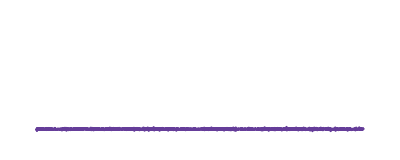
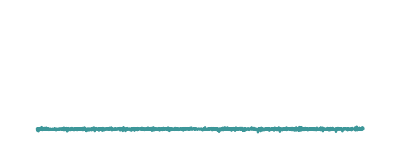
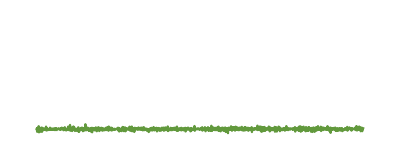
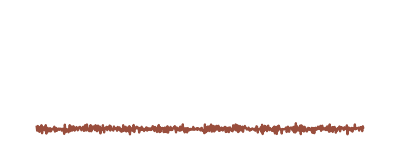
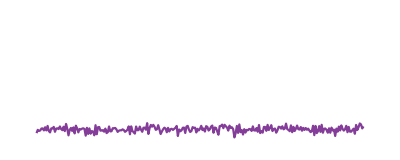
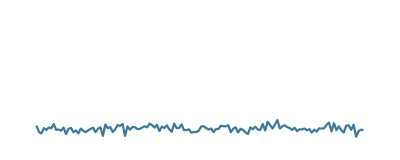
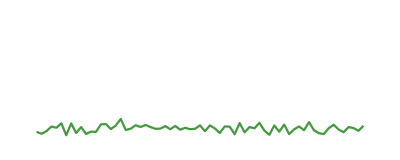
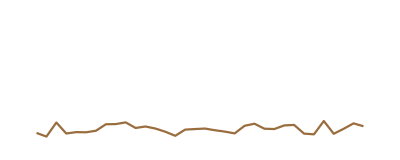
BasisIndex | {{1},{0,1},{0,0,1},{0,0,0,1},{0,0,0,0,1},{0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0}}
DataChannels | 0
DataDimensions | {8516}
DataWrapper | List
Dimensions | {{0}→{4258},{1}→{4258},{0,0}→{2129},{0,1}→{2129},{0,0,0}→{1065},{0,0,1}→{1065},{0,0,0,0}→{533},{0,0,0,1}→{533},{0,0,0,0,0}→{267},{0,0,0,0,1}→{267},{0,0,0,0,0,0}→{134},{0,0,0,0,0,1}→{134},{0,0,0,0,0,0,0}→{67},{0,0,0,0,0,0,1}→{67},{0,0,0,0,0,0,0,0}→{34},{0,0,0,0,0,0,0,1}→{34},{0,0,0,0,0,0,0,0,0}→{17},{0,0,0,0,0,0,0,0,1}→{17},{0,0,0,0,0,0,0,0,0,0}→{9},{0,0,0,0,0,0,0,0,0,1}→{9},{0,0,0,0,0,0,0,0,0,0,0}→{5},{0,0,0,0,0,0,0,0,0,0,1}→{5},{0,0,0,0,0,0,0,0,0,0,0,0}→{3},{0,0,0,0,0,0,0,0,0,0,0,1}→{3},{0,0,0,0,0,0,0,0,0,0,0,0,0}→{2},{0,0,0,0,0,0,0,0,0,0,0,0,1}→{2}}
EnergyFraction | {{1}→0.0135469,{0,1}→0.0204837,{0,0,1}→0.0352688,{0,0,0,1}→0.0571273,{0,0,0,0,1}→0.0517648,{0,0,0,0,0,1}→0.0320113,{0,0,0,0,0,0,1}→0.023011,{0,0,0,0,0,0,0,1}→0.0157361,{0,0,0,0,0,0,0,0,1}→0.0177069,{0,0,0,0,0,0,0,0,0,1}→0.0125099,{0,0,0,0,0,0,0,0,0,0,1}→0.0124506,{0,0,0,0,0,0,0,0,0,0,0,1}→0.00126898,{0,0,0,0,0,0,0,0,0,0,0,0,1}→0.00154285,{0,0,0,0,0,0,0,0,0,0,0,0,0}→0.705571}
ListPlot | {{1}→-Graphics-,{0,1}→-Graphics-,{0,0,1}→-Graphics-,{0,0,0,1}→-Graphics-,{0,0,0,0,1}→-Graphics-,{0,0,0,0,0,1}→-Graphics-,{0,0,0,0,0,0,1}→-Graphics-,{0,0,0,0,0,0,0,1}→-Graphics-,{0,0,0,0,0,0,0,0,1}→-Graphics-,{0,0,0,0,0,0,0,0,0,1}→-Graphics-,{0,0,0,0,0,0,0,0,0,0,1}→-Graphics-,{0,0,0,0,0,0,0,0,0,0,0,1}→-Graphics-,{0,0,0,0,0,0,0,0,0,0,0,0,1}→-Graphics-,{0,0,0,0,0,0,0,0,0,0,0,0,0}→-Graphics-}
Padding | Periodic
Properties | {BasisIndex,DataChannels,DataDimensions,DataWrapper,Dimensions,EnergyFraction,ListPlot,Padding,Properties,Refinement,ThresholdTable,ThresholdValues,Transform,TreeView,Wavelet,WaveletIndex}
Refinement | 13
ThresholdTable | Missing[NotAvailable]
ThresholdValues | Missing[NotAvailable]
Transform | DiscreteWaveletTransform
TreeView | -Graphics-
Wavelet | HaarWavelet[]
WaveletIndex | {{0},{1},{0,0},{0,1},{0,0,0},{0,0,1},{0,0,0,0},{0,0,0,1},{0,0,0,0,0},{0,0,0,0,1},{0,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,0,0,0},{0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
Grid@
Table[{p,Out[40][p]},{p,Out[40]["Properties"]}]
```

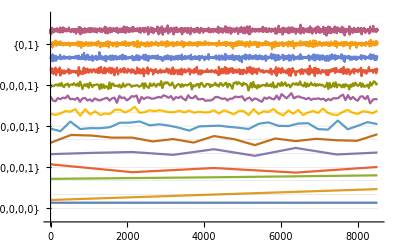

```mathematica
WaveletListPlot[Out[40],Ticks->Full]
```

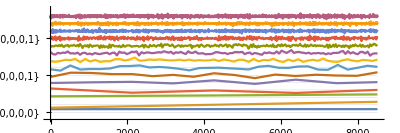

```mathematica
WaveletListPlot[Out[40],Ticks->Full,ImageSize->Full,AspectRatio->1/3]
```

```mathematica
WaveletListPlot[Out[40],Ticks->Full,ImageSize->Full,AspectRatio->1/3,PlotTheme->"Marketing"]
```

-Graphics-